# Vector WKB/PIA expansion for a system of coupled differential equations

## License and author info

Copyright © Ibai Asensio, 2025.

This Mathematica code computes the vector/multidimensional adiabatic WKB/phase-integral approximation for a system of coupled time-dependent harmonic oscillators (TDHOs) with time-dependent frequencies and coupling of the Pöschl-Teller form, and compares it with the exact (numerical) solution. The theory of the vector WKB/PIA was developed in Fulling (1975) (see Fulling (1979) and Skorupski (2008) as well). The results are performed to second adiabatic order. Unfortunately, no closed-form results for the required integrals (even at zeroth order) were achieved, but a semi-analytic approach was developed, using numerical integration for the integrals, to be able to see the results of the approximation.

This code is free software: you can redistribute it and/or modify it under the terms of the GNU General Public License, v3.0, as published by the Free Software Foundation. For more information, visit: https://www.gnu.org/licenses/

Developed by Ibai Asensio as part of the master thesis: ‘Towards Adiabatic States for Perturbations in Anisotropic Spacetimes. Analytical Approximations for Coupled Differential Equations in Quantum Fields in Curved Spacetimes’.

Supervisors:		Béatrice Bonga (Radboud Universiteit)
				Javier Olmedo (Universidad de Granada)
Second reader:	Wim J.P. Beenakker (Radboud Universiteit)

Part of a the  odes-approximations  project; find more accompanying files on the project’s repository.
If you find this code useful, or have any thoughtful feedback, you are encouraged to contact the author and let him know.

## Multi-dimensional adiabatic approximation (WKB/PIA) for two coupled Pöschl-Teller harmonic oscillators (TDHOs)

## Preamble

## Variables and notation

#### Clearing variables

```mathematica
ClearAll["Global`*"]
```

#### Notation short guide

- For a matrix X:	 X[t]->Symbolic matrix
mX[t]->True matrix X
X[i,j]==mX[[i,j]]->Components
- For a vector x:	x[t]->Symbolic vector
vx[t]->True vector x(t)
x[i]==vx[[i]]->Components
- Constants:		ζ_(n,k,±l)->	 n: order n,
						 k: eigenspace k,
						 ±: solution +/- (i.e. j->±ⅈ)
						 l: proportional to eigenvector e_k^(l)[t]

Semi-analytic updates (or after that) colored in purple.

## Shortcuts

#### Plotting styles

```mathematica
stylecompare={SolidData,Dashed,SolidData,Dashed};
```

```mathematica
stylecompare2={SolidData,SolidData,Dashed,Dashed};
```

```mathematica
stylenum={RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051](*,RGBColor[0.560181, 0.691569, 0.194885]*)};
```

```mathematica
style0th={{Dashing[Tiny],RGBColor[0.368417, 0.506779, 0.709798]},{Dashing[Tiny],RGBColor[0.880722, 0.611041, 0.142051]}(*,{Dashing[Tiny],RGBColor[0.560181, 0.691569, 0.194885]}*)};
```

```mathematica
style1st={{Dashed,RGBColor[0.368417, 0.506779, 0.709798]},{Dashed,RGBColor[0.880722, 0.611041, 0.142051]}(*,{Dashed,RGBColor[0.560181, 0.691569, 0.194885]}*)};
```

```mathematica
style2nd={{Dashing[0.037],RGBColor[0.368417, 0.506779, 0.709798]},{Dashing[0.037],RGBColor[0.880722, 0.611041, 0.142051]}(*,{Dashing[0.037],RGBColor[0.560181, 0.691569, 0.194885]}*)};
```

To mix some of these styles, use (e.g.)

```mathematica
Flatten[{stylenum,style0th,style1st,style2nd},1]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],{Dashing[Tiny],RGBColor[0.368417, 0.506779, 0.709798]},{Dashing[Tiny],RGBColor[0.880722, 0.611041, 0.142051]},{Dashing[{Small,Small}],RGBColor[0.368417, 0.506779, 0.709798]},{Dashing[{Small,Small}],RGBColor[0.880722, 0.611041, 0.142051]},{Dashing[0.037],RGBColor[0.368417, 0.506779, 0.709798]},{Dashing[0.037],RGBColor[0.880722, 0.611041, 0.142051]}}

#### Linear algebra shortcuts

Quick identity matrix:

```mathematica
II:=IdentityMatrix[dim];
```

Quick zero matrix:

```mathematica
m0:=Array[0&,{dim,dim}];
```

Quick zero vector:

```mathematica
v0:=Array[0&,dim];
```

#### Relevant time domain

```mathematica
relevantdomain={t,ti,tf}
```

{t,ti,tf}

## Custom functions

### Klein-Gordon product

These functions adopt the notation v⃗=(x_1,x_2,...,v_1,v_2,...) for elements of the phase space, and implement the Klein-Gordon inner product ((v⃗)^(1),(v⃗)^(2))=ⅈ(v⃗)^(1)Ω ((v⃗)^(2))* , with Ω the corresponding N-dimensional symplectic matrix.

```mathematica
SymplecticMatrix[n_]:=KroneckerProduct[{{0,1},{-1,0}},IdentityMatrix[n]]
```

```mathematica
PhaseSpaceArray[x_]:={Array[{x}[[#]]&,Length[{x}]],Array[D[{x}[[#]],t]&,Length[{x}]]}//Flatten
```

```mathematica
KleinGordonProduct[va_,vb_]:=If[
(*Condition:*)Length[va]===Length[vb],
(*Then:*)ⅈ PhaseSpaceArray[va].SymplecticMatrix[Length[PhaseSpaceArray[va]]/2].Conjugate[PhaseSpaceArray[vb]],
(*Else:*)Print["Dimensions of vectors do not agree."]]
```

```mathematica
KleinGordonNorm[v_]:=KleinGordonProduct[v,v]
```

### Linear algebra

#### Changes of basis

Build a linear operator from a vector set (i.e. the linear operator which transforms the basis vectors into the vector set provided to the function):

```mathematica
LinearOperator[vectorset_]:=Transpose[vectorset]
```

Change-of-basis matrix (the same operation as building a linear operator):

```mathematica
ChangeofBasisMatrix[newbasis_]:=Transpose[newbasis]
```

Change of basis for a matrix:

```mathematica
ChangedBasisMatrix[M_,newbasis_]:=Inverse[Transpose[newbasis]].M.Transpose[newbasis]//Simplify
```

Change of basis for a vector:

```mathematica
ChangedBasisVector[v_,newbasis_]:=Inverse[Transpose[newbasis]].v//Simplify
```

#### Some extra vector and matrix operations

Also, since Mathematica doesn’t distinguish between vectors and dual vectors (the built-in Transpose function doesn’t have any effect) some vector and matrix operations are not included by default. For example:

Bra-ket operator (i.e. dual vector acting on a vector):

```mathematica
Braket[u_,v_]:=({v}.Transpose[{u}])[[1]][[1]]
```

(This has the same effect as the Dot operation. However, the next functions are not.)

Ket-bra operator (i.e. vector acting on a dual vector):

```mathematica
Ketbra[u_,v_]:=Transpose[{u}].{v}
```

Vector-matrix multiplication:

```mathematica
DotVectorMatrix[v_,M_]:=
If[Length[v]==Length[M],
Array[∑_(l=1)^Length[v] v[[l]]M[[l,#]]&,Length[v]],
(* Else: *)
 Print["Error: Dimensions doesn't agree."]
]
```

#### Defining vectors and matrices

Constant vectors and matrices:

```mathematica
DefineVector[entriesName_,dim_]:=Array[entriesName[#]&,dim]
```

```mathematica
DefineMatrix[entriesName_,{dimRows_,dimCols_}]:=Array[entriesName[#1,#2]&,{dimRows,dimCols}]
```

```mathematica
DefineSquareMatrix[entriesName_,dim_]:=Array[entriesName[#1,#2]&,{dim,dim}]
```

Variable-dependent vectors and matrices:

```mathematica
DefineVectorVar[entriesName_,var_,dim_]:=Array[entriesName[#][var]&,dim]
```

```mathematica
DefineMatrixVar[entriesName_,var_,{dimRows_,dimCols_}]:=Array[entriesName[#1,#2][var]&,{dimRows,dimCols}]
```

```mathematica
DefineSquareMatrixVar[entriesName_,var_,dim_]:=Array[entriesName[#1,#2][var]&,{dim,dim}]
```

### Numerical help: NPrimitive functions

#### NPrimitive

```mathematica
NPrimitive[{integrand_,vari_},primitiveName_,{var_,varMin_,varMax_}]:=NDSolve[{primitiveName'[var]==integrand,primitiveName[vari]==0},primitiveName,{var,varMin,varMax}]
```

#### NPrimitiveValue

```mathematica
NPrimitiveValue[{integrand_,vari_},primitiveName_,{var_,varMin_,varMax_}]:=NDSolveValue[{primitiveName'[var]==integrand,primitiveName[vari]==0},primitiveName,{var,varMin,varMax}]
```

#### ParametricNPrimitive

```mathematica
ParametricNPrimitive[{integrand_,vari_},primitiveName_,{var_,varMin_,varMax_},paramList_]:=ParametricNDSolve[{primitiveName'[var]==integrand,primitiveName[vari]==0},primitiveName,{var,varMin,varMax},Flatten[{paramList}]]
```

```mathematica
ParametricNPrimitiveIC[{integrand_,vari_},primitiveName_,{var_,varMin_,varMax_},paramList_]:=ParametricNDSolve[{primitiveName'[var]==integrand,primitiveName[vari]==ic},primitiveName,{var,varMin,varMax},Flatten[{paramList,ic}]]
```

#### ParametricNPrimitiveValue

```mathematica
ParametricNPrimitiveValue[{integrand_,vari_},primitiveName_,{var_,varMin_,varMax_},paramList_]:=ParametricNDSolveValue[{primitiveName'[var]==integrand,primitiveName[vari]==0},primitiveName,{var,varMin,varMax},Flatten[{paramList}]]
```

```mathematica
ParametricNPrimitiveICValue[{integrand_,vari_},primitiveName_,{var_,varMin_,varMax_},paramList_]:=ParametricNDSolveValue[{primitiveName'[var]==integrand,primitiveName[vari]==ic},primitiveName,{var,varMin,varMax},Flatten[{paramList,ic}]]
```

#### Caution and comments

Caution! This procedure only gives the strict indefinite integral (or antiderivative or primitive function) if we set the integration constant to the value of the indefinite integral at the selected initial point, i.e. if

ic=F(t_i)

Nomenclature:

ParametricNPrimitive[{f[param ][t],ti},F,{t,tmin,tmax},{param }]

- ParametricNPrimitive gives the integral ∫_t_i^t =F(t)-F(t_i), F(t) being the indefinite integral (the antiderivative or primitive function).

- ParametricNPrimitiveIC in turn gives the integral ∫_t_i^t + ic=F(t)-F(t_i)+ic.

(More info & context on this in Integrating with ParametricNDSolve.nb notebook.)

## The problem

## Generic inputs

### Dimension (number of equations)

```mathematica
dim=2;
```

### Adiabatic order (highest considered)

```mathematica
adbOrd=2;
```

## Equation of motion

```mathematica
Eom[M_,x_]:=D[x,{t,2}]+T^2 M.x
```

#### Symbolically

```mathematica
Eom[M[t],x[t]]
```

T^2 M[t].x[t]+x''[t]

#### Vectors & matrices’ components

```mathematica
mM[t_]=Array[M[#1,#2][t]&,{dim,dim}]
```

{{M[1,1][t],M[1,2][t]},{M[2,1][t],M[2,2][t]}}

```mathematica
vx[t_]=Array[x[#][t]&,dim]
```

{x[1][t],x[2][t]}

#### EOM in components

```mathematica
Eom[mM[t],vx[t]]//MatrixForm
```

(T^2 (M[1,1][t] x[1][t]+M[1,2][t] x[2][t])+x[1]''[t]
T^2 (M[2,1][t] x[1][t]+M[2,2][t] x[2][t])+x[2]''[t])

## Specializing the problem (form of the M(t) matrix)

Specifying a model here means to select a specific matrix M(t), i.e.  mM[t_] in the code.

Here we specialize it for two generic, coupled, time-dependent harmonic oscillators.

### Coupled oscillators

```mathematica
mM[ω1_,α1_,τ1_,ω2_,α2_,τ2_,αc_,τc_][t_]={{kc[t]/(m[1][t])+(Ω[1][t])^2,-kc[t]/(m[1][t])},{-kc[t]/(m[2][t]),kc[t]/(m[2][t])+(Ω[2][t])^2}};
mM[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]//MatrixForm
```

(kc[t]/(m[1][t])+(Ω[1][t])^2 | -kc[t]/(m[1][t])
-kc[t]/(m[2][t]) | kc[t]/(m[2][t])+(Ω[2][t])^2)

### Assumptions on the functions

#### Masses: equal, constant and normalized

```mathematica
m[1][t_]=1;
m[2][t_]=1;
(*m[3][t_]=1;*)
vm[t]
```

vm[t]

#### Frequencies and couplings: real and positive

```mathematica
$Assumptions={};
$Assumptions=Flatten@AppendTo[$Assumptions,{
t∈Reals,
Ω[1][t]∈Reals,Ω[2][t]∈Reals,Ω[3][t]∈Reals,
Ω[1][t]>0,Ω[2][t]>0,Ω[3][t]>0,
kc[t]∈Reals,
kc[t]>0
}]
```

{t∈ℝ,Ω[1][t]∈ℝ,Ω[2][t]∈ℝ,Ω[3][t]∈ℝ,Ω[1][t]>0,Ω[2][t]>0,Ω[3][t]>0,kc[t]∈ℝ,kc[t]>0}

## Fulling’s method, part I ↪︎ Eigen-analysis, Kato transformation and adiabatic ansatz for two fully generic TDHOs

## Eigen-analysis of M(t)

### Eigenvalues

#### Computation

```mathematica
eigenvalues=Eigenvalues[mM[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]];
Print[eigenvalues]
```

{1/2 (2 kc[t]+(Ω[1][t])^2+(Ω[2][t])^2-√(4 kc[t]^2+(Ω[1][t])^4-2 (Ω[1][t])^2 (Ω[2][t])^2+(Ω[2][t])^4)),1/2 (2 kc[t]+(Ω[1][t])^2+(Ω[2][t])^2+√(4 kc[t]^2+(Ω[1][t])^4-2 (Ω[1][t])^2 (Ω[2][t])^2+(Ω[2][t])^4))}

#### Number of different eigenvalues

```mathematica
nk=CountDistinct[eigenvalues]
```

2

#### Name each eigenvalue

Automatically:

```mathematica
For[k=1,k<=nk,k++,{
p[k][ω1_,α1_,τ1_,ω2_,α2_,τ2_,αc_,τc_][t_]=DeleteDuplicates[eigenvalues][[k]],
Print["p[",k,"][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t] = ",p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]]
}]
```

p[1][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t] = 1/2 (2 kc[t]+(Ω[1][t])^2+(Ω[2][t])^2-√(4 kc[t]^2+(Ω[1][t])^4-2 (Ω[1][t])^2 (Ω[2][t])^2+(Ω[2][t])^4))

p[2][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t] = 1/2 (2 kc[t]+(Ω[1][t])^2+(Ω[2][t])^2+√(4 kc[t]^2+(Ω[1][t])^4-2 (Ω[1][t])^2 (Ω[2][t])^2+(Ω[2][t])^4))

#### Dimension of each eigenspace

```mathematica
For[k=1,k<=nk,k++,{
nl[k]=Count[eigenvalues,p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]],
Print["nl[",k,"] = ",nl[k]]
}]
```

nl[1] = 1

nl[2] = 1

### Eigenvectors

#### Computation

```mathematica
eigenvectors=Eigenvectors[mM[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]]//Simplify;
Print[eigenvectors]
```

{{(-(Ω[1][t])^2+(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))/(2 kc[t]),1},{-((Ω[1][t])^2-(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))/(2 kc[t]),1}}

Check that the computed eigenvectors are orthogonal:

```mathematica
For[k=1,k<=dim,k++,
For[l=k+1,l<=dim,l++,{
Print[TrueQ[eigenvectors[[k]].eigenvectors[[l]]==0//Simplify]]
}]
]
```

True

#### Orthonormalized eigenvectors (manual!)

```mathematica
eigenvectors={eigenvectors[[1]]/Norm[eigenvectors[[1]]],eigenvectors[[2]]/Norm[eigenvectors[[2]]]}//Simplify;
Print[eigenvectors]
```

{{(-(Ω[1][t])^2+(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))/(kc[t] √(4+((-(Ω[1][t])^2+(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))^2)/kc[t]^2)),2/(√(4+((-(Ω[1][t])^2+(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))^2)/kc[t]^2))},{(-(Ω[1][t])^2+(Ω[2][t])^2-√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))/(kc[t] √(4+(((Ω[1][t])^2-(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))^2)/kc[t]^2)),2/(√(4+(((Ω[1][t])^2-(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))^2)/kc[t]^2))}}

#### Name each eigenvector

Automatically:

```mathematica
ñ=1;
For[k=1,k<=nk,k++,
For[l=1,l<=nl[k],l++,{
e[k,l][ω1_,α1_,τ1_,ω2_,α2_,τ2_,αc_,τc_][t_]=eigenvectors[[ñ]],
Print["e[",k,",",l,"][t] = ",e[k,l][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]],
ñ=ñ+1
}]
]
```

e[1,1][t] = {(-(Ω[1][t])^2+(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))/(kc[t] √(4+((-(Ω[1][t])^2+(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))^2)/kc[t]^2)),2/(√(4+((-(Ω[1][t])^2+(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))^2)/kc[t]^2))}

e[2,1][t] = {(-(Ω[1][t])^2+(Ω[2][t])^2-√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))/(kc[t] √(4+(((Ω[1][t])^2-(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))^2)/kc[t]^2)),2/(√(4+(((Ω[1][t])^2-(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))^2)/kc[t]^2))}

Check that the order is consistent (shall return all True):

```mathematica
For[k=1,k<=nk,k++,
For[l=1,l<=nl[k],l++,
Print[
mM[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t].e[k,l][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]==p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]e[k,l][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]//Simplify
]
]
]
```

True

True

(If the order weren’t consistent, manually select them until all match.)

#### Normalization (if needed)

(It won’t be needed since we have already applied Orthogonalize; in any case, this code checks if each eigenvector is normalized and if not divides it by its norm.)

```mathematica
(*eigenvectors={};
For[k=1,k<=nk,k++,
For[l=1,l<=nl[k],l++,
If[TrueQ[Norm[e[k,l][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]]==1(*//ComplexExpand*)//Simplify//PowerExpand],{
(* Already normalized *)
Print["Vector e[",k,"][",l,"][t] already normalized."],
AppendTo[eigenvectors,e[k,l][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]]},{
(* Else: *)
e[k,l][ω1_,α1_,τ1_,ω2_,α2_,τ2_,αc_,τc_][t_]=e[k,l][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]/Norm[e[k,l][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]](*//ComplexExpand*)//Simplify//PowerExpand,
Print["Vector e[",k,"][",l,"][t] normalized to ",e[k,l][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]],
AppendTo[eigenvectors,e[k,l][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]]
}]
]]*)
```

(They are already normalized, but this step takes a bit of time that I don’t want to lose.)

### Eigenprojectors

#### Computation

```mathematica
For[k=1,k<=nk,k++,
mP[k][ω1_,α1_,τ1_,ω2_,α2_,τ2_,αc_,τc_][t_]=∑_(l=1)^nl[k] Ketbra[e[k,l][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t],e[k,l][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]];
Print["mP[",k,"][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t] = ",mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]//MatrixForm]
]
```

mP[1][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t] = (((-(Ω[1][t])^2+(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))^2)/(kc[t]^2 (4+((-(Ω[1][t])^2+(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))^2)/kc[t]^2)) | (2 (-(Ω[1][t])^2+(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2)))/(kc[t] (4+((-(Ω[1][t])^2+(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))^2)/kc[t]^2))
(2 (-(Ω[1][t])^2+(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2)))/(kc[t] (4+((-(Ω[1][t])^2+(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))^2)/kc[t]^2)) | 4/(4+((-(Ω[1][t])^2+(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))^2)/kc[t]^2))

mP[2][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t] = (((-(Ω[1][t])^2+(Ω[2][t])^2-√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))^2)/(kc[t]^2 (4+(((Ω[1][t])^2-(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))^2)/kc[t]^2)) | (2 (-(Ω[1][t])^2+(Ω[2][t])^2-√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2)))/(kc[t] (4+(((Ω[1][t])^2-(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))^2)/kc[t]^2))
(2 (-(Ω[1][t])^2+(Ω[2][t])^2-√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2)))/(kc[t] (4+(((Ω[1][t])^2-(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))^2)/kc[t]^2)) | 4/(4+(((Ω[1][t])^2-(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))^2)/kc[t]^2))

### Some properties

#### Eigenprojectors

1. Eigenprojectors are indeed projector operators:

P_k^2=P_k

```mathematica
For[k=1,k<=nk,k++,
Print[
TrueQ[mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]==mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t].mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]//Simplify]
]]
```

True

True

2. Combined, they add up to the identity (i.e. the sum of all eigenspaces cover the whole space):

∑_k P_k=1

```mathematica
∑_(k=1)^nk mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]//Simplify//MatrixForm
```

(1 | 0
0 | 1)

This translates into the relation:

P_k=(1-∑_(k'≠ k) P_k')

```mathematica
TrueQ[mP[1][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]==II-mP[2][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]//Simplify]
TrueQ[mP[2][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]==II-mP[1][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]//Simplify]
```

True

True

3. Eigenprojectors acting on their own matrix give the eigenvalue times the eigenprojector:

P M=p_k P

```mathematica
For[k=1,k<=nk,k++,Print[
mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t].mM[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]==p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]//Simplify
]]
```

True

True

This translates into:

P (M-p_k)=0

4. Furthermore, eigenprojectors commute with their own matrix:

P M=M P

```mathematica
For[k=1,k<=nk,k++,Print[
mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t].mM[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]==mM[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t].mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]//Simplify
]]
```

True

True

#### Eigenvectors

5. Eigenvectors indeed belong to their eigen-spaces:

P_k p_k=p_k

```mathematica
For[k=1,k<=nk,k++,
For[l=1,l<=nl[k],l++,
Print[
TrueQ[mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t].e[k,l][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]==e[k,l][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]//Simplify]
]]]
```

True

True

### Diagonalization of M(t)

#### Usual change-of-basis matrix L(t)

```mathematica
mL[ω1_,α1_,τ1_,ω2_,α2_,τ2_,αc_,τc_][t_]=ChangeofBasisMatrix[eigenvectors];
Print[mL[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]//MatrixForm]
```

((-(Ω[1][t])^2+(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))/(kc[t] √(4+((-(Ω[1][t])^2+(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))^2)/kc[t]^2)) | (-(Ω[1][t])^2+(Ω[2][t])^2-√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))/(kc[t] √(4+(((Ω[1][t])^2-(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))^2)/kc[t]^2))
2/(√(4+((-(Ω[1][t])^2+(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))^2)/kc[t]^2)) | 2/(√(4+(((Ω[1][t])^2-(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))^2)/kc[t]^2)))

#### Fulling’s change-of-basis matrix D(t) = L^-1(t)

```mathematica
mD[ω1_,α1_,τ1_,ω2_,α2_,τ2_,αc_,τc_][t_]=Inverse[mL[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]]//Simplify;
Print[mD[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]//MatrixForm]
```

(1/2 kc[t] √((4+((-(Ω[1][t])^2+(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))^2)/kc[t]^2)/(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2)) | 1/4 ((Ω[1][t])^2-(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2)) √((4+((-(Ω[1][t])^2+(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))^2)/kc[t]^2)/(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))
-1/2 kc[t] √((4+(((Ω[1][t])^2-(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))^2)/kc[t]^2)/(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2)) | 1/4 (-(Ω[1][t])^2+(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2)) √((4+(((Ω[1][t])^2-(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))^2)/kc[t]^2)/(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2)))

#### Diagonal M’ = L^-1 M L in the basis {e_k(t)}

```mathematica
mMdiag[ω1_,α1_,τ1_,ω2_,α2_,τ2_,αc_,τc_][t_]=ChangedBasisMatrix[mM[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t],eigenvectors];
Print[mMdiag[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]//MatrixForm]
```

((-4 kc[t]^2-(Ω[1][t])^4+2 (Ω[1][t])^2 (Ω[2][t])^2-(Ω[2][t])^4+2 kc[t] √(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2)+(Ω[1][t])^2 √(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2)+(Ω[2][t])^2 √(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))/(2 √(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2)) | 0
0 | (4 kc[t]^2+(Ω[1][t])^4-2 (Ω[1][t])^2 (Ω[2][t])^2+(Ω[2][t])^4+2 kc[t] √(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2)+(Ω[1][t])^2 √(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2)+(Ω[2][t])^2 √(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))/(2 √(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2)))

#### The eigenprojectors in their own eigenbasis

The eigenprojectors in their own eigenbasis take the form of a diagonal matrix with only 1’s or 0’s in the diagonal. Concretely, they have 1’s in the corresponding positions of their eigenvectors, i.e. they are a n_k×n_k identity matrix. This is because the columns of a matrix expressed in a certain basis tells what it does to the elements of the basis, and here the projections leave the eigenvectors intact.

Check:

```mathematica
For[k=1,k<=nk,k++,{
mPdiag[k][ω1_,α1_,τ1_,ω2_,α2_,τ2_,αc_,τc_][t_]=ChangedBasisMatrix[mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t],eigenvectors],
Print["mPdiag[",k,"][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t] = ",mPdiag[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]//MatrixForm]
}]
```

mPdiag[1][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t] = (1 | 0
0 | 0)

mPdiag[2][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t] = (0 | 0
0 | 1)

Now is even more clear that they add up to the identity:

```mathematica
TrueQ[∑_(k=1)^nk mPdiag[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]==II//Simplify]
```

True

## Kato’s adiabatic transformation U(t)

↪︎ Very last step (checking & simplifying M diagonalization) takes quite long but computes. I switched it off to save time.

### Initial time

This process relies on the definition of an initial time, from which the eigenvectors at all later times are calculated through a transformation.

Obs: We will leave it unspecified for now, labeled ti, and fix it later along the model.

### Operator Q(t)=∑_k P_k'(t)P_k(t)

```mathematica
mQ[ω1_,α1_,τ1_,ω2_,α2_,τ2_,αc_,τc_][t_]=∑_(k=1)^nk mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]'[t].mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]//Simplify;
Print[mQ[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]//MatrixForm]
```

(0 | ((Ω[1][t])^2 kc'[t]-2 kc[t] Ω[1][t] Ω[1]'[t]+Ω[2][t] (-Ω[2][t] kc'[t]+2 kc[t] Ω[2]'[t]))/(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2)
(-(Ω[1][t])^2 kc'[t]+2 kc[t] Ω[1][t] Ω[1]'[t]+Ω[2][t] (Ω[2][t] kc'[t]-2 kc[t] Ω[2]'[t]))/(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2) | 0)

### Kato’s adiabatic transformation operator U(t)

#### Components’ definition

```mathematica
mU[ω1_,α1_,τ1_,ω2_,α2_,τ2_,αc_,τc_][t_]=Array[U[#1,#2][t]&,{dim,dim}];
Print[mU[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]//MatrixForm]
```

(U[1,1][t] | U[1,2][t]
U[2,1][t] | U[2,2][t])

#### Equations for the U(t) components

The fundamental equation satisfied by the Kato transformation operator is:

U '(t)=Q(t)U(t)=∑_k P_k'(t)P_k(t) U(t)

```mathematica
eqnsU={};
varsU={};
For[k=1,k<=dim,k++,
For[l=1,l<=dim,l++,{
eqnU[k,l]={mU[ω1,α1,τ1,ω2,α2,τ2,αc,τc]'[t][[k,l]]==(mQ[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t].mU[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])[[k,l]],mU[ω1,α1,τ1,ω2,α2,τ2,αc,τc][ti][[k,l]]==IdentityMatrix[dim][[k,l]]},
Print[eqnU[k,l]],
AppendTo[eqnsU,eqnU[k,l]],
AppendTo[varsU,U[k,l]]
}]
]
eqnsU=eqnsU//Flatten;
```

{U[1,1]'[t]==(U[2,1][t] ((Ω[1][t])^2 kc'[t]-2 kc[t] Ω[1][t] Ω[1]'[t]+Ω[2][t] (-Ω[2][t] kc'[t]+2 kc[t] Ω[2]'[t])))/(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2),U[1,1][ti]==1}

{U[1,2]'[t]==(U[2,2][t] ((Ω[1][t])^2 kc'[t]-2 kc[t] Ω[1][t] Ω[1]'[t]+Ω[2][t] (-Ω[2][t] kc'[t]+2 kc[t] Ω[2]'[t])))/(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2),U[1,2][ti]==0}

{U[2,1]'[t]==(U[1,1][t] (-(Ω[1][t])^2 kc'[t]+2 kc[t] Ω[1][t] Ω[1]'[t]+Ω[2][t] (Ω[2][t] kc'[t]-2 kc[t] Ω[2]'[t])))/(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2),U[2,1][ti]==0}

{U[2,2]'[t]==(U[1,2][t] (-(Ω[1][t])^2 kc'[t]+2 kc[t] Ω[1][t] Ω[1]'[t]+Ω[2][t] (Ω[2][t] kc'[t]-2 kc[t] Ω[2]'[t])))/(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2),U[2,2][ti]==1}

#### System of solutions (just display)

```mathematica
For[k=1,k<=dim,k++,
For[l=1,l<=dim,l++,{
Print[(DSolve[{mU[ω1,α1,τ1,ω2,α2,τ2,αc,τc]'[t][[k,l]]==(mQ[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t].mU[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])[[k,l]],mU[ω1,α1,τ1,ω2,α2,τ2,αc,τc][ti][[k,l]]==IdentityMatrix[dim][[k,l]]},U[k,l][t],t]/.K[_]->Subscript[t, 1]//Flatten)[[1]]]
}]
]
```

U[1,1][t]→1+(U[2,1][t_1] (Ω[1][t_1])^2 kc'[t_1]-U[2,1][t_1] (Ω[2][t_1])^2 kc'[t_1]-2 kc[t_1] U[2,1][t_1] Ω[1][t_1] Ω[1]'[t_1]+2 kc[t_1] U[2,1][t_1] Ω[2][t_1] Ω[2]'[t_1])/(4 kc[t_1]^2+(Ω[1][t_1])^4-2 (Ω[1][t_1])^2 (Ω[2][t_1])^2+(Ω[2][t_1])^4)t_11t-(U[2,1][t_1] (Ω[1][t_1])^2 kc'[t_1]-U[2,1][t_1] (Ω[2][t_1])^2 kc'[t_1]-2 kc[t_1] U[2,1][t_1] Ω[1][t_1] Ω[1]'[t_1]+2 kc[t_1] U[2,1][t_1] Ω[2][t_1] Ω[2]'[t_1])/(4 kc[t_1]^2+(Ω[1][t_1])^4-2 (Ω[1][t_1])^2 (Ω[2][t_1])^2+(Ω[2][t_1])^4)t_11ti

U[1,2][t]→(U[2,2][t_1] (Ω[1][t_1])^2 kc'[t_1]-U[2,2][t_1] (Ω[2][t_1])^2 kc'[t_1]-2 kc[t_1] U[2,2][t_1] Ω[1][t_1] Ω[1]'[t_1]+2 kc[t_1] U[2,2][t_1] Ω[2][t_1] Ω[2]'[t_1])/(4 kc[t_1]^2+(Ω[1][t_1])^4-2 (Ω[1][t_1])^2 (Ω[2][t_1])^2+(Ω[2][t_1])^4)t_11t-(U[2,2][t_1] (Ω[1][t_1])^2 kc'[t_1]-U[2,2][t_1] (Ω[2][t_1])^2 kc'[t_1]-2 kc[t_1] U[2,2][t_1] Ω[1][t_1] Ω[1]'[t_1]+2 kc[t_1] U[2,2][t_1] Ω[2][t_1] Ω[2]'[t_1])/(4 kc[t_1]^2+(Ω[1][t_1])^4-2 (Ω[1][t_1])^2 (Ω[2][t_1])^2+(Ω[2][t_1])^4)t_11ti

U[2,1][t]→(-U[1,1][t_1] (Ω[1][t_1])^2 kc'[t_1]+U[1,1][t_1] (Ω[2][t_1])^2 kc'[t_1]+2 kc[t_1] U[1,1][t_1] Ω[1][t_1] Ω[1]'[t_1]-2 kc[t_1] U[1,1][t_1] Ω[2][t_1] Ω[2]'[t_1])/(4 kc[t_1]^2+(Ω[1][t_1])^4-2 (Ω[1][t_1])^2 (Ω[2][t_1])^2+(Ω[2][t_1])^4)t_11t-(-U[1,1][t_1] (Ω[1][t_1])^2 kc'[t_1]+U[1,1][t_1] (Ω[2][t_1])^2 kc'[t_1]+2 kc[t_1] U[1,1][t_1] Ω[1][t_1] Ω[1]'[t_1]-2 kc[t_1] U[1,1][t_1] Ω[2][t_1] Ω[2]'[t_1])/(4 kc[t_1]^2+(Ω[1][t_1])^4-2 (Ω[1][t_1])^2 (Ω[2][t_1])^2+(Ω[2][t_1])^4)t_11ti

U[2,2][t]→1+(-U[1,2][t_1] (Ω[1][t_1])^2 kc'[t_1]+U[1,2][t_1] (Ω[2][t_1])^2 kc'[t_1]+2 kc[t_1] U[1,2][t_1] Ω[1][t_1] Ω[1]'[t_1]-2 kc[t_1] U[1,2][t_1] Ω[2][t_1] Ω[2]'[t_1])/(4 kc[t_1]^2+(Ω[1][t_1])^4-2 (Ω[1][t_1])^2 (Ω[2][t_1])^2+(Ω[2][t_1])^4)t_11t-(-U[1,2][t_1] (Ω[1][t_1])^2 kc'[t_1]+U[1,2][t_1] (Ω[2][t_1])^2 kc'[t_1]+2 kc[t_1] U[1,2][t_1] Ω[1][t_1] Ω[1]'[t_1]-2 kc[t_1] U[1,2][t_1] Ω[2][t_1] Ω[2]'[t_1])/(4 kc[t_1]^2+(Ω[1][t_1])^4-2 (Ω[1][t_1])^2 (Ω[2][t_1])^2+(Ω[2][t_1])^4)t_11ti

#### Solution for U(t)

```mathematica
solU=DSolve[eqnsU,varsU,t]//Flatten;
Print[solU]
```

{U[1,1]→Function[{t},(Cos[1/4 ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-1/4 ArcTan[(2 kc[t])/(-(Ω[1][t])^2+(Ω[2][t])^2)]] Cos[1/4 ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]-1/4 ArcTan[(2 kc[ti])/(-(Ω[1][ti])^2+(Ω[2][ti])^2)]]+Sin[1/4 ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-1/4 ArcTan[(2 kc[t])/(-(Ω[1][t])^2+(Ω[2][t])^2)]] Sin[1/4 ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]-1/4 ArcTan[(2 kc[ti])/(-(Ω[1][ti])^2+(Ω[2][ti])^2)]])/(Cos[1/4 ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]-1/4 ArcTan[(2 kc[ti])/(-(Ω[1][ti])^2+(Ω[2][ti])^2)]]^2+Sin[1/4 ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]-1/4 ArcTan[(2 kc[ti])/(-(Ω[1][ti])^2+(Ω[2][ti])^2)]]^2)],U[2,1]→Function[{t},(-Cos[1/4 ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]-1/4 ArcTan[(2 kc[ti])/(-(Ω[1][ti])^2+(Ω[2][ti])^2)]] Sin[1/4 ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-1/4 ArcTan[(2 kc[t])/(-(Ω[1][t])^2+(Ω[2][t])^2)]]+Cos[1/4 ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-1/4 ArcTan[(2 kc[t])/(-(Ω[1][t])^2+(Ω[2][t])^2)]] Sin[1/4 ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]-1/4 ArcTan[(2 kc[ti])/(-(Ω[1][ti])^2+(Ω[2][ti])^2)]])/(Cos[1/4 ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]-1/4 ArcTan[(2 kc[ti])/(-(Ω[1][ti])^2+(Ω[2][ti])^2)]]^2+Sin[1/4 ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]-1/4 ArcTan[(2 kc[ti])/(-(Ω[1][ti])^2+(Ω[2][ti])^2)]]^2)],U[1,2]→Function[{t},(Cos[1/4 ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]-1/4 ArcTan[(2 kc[ti])/(-(Ω[1][ti])^2+(Ω[2][ti])^2)]] Sin[1/4 ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-1/4 ArcTan[(2 kc[t])/(-(Ω[1][t])^2+(Ω[2][t])^2)]]-Cos[1/4 ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-1/4 ArcTan[(2 kc[t])/(-(Ω[1][t])^2+(Ω[2][t])^2)]] Sin[1/4 ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]-1/4 ArcTan[(2 kc[ti])/(-(Ω[1][ti])^2+(Ω[2][ti])^2)]])/(Cos[1/4 ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]-1/4 ArcTan[(2 kc[ti])/(-(Ω[1][ti])^2+(Ω[2][ti])^2)]]^2+Sin[1/4 ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]-1/4 ArcTan[(2 kc[ti])/(-(Ω[1][ti])^2+(Ω[2][ti])^2)]]^2)],U[2,2]→Function[{t},(Cos[1/4 ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-1/4 ArcTan[(2 kc[t])/(-(Ω[1][t])^2+(Ω[2][t])^2)]] Cos[1/4 ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]-1/4 ArcTan[(2 kc[ti])/(-(Ω[1][ti])^2+(Ω[2][ti])^2)]]+Sin[1/4 ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-1/4 ArcTan[(2 kc[t])/(-(Ω[1][t])^2+(Ω[2][t])^2)]] Sin[1/4 ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]-1/4 ArcTan[(2 kc[ti])/(-(Ω[1][ti])^2+(Ω[2][ti])^2)]])/(Cos[1/4 ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]-1/4 ArcTan[(2 kc[ti])/(-(Ω[1][ti])^2+(Ω[2][ti])^2)]]^2+Sin[1/4 ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]-1/4 ArcTan[(2 kc[ti])/(-(Ω[1][ti])^2+(Ω[2][ti])^2)]]^2)]}

```mathematica
Print[mU[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]/.solU//MatrixForm//Simplify]
```

(Cos[1/2 (ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)])] | Sin[1/2 (ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)])]
-Sin[1/2 (ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)])] | Cos[1/2 (ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)])])

#### Redefinition based on the found solution

```mathematica
mU[ω1_,α1_,τ1_,ω2_,α2_,τ2_,αc_,τc_][t_]=mU[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]/.solU//Simplify;
Print[mU[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]//MatrixForm]
```

(Cos[1/2 (ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)])] | Sin[1/2 (ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)])]
-Sin[1/2 (ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)])] | Cos[1/2 (ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)])])

Let’s compute and name the inverse (so it doesn’t need to be computed more times):

```mathematica
mUinv[ω1_,α1_,τ1_,ω2_,α2_,τ2_,αc_,τc_][t_]=Inverse[mU[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]]//Simplify;
Print[mUinv[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]//MatrixForm]
```

(Cos[1/2 (ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)])] | -Sin[1/2 (ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)])]
Sin[1/2 (ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)])] | Cos[1/2 (ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)])])

### Time evolution through Kato’s transformation

#### Eigenvectors

The Kato transformation is defined s.t. it realizes the equation:

v_k(t)=U(t)v_k(t_i)

for v_k(t) eigenvectors of M(t).

Check for our e_k(t):

```mathematica
(*For[k=1,k<=nk,k++,
For[l=1,l<=nl[k],l++,
TrueQ[Print[
e[k,l][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]==mU[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t].e[k,l][ω1,α1,τ1,ω2,α2,τ2,αc,τc][ti]
]]
]
]*)
```

#### Time-dependent diagonalization

“If D diagonalizes M(t_i), i.e. D M(t_i)D^-1 is diagonal, then D U(t)^-1 diagonalizes M(t)”.

Translated to L:
“If L^-1 diagonalizes M(t_i), i.e. L^-1 M(t_i)L is diagonal, then L^-1 (U(t))^-1 diagonalizes M(t)”.
This L is then our L(t_i) (since it diagonalizes M(t_i)). Hence, the statement is that

(L(t_i))^-1(U(t))^-1 M(t)U(t)L(t_i) is diagonal.

Check:

```mathematica
Print[Inverse[mL[ω1,α1,τ1,ω2,α2,τ2,αc,τc][ti]].mUinv[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t].mM[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t].mU[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t].mL[ω1,α1,τ1,ω2,α2,τ2,αc,τc][ti]//Simplify//MatrixForm]
```

((-Cos[ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]] (Ω[1][t])^2 (Ω[1][ti])^2+Cos[ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]] (Ω[1][ti])^2 (Ω[2][t])^2+2 kc[ti] Sin[ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]] ((Ω[1][t])^2-(Ω[2][t])^2)+Cos[ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]] (Ω[1][t])^2 (Ω[2][ti])^2-Cos[ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]] (Ω[2][t])^2 (Ω[2][ti])^2+(Ω[1][t])^2 √(4 kc[ti]^2+((Ω[1][ti])^2-(Ω[2][ti])^2)^2)+(Ω[2][t])^2 √(4 kc[ti]^2+((Ω[1][ti])^2-(Ω[2][ti])^2)^2)+2 kc[t] (-2 Cos[ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]] kc[ti]-Sin[ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]] (Ω[1][ti])^2+Sin[ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]] (Ω[2][ti])^2+√(4 kc[ti]^2+((Ω[1][ti])^2-(Ω[2][ti])^2)^2)))/(2 √(4 kc[ti]^2+((Ω[1][ti])^2-(Ω[2][ti])^2)^2)) | ((2 kc[t] (-2 kc[ti] Sin[ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]]+Cos[ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]] ((Ω[1][ti])^2-(Ω[2][ti])^2))-((Ω[1][t])^2-(Ω[2][t])^2) (2 Cos[ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]] kc[ti]+Sin[ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]] ((Ω[1][ti])^2-(Ω[2][ti])^2))) ((Ω[1][ti])^2-(Ω[2][ti])^2+√(4 kc[ti]^2+((Ω[1][ti])^2-(Ω[2][ti])^2)^2)) √(4+((-(Ω[1][ti])^2+(Ω[2][ti])^2+√(4 kc[ti]^2+((Ω[1][ti])^2-(Ω[2][ti])^2)^2))^2)/kc[ti]^2))/(4 √2 kc[ti] √(4 kc[ti]^2+((Ω[1][ti])^2-(Ω[2][ti])^2)^2) √(4+(((Ω[1][ti])^2-(Ω[2][ti])^2) ((Ω[1][ti])^2-(Ω[2][ti])^2+√(4 kc[ti]^2+((Ω[1][ti])^2-(Ω[2][ti])^2)^2)))/kc[ti]^2))
((2 kc[t] (-2 kc[ti] Sin[ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]]+Cos[ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]] ((Ω[1][ti])^2-(Ω[2][ti])^2))-((Ω[1][t])^2-(Ω[2][t])^2) (2 Cos[ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]] kc[ti]+Sin[ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]] ((Ω[1][ti])^2-(Ω[2][ti])^2))) (-(Ω[1][ti])^2+(Ω[2][ti])^2+√(4 kc[ti]^2+((Ω[1][ti])^2-(Ω[2][ti])^2)^2)) √(4+(((Ω[1][ti])^2-(Ω[2][ti])^2+√(4 kc[ti]^2+((Ω[1][ti])^2-(Ω[2][ti])^2)^2))^2)/kc[ti]^2))/(4 √2 kc[ti] √(4 kc[ti]^2+((Ω[1][ti])^2-(Ω[2][ti])^2)^2) √(4-(((Ω[1][ti])^2-(Ω[2][ti])^2) (-(Ω[1][ti])^2+(Ω[2][ti])^2+√(4 kc[ti]^2+((Ω[1][ti])^2-(Ω[2][ti])^2)^2)))/kc[ti]^2)) | (Cos[ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]] (Ω[1][t])^2 (Ω[1][ti])^2-Cos[ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]] (Ω[1][ti])^2 (Ω[2][t])^2-2 kc[ti] Sin[ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]] ((Ω[1][t])^2-(Ω[2][t])^2)-Cos[ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]] (Ω[1][t])^2 (Ω[2][ti])^2+Cos[ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]] (Ω[2][t])^2 (Ω[2][ti])^2+(Ω[1][t])^2 √(4 kc[ti]^2+((Ω[1][ti])^2-(Ω[2][ti])^2)^2)+(Ω[2][t])^2 √(4 kc[ti]^2+((Ω[1][ti])^2-(Ω[2][ti])^2)^2)+2 kc[t] (2 Cos[ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]] kc[ti]+Sin[ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]] (Ω[1][ti])^2-Sin[ArcTan[(2 kc[t])/((Ω[1][t])^2-(Ω[2][t])^2)]-ArcTan[(2 kc[ti])/((Ω[1][ti])^2-(Ω[2][ti])^2)]] (Ω[2][ti])^2+√(4 kc[ti]^2+((Ω[1][ti])^2-(Ω[2][ti])^2)^2)))/(2 √(4 kc[ti]^2+((Ω[1][ti])^2-(Ω[2][ti])^2)^2)))

```mathematica
(*Print[Assuming[Ω[1][t]!=Ω[2][t],Inverse[mL[ω1,α1,τ1,ω2,α2,τ2,αc,τc][ti]].mUinv[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t].mM[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t].mU[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t].mL[ω1,α1,τ1,ω2,α2,τ2,αc,τc][ti]//FullSimplify//MatrixForm]//AbsoluteTiming]*)
```

This last step takes quite long but computes.
I switch it off to save time. Result gives:

{36.8435,(kc[t]+1/2 ((Ω[1][t])^2+(Ω[2][t])^2)+((-(Ω[1][ti])^2+(Ω[2][ti])^2) √(((4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2) (4 kc[ti]^2+((Ω[1][ti])^2-(Ω[2][ti])^2)^2))/(((Ω[1][ti])^2-(Ω[2][ti])^2)^2)))/(2 Sign[(Ω[1][t])^2-(Ω[2][t])^2] √(4 kc[ti]^2+((Ω[1][ti])^2-(Ω[2][ti])^2)^2)) | 0
0 | kc[t]+1/2 ((Ω[1][t])^2+(Ω[2][t])^2)+(((Ω[1][ti])^2-(Ω[2][ti])^2) √(((4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2) (4 kc[ti]^2+((Ω[1][ti])^2-(Ω[2][ti])^2)^2))/(((Ω[1][ti])^2-(Ω[2][ti])^2)^2)))/(2 Sign[(Ω[1][t])^2-(Ω[2][t])^2] √(4 kc[ti]^2+((Ω[1][ti])^2-(Ω[2][ti])^2)^2)))}

## Fulling’s vector adiabatic expansion

^k x^(∓ (o))(t)=p_k(t)^(-1/4)e^(∓ ⅈ T (∫^t (p_k(t'))^(1/2)ⅆt' + ϕ_k)) ∑_(n=0)^o (∓ ⅈ T )^-n ^k a_n^∓(t)

	x^(o)(t)=∑_∓ ∑_k ^k x^(∓ (o))(t)

### Fulling’s ansatz and order by order equations

#### Fulling’s vector adiabatic ansatz

VecAdbAnstz[o_,k_][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]:=(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^(-1/4) Exp[j T(∫(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^(1/2)ⅆt+iph[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc])]∑_(n=0)^o (j T)^-n va[n,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]

```mathematica
ClearAll[j,k,l,ph]
```

```mathematica
VecAdbAnstz[o_,k_][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]:=(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^(-1/4) Exp[j T(∫(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^(1/2)ⅆt+iph[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc])]∑_(n=0)^o (j T)^-n va[n,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]
```

Obs: The initial phase iph[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc] should be just the primitive ∫(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^(1/2)ⅆt at initial time ti, but the indefinite integral is slightly more complicated for Mathematica. In this case it computes, and is calculated below. We may also want to tune it in another way.

Up to the chosen adiabatic order ordAdb this gives:

```mathematica
Print[VecAdbAnstz[adbOrd,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]]
```

1/(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^(1/4)ⅇ^(j T (∫√(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])ⅆt+iph[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc])) (va[0,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]+(va[1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t])/(j T)+(va[2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t])/(j^2 T^2))

#### Derivatives

```mathematica
Print[VecAdbAnstz[adbOrd,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t]//Simplify]
```

(ⅇ^(j T (∫√(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])ⅆt+iph[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc])) (4 (j^2 T^2 va[0,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t]+j T va[1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t]+va[2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t]) p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]-p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]'[t] (j^2 T^2 va[0,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]+j T va[1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]+va[2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t])+4 j T (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^(3/2) (j^2 T^2 va[0,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]+j T va[1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]+va[2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t])))/(4 j^2 T^2 (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^(5/4))

```mathematica
Print[VecAdbAnstz[adbOrd,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]''[t]//Simplify]
```

(ⅇ^(j T (∫√(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])ⅆt+iph[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc])) (-8 p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]'[t] (j^2 T^2 va[0,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t]+j T va[1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t]+va[2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t]) p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]+5 (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]'[t])^2 (j^2 T^2 va[0,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]+j T va[1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]+va[2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t])+4 p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t] (4 j^2 T^2 va[0,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]''[t] p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]+4 j T va[1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]''[t] p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]+4 va[2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]''[t] p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]+8 j^3 T^3 va[0,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t] (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^(3/2)+8 j^2 T^2 va[1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t] (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^(3/2)+8 j T va[2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t] (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^(3/2)-j^2 T^2 p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]''[t] va[0,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]+4 j^4 T^4 (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^2 va[0,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]-j T p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]''[t] va[1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]+4 j^3 T^3 (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^2 va[1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]-p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]''[t] va[2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]+4 j^2 T^2 (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^2 va[2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t])))/(16 j^2 T^2 (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^(9/4))

#### Substitution into the EOM

```mathematica
eomAdb[k_]=Collect[T^-2(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^(1/4)/ⅇ^(j T (∫√(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])ⅆt+iph[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]))TensorExpand[Eom[M,VecAdbAnstz[adbOrd,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]]]//Simplify,T];
Print[eomAdb[k]]
```

(16 j^2 M.va[0,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^2+16 j^4 (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^3 va[0,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t])/(16 j^2 (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^2)+(-8 j p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]'[t] va[1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t] p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]+16 j va[1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]''[t] (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^2+32 j va[2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t] (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^(5/2)+5 j (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]'[t])^2 va[1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]-4 j p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]''[t] p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t] va[1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t])/(16 j^2 T^3 (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^2)+(16 j M.va[1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^2+32 j^3 va[0,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t] (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^(5/2)+16 j^3 (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^3 va[1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t])/(16 j^2 T (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^2)+(-8 p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]'[t] va[2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t] p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]+16 va[2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]''[t] (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^2+5 (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]'[t])^2 va[2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]-4 p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]''[t] p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t] va[2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t])/(16 j^2 T^4 (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^2)+(-8 j^2 p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]'[t] va[0,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t] p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]+16 M.va[2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^2+16 j^2 va[0,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]''[t] (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^2+32 j^2 va[1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t] (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^(5/2)+5 j^2 (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]'[t])^2 va[0,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]-4 j^2 p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]''[t] p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t] va[0,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]+16 j^2 (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^3 va[2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t])/(16 j^2 T^2 (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^2)

#### Order by order equations for the vector coefficients

For  j->+ⅈ we have, order by order:

```mathematica
For[n=0,n<=adbOrd,n++,{
eomAdbCoeffs[n,k_]=Coefficient[eomAdb[k],T,-n]/.(j->+ⅈ)//Simplify,
Print["Adb. order ",n,":"],
Print[eomAdbCoeffs[n,k]== 0//Simplify]
}]
```

Adb. order 0:

M.va[0,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]==p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t] va[0,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]

Adb. order 1:

M.va[1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]==2 va[0,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t] √(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])+p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t] va[1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]

Adb. order 2:

va[0,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]''[t]+(-8 p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]'[t] va[0,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t] p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]+32 va[1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t] (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^(5/2)+5 (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]'[t])^2 va[0,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]-4 p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]''[t] p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t] va[0,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]+16 (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^3 va[2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t])/(16 (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^2)==M.va[2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]

(These are just to check Fulling’s general expressions; we don’t really use the eomAdbCoeffs[n,k] later on, since we solve for the vector coefficients decomposing the equations into their normal and parallel components.)

### Specialization to the chosen problem

#### Integration constants in the exponents (initial phases)

(Evaluate after having computed all p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])

```mathematica
For[k=1,k<=nk,k++,{
iph[k][ω1_,α1_,τ1_,ω2_,α2_,τ2_,αc_,τc_]=-∫(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^(1/2)ⅆt/.t->ti,
Print[iph[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]]
}]
```

-(∫√(2 kc[ti]+(Ω[1][ti])^2+(Ω[2][ti])^2-√(4 kc[ti]^2+(Ω[1][ti])^4-2 (Ω[1][ti])^2 (Ω[2][ti])^2+(Ω[2][ti])^4))ⅆti)/(√2)

-(∫√(2 kc[ti]+(Ω[1][ti])^2+(Ω[2][ti])^2+√(4 kc[ti]^2+(Ω[1][ti])^4-2 (Ω[1][ti])^2 (Ω[2][ti])^2+(Ω[2][ti])^4))ⅆti)/(√2)

↪︎ Since these do not compute, let’s set them to zero and see what happens.

```mathematica
For[k=1,k<=nk,k++,{
iph[k][ω1_,α1_,τ1_,ω2_,α2_,τ2_,αc_,τc_]=0,
Print[iph[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]]
}]
```

0

0

```mathematica
(*Obs: In Fulling's example notebook this form worked better:

For[k=1,k<=nk,k++,{
iph[k]=-∫(p[k][t])^(1/2)ⅆt/.t->ti,
Print[iph[k]]
}]*)
```

#### Order by order equations for the vector coefficients

```mathematica
For[k=1,k<=nk,k++,{
Print[],
Print["Equations for eigenspace ",k,":"],
For[n=0,n<=adbOrd,n++,{
Print["Adb. order ",n,":"],
Print[eomAdbCoeffs[n,k]== 0//Simplify]
}]
}]
Print[]
```

Equations for eigenspace 1:

Adb. order 0:

2 M.va[0,1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]+(-2 kc[t]-(Ω[1][t])^2-(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2)) va[0,1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]==0

Adb. order 1:

2 M.va[1,1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]+(-2 kc[t]-(Ω[1][t])^2-(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2)) va[1,1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]==2 √2 √(2 kc[t]+(Ω[1][t])^2+(Ω[2][t])^2-√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2)) va[0,1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t]

Adb. order 2:

va[0,1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]''[t]+(-2 (2 kc[t]+(Ω[1][t])^2+(Ω[2][t])^2-√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2)) (2 kc'[t]+2 Ω[1][t] Ω[1]'[t]+2 Ω[2][t] Ω[2]'[t]-(2 (2 kc[t] kc'[t]+((Ω[1][t])^2-(Ω[2][t])^2) (Ω[1][t] Ω[1]'[t]-Ω[2][t] Ω[2]'[t])))/(√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))) va[0,1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t]+4 √2 (2 kc[t]+(Ω[1][t])^2+(Ω[2][t])^2-√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))^(5/2) va[1,1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t]+5/4 (2 kc'[t]+2 Ω[1][t] Ω[1]'[t]+2 Ω[2][t] Ω[2]'[t]-(2 (2 kc[t] kc'[t]+((Ω[1][t])^2-(Ω[2][t])^2) (Ω[1][t] Ω[1]'[t]-Ω[2][t] Ω[2]'[t])))/(√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2)))^2 va[0,1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]-(2 kc[t]+(Ω[1][t])^2+(Ω[2][t])^2-√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2)) (2 (Ω[1]'[t])^2+2 (Ω[2]'[t])^2+(4 (2 kc[t] kc'[t]+((Ω[1][t])^2-(Ω[2][t])^2) (Ω[1][t] Ω[1]'[t]-Ω[2][t] Ω[2]'[t]))^2)/((4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2)^(3/2))+2 kc''[t]+2 Ω[1][t] Ω[1]''[t]+2 Ω[2][t] Ω[2]''[t]-1/(√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))2 (2 kc'[t]^2-(Ω[2][t])^2 (Ω[1]'[t])^2+3 (Ω[2][t])^2 (Ω[2]'[t])^2+2 kc[t] kc''[t]+(Ω[1][t])^3 Ω[1]''[t]-Ω[1][t] Ω[2][t] (4 Ω[1]'[t] Ω[2]'[t]+Ω[2][t] Ω[1]''[t])+(Ω[2][t])^3 Ω[2]''[t]+(Ω[1][t])^2 (3 (Ω[1]'[t])^2-(Ω[2]'[t])^2-Ω[2][t] Ω[2]''[t]))) va[0,1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]+2 (2 kc[t]+(Ω[1][t])^2+(Ω[2][t])^2-√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))^3 va[2,1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t])/(4 (2 kc[t]+(Ω[1][t])^2+(Ω[2][t])^2-√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))^2)==M.va[2,1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]

Equations for eigenspace 2:

Adb. order 0:

2 M.va[0,2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]==(2 kc[t]+(Ω[1][t])^2+(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2)) va[0,2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]

Adb. order 1:

2 M.va[1,2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]==2 √2 √(2 kc[t]+(Ω[1][t])^2+(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2)) va[0,2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t]+(2 kc[t]+(Ω[1][t])^2+(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2)) va[1,2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]

Adb. order 2:

va[0,2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]''[t]+(-2 (2 kc[t]+(Ω[1][t])^2+(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2)) (2 kc'[t]+2 Ω[1][t] Ω[1]'[t]+2 Ω[2][t] Ω[2]'[t]+(4 kc[t] kc'[t]+2 ((Ω[1][t])^2-(Ω[2][t])^2) (Ω[1][t] Ω[1]'[t]-Ω[2][t] Ω[2]'[t]))/(√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))) va[0,2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t]+4 √2 (2 kc[t]+(Ω[1][t])^2+(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))^(5/2) va[1,2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t]+5/4 (2 kc'[t]+2 Ω[1][t] Ω[1]'[t]+2 Ω[2][t] Ω[2]'[t]+(4 kc[t] kc'[t]+2 ((Ω[1][t])^2-(Ω[2][t])^2) (Ω[1][t] Ω[1]'[t]-Ω[2][t] Ω[2]'[t]))/(√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2)))^2 va[0,2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]-(2 kc[t]+(Ω[1][t])^2+(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2)) (2 (Ω[1]'[t])^2+2 (Ω[2]'[t])^2-(4 (2 kc[t] kc'[t]+((Ω[1][t])^2-(Ω[2][t])^2) (Ω[1][t] Ω[1]'[t]-Ω[2][t] Ω[2]'[t]))^2)/((4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2)^(3/2))+2 kc''[t]+2 Ω[1][t] Ω[1]''[t]+2 Ω[2][t] Ω[2]''[t]+1/(√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))2 (2 kc'[t]^2-(Ω[2][t])^2 (Ω[1]'[t])^2+3 (Ω[2][t])^2 (Ω[2]'[t])^2+2 kc[t] kc''[t]+(Ω[1][t])^3 Ω[1]''[t]-Ω[1][t] Ω[2][t] (4 Ω[1]'[t] Ω[2]'[t]+Ω[2][t] Ω[1]''[t])+(Ω[2][t])^3 Ω[2]''[t]+(Ω[1][t])^2 (3 (Ω[1]'[t])^2-(Ω[2]'[t])^2-Ω[2][t] Ω[2]''[t]))) va[0,2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]+2 (2 kc[t]+(Ω[1][t])^2+(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))^3 va[2,2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t])/(4 (2 kc[t]+(Ω[1][t])^2+(Ω[2][t])^2+√(4 kc[t]^2+((Ω[1][t])^2-(Ω[2][t])^2)^2))^2)==M.va[2,2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]

### Fulling’s vector adiabatic general expansion function

#### Necessary parameter-dependent functions

↪︎ I don’t want to lose time implementing this in this notebook. Maybe some other time.

#### Vector adiabatic general expansion function

```mathematica
VecAdbGralExp[o_][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]:=(∑_(k=1)^nk VecAdbAnstz[o,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.j->+ⅈ)+(∑_(k=1)^nk VecAdbAnstz[o,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.j->-ⅈ)
```

## Specifying a model ↪︎ Pöschl-Teller TDHOs (frequencies and coupling)

Specifying a model means restricting the problem by choosing specific functions in M(t). Here, that means choosing the frequencies Ω[i][t] and the coupling kc[t].

We choose a Pöschl-Teller form for both the time-dependent frequencies and the coupling.

## Pöschl-Teller model (functions in M(t))

### Matrix for two Pöschl-Teller coupled oscillators

```mathematica
mM[ω1_,α1_,τ1_,ω2_,α2_,τ2_,αc_,τc_][t_]={{Sech[t/τ1]^2 α1^2+Sech[t/τc]^2 αc^2+ω1^2,-Sech[t/τc]^2 αc^2},{-Sech[t/τc]^2 αc^2,Sech[t/τ2]^2 α2^2+Sech[t/τc]^2 αc^2+ω2^2}};
Print[mM[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]//MatrixForm]
```

(ω1^2+α1^2 Sech[t/τ1]^2+αc^2 Sech[t/τc]^2 | -αc^2 Sech[t/τc]^2
-αc^2 Sech[t/τc]^2 | ω2^2+α2^2 Sech[t/τ2]^2+αc^2 Sech[t/τc]^2)

### Specification of frequencies

```mathematica
Ω[1][t_]=√(ω1^2+α1^2 Sech[t/τ1]^2);
Ω[2][t_]=√(ω2^2+α2^2 Sech[t/τ2]^2);
Print[Ω[1][t]]
Print[Ω[2][t]]
```

√(ω1^2+α1^2 Sech[t/τ1]^2)

√(ω2^2+α2^2 Sech[t/τ2]^2)

### Specification of the coupling

```mathematica
kc[t_]=αc^2 Sech[t/τc]^2;
Print[kc[t]]
```

αc^2 Sech[t/τc]^2

### Assumptions on the new parameters

```mathematica
parameters={ω1,α1,τ1,ω2,α2,τ2,αc,τc};
```

```mathematica
$Assumptions={};
$Assumptions=Flatten@AppendTo[$Assumptions,{
t∈Reals,
ω1∈Reals,ω2∈Reals,
ω1>0,ω2>0,
α1∈Reals,α2∈Reals,αc∈Reals,
α1>0,α2>0,αc>0,
τ1∈Reals,τ2∈Reals,τc∈Reals,
τ1>0,τ2>0,τc>0
}];
Print[$Assumptions]
```

{t∈ℝ,ω1∈ℝ,ω2∈ℝ,ω1>0,ω2>0,α1∈ℝ,α2∈ℝ,αc∈ℝ,α1>0,α2>0,αc>0,τ1∈ℝ,τ2∈ℝ,τc∈ℝ,τ1>0,τ2>0,τc>0}

### Parameter-dependent functions

We define parameter-dependent functions, mainly to be able to plot parameter-dependent manipulable plots:

```mathematica
Ω[1][ω1_,α1_,τ1_][t_]=√(ω1^2+α1^2 Sech[t/τ1]^2);
Ω[2][ω2_,α2_,τ2_][t_]=√(ω2^2+α2^2 Sech[t/τ2]^2);
Print[Ω[1][ω1,α1,τ1][t]]
Print[Ω[2][ω2,α2,τ2][t]]
```

√(ω1^2+α1^2 Sech[t/τ1]^2)

√(ω2^2+α2^2 Sech[t/τ2]^2)

```mathematica
kc[αc_,τc_][t_]=kc[t];
Print[kc[αc,τc][t]]
```

αc^2 Sech[t/τc]^2

We could do this for the eigenvalues, eigenvectors, matrices, etc., going back to the much cleaner original formulation for all the equations that do not need the specific parameter-dependence.

```mathematica
For[k=1,k<=nk,k++,
For[l=1,l<=nl[k],l++,
           p[k][ω1_,α1_,τ1_,ω2_,α2_,τ2_,αc_,τc_][t_]=p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t];
     e[k,l][ω1_,α1_,τ1_,ω2_,α2_,τ2_,αc_,τc_][t_]=e[k,l][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t];
         mP[k][ω1_,α1_,τ1_,ω2_,α2_,τ2_,αc_,τc_][t_]=mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t];
                mL[ω1_,α1_,τ1_,ω2_,α2_,τ2_,αc_,τc_][t_]=mL[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t];
                mD[ω1_,α1_,τ1_,ω2_,α2_,τ2_,αc_,τc_][t_]=mD[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t];
       mMdiag[ω1_,α1_,τ1_,ω2_,α2_,τ2_,αc_,τc_][t_]=mMdiag[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t];
mPdiag[k][ω1_,α1_,τ1_,ω2_,α2_,τ2_,αc_,τc_][t_]=mPdiag[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t];
                mQ[ω1_,α1_,τ1_,ω2_,α2_,τ2_,αc_,τc_][t_]=mQ[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t];
                mU[ω1_,α1_,τ1_,ω2_,α2_,τ2_,αc_,τc_][t_]=mU[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t];
         mUinv[ω1_,α1_,τ1_,ω2_,α2_,τ2_,αc_,τc_][t_]=mUinv[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t];
]
]
ClearAll[k,l]
```

```mathematica
vx[ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]=Array[x[#][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]&,dim]
```

{x[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],x[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]}

## Choices of parameters for the static plots

### Test parameters

{ω1->1/2,α1->1,τ1->1,ω2->1,α2->1,τ2->1,αc->1,τc->1,T->3}

{ω1->1/2,α1->1,τ1->1,A1->2.83,ω2->1,α2->1,τ2->1,A2->0,αc->1,τc->1,T->3}

{ω1->0.67,α1->1/2,τ1->1/2,A1->2.83,ω2->0.92,α2->2,τ2->1.41,A2->0,αc->2.96,τc->1.17,T->3.3}

```mathematica
paramTest={ω1->1/2,α1->1,τ1->1,ω2->1,α2->1,τ2->1,αc->1,τc->1,T->3};
```

### (Rec: Parameters chosen for the perturbative approach)

{ω1,ω2,ωc,αc,τc}

```mathematica
(*plotParam[0]={4π,3.5π,0,1π,0.5,2};
plotParam[1]={8π,2π,0,2.5π,0.2,3};
plotParam[2]={12π,8π,0,4.5π,0.1,3};
plotParam[3]={2π,1.6π,0,0.9π,0.5,2};
plotParam[4]={2π,1.6π,0,0.9π,0.5,2};
plotParam[5]={2π,1.8π,0,1.3π,0.5,2};
plotParam[6]={2π,1.4π,0,1.7π,0.1,2};*)
```

```mathematica
(*paramPert={ω1->4π,α1->8π,τ1->0.1,ω2->3.5π,α2->8π,τ2->0.1,αc->π,τc->0.5,T->1};
relevantdomain={t,-1.5,1.5};*)
```

## Initial conditions

### Initial and final times

For example:

```mathematica
(*ti=-4π;
tf=Abs[ti];
ti//N*)
```

```mathematica
ti=-10
tf=Abs[ti]
```

-10

10

### Initial conditions: Single-oscillator excitations

#### Single-oscillator initial excitations as replacement rules

```mathematica
icOsc1={A1->1,A2->0};
icOsc2={A1->0,A2->1};
```

#### Solution and derivative i.c.’s

```mathematica
icSolSingleOsc[1]={A1(*/√(2T ω1)*),0(*,0*)};
icSolSingleOsc[2]={0,A2(*/√(2T ω2)*)(*,0*)};
(*icSolSingleOsc[3]={0,0,A3(*/√(2T ω3)*)};*)
```

```mathematica
icDerivSingleOsc[1]={-ⅈ T A1 ω1(*/√(2T ω1)*),0(*,0*)};
icDerivSingleOsc[2]={0,-ⅈ T A2 ω2(*/√(2T ω2)*)(*,0*)};
(*icDerivSingleOsc[3]={0,0,-ⅈ T A3 ω3(*/√(2T ω3)*)};*)
```

#### Solution and derivative i.c.’s, normalized (switched off)

```mathematica
(*icSolSingleOscNorm[1]={A1/√(2T ω1),0(*,0*)};
icSolSingleOscNorm[2]={0,A2/√(2T ω2)(*,0*)};
(*icSolSingleOscNorm[3]={0,0,A3/√(2T ω3)};*)*)
```

```mathematica
(*icDerivSingleOscNorm[1]={-ⅈ T A1 ω1/√(2T ω1),0(*,0*)};
icDerivSingleOscNorm[2]={0,-ⅈ T A2 ω2/√(2T ω2)(*,0*)};
(*icDerivSingleOsc[3]={0,0,-ⅈ T A3 ω3/√(2T ω3)};*)*)
```

### Initial conditions: Single-eigenspace excitations (in vs. anti phase)

#### In-phase, half amplitudes

```mathematica
icInPhase={A1->1,A2->0.5};
```

```mathematica
icBoth
```

icBoth

#### Anti-phase, half amplitudes

```mathematica
icAntiPhase={A1->1,A2->-0.5};
```

## Resulting equations of motion and eigen-analysis

### Equations of motion

```mathematica
Print[Eom[mM[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t],vx[t]]//MatrixForm]
```

(T^2 ((ω1^2+α1^2 Sech[t/τ1]^2+αc^2 Sech[t/τc]^2) x[1][t]-αc^2 Sech[t/τc]^2 x[2][t])+x[1]''[t]
T^2 (-αc^2 Sech[t/τc]^2 x[1][t]+(ω2^2+α2^2 Sech[t/τ2]^2+αc^2 Sech[t/τc]^2) x[2][t])+x[2]''[t])

### System’s matrix

```mathematica
mM[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]//MatrixForm
```

(ω1^2+α1^2 Sech[t/τ1]^2+αc^2 Sech[t/τc]^2 | -αc^2 Sech[t/τc]^2
-αc^2 Sech[t/τc]^2 | ω2^2+α2^2 Sech[t/τ2]^2+αc^2 Sech[t/τc]^2)

### Eigenvalues

#### Values

```mathematica
p[1][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]
```

1/2 (ω1^2+ω2^2+α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+2 αc^2 Sech[t/τc]^2-√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))

```mathematica
p[2][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]
```

1/2 (ω1^2+ω2^2+α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+2 αc^2 Sech[t/τc]^2+√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))

#### Static plot

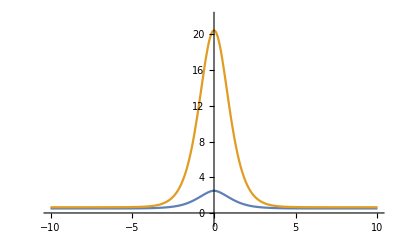

```mathematica
Plot[Evaluate[{
p[1][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t],
p[2][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]
}/.{ω1->0.71,α1->1/2,τ1->1/2,ω2->0.8,α2->2,τ2->1.41,αc->2.96,τc->1.17}],
relevantdomain,PlotRange->{-1,22}]
```

#### Manipulable plot

```mathematica
Manipulate[
Plot[Evaluate[{
p[1][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t],
p[2][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]}],
relevantdomain,PlotRange->All],
Style["Parameters",12],
{{ω1,0.71,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,1/2,"τ_1"},0.1,5},
{{ω2,0.8,"ω_2"},0.1,5},{{α2,2,"α_2"},0.1,5},{{τ2,1.41,"τ_2"},0.1,5},
{{αc,2.96,"α_c"},0.01,5},{{τc,1.17,"τ_c"},0.1,5}
]
```

### Eigenvectors

#### Static values

```mathematica
e[1,1][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]//MatrixForm
```

((Cosh[t/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)))/(αc^2 √(4+(Cosh[t/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/αc^4))
2/(√(4+(Cosh[t/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/αc^4)))

```mathematica
e[2,1][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]//MatrixForm
```

((Cosh[t/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2-√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)))/(αc^2 √(4+(Cosh[t/τc]^4 (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/αc^4))
2/(√(4+(Cosh[t/τc]^4 (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/αc^4)))

#### Manipulable values

```mathematica
Manipulate[
Evaluate[{
e[1,1][ω1,α1,τ1,ω2,α2,τ2,αc,τc][-20]//MatrixForm,
e[2,1][ω1,α1,τ1,ω2,α2,τ2,αc,τc][-20]//MatrixForm}],
Style["Parameters",12],
{{ω1,0.71,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,1/2,"τ_1"},0.1,5},
{{ω2,0.8,"ω_2"},0.1,5},{{α2,2,"α_2"},0.1,5},{{τ2,1.41,"τ_2"},0.1,5},
{{αc,2.96,"α_c"},0.01,5},{{τc,1.17,"τ_c"},0.1,5}
]
```

#### Static plot

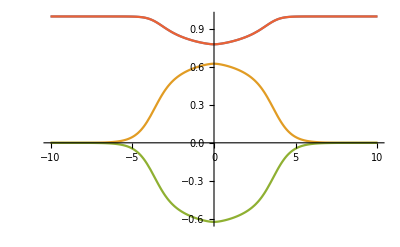

```mathematica
Plot[Evaluate[{
e[1,1][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t],
e[2,1][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]
}/.{ω1->0.71,α1->1/2,τ1->1/2,ω2->0.8,α2->2,τ2->1.41,αc->2.96,τc->1.17}],
relevantdomain,PlotRange->All]
```

#### Manipulable plot

```mathematica
Manipulate[
Plot[Evaluate[{
e[1,1][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t],
e[2,1][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]}],
relevantdomain,PlotRange->All],
Style["Parameters",12],
{{ω1,0.71,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,1/2,"τ_1"},0.1,5},
{{ω2,0.8,"ω_2"},0.1,5},{{α2,2,"α_2"},0.1,5},{{τ2,1.41,"τ_2"},0.1,5},
{{αc,2.96,"α_c"},0.01,5},{{τc,1.17,"τ_c"},0.1,5}
]
```

### Eigenprojectors

#### Static values

```mathematica
mP[1][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]//MatrixForm
```

((Cosh[t/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/(αc^4 (4+(Cosh[t/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/αc^4)) | (2 Cosh[t/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)))/(αc^2 (4+(Cosh[t/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/αc^4))
(2 Cosh[t/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)))/(αc^2 (4+(Cosh[t/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/αc^4)) | 4/(4+(Cosh[t/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/αc^4))

```mathematica
mP[2][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]//MatrixForm
```

((Cosh[t/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2-√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/(αc^4 (4+(Cosh[t/τc]^4 (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/αc^4)) | (2 Cosh[t/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2-√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)))/(αc^2 (4+(Cosh[t/τc]^4 (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/αc^4))
(2 Cosh[t/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2-√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)))/(αc^2 (4+(Cosh[t/τc]^4 (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/αc^4)) | 4/(4+(Cosh[t/τc]^4 (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/αc^4))

#### Manipulable values

```mathematica
Manipulate[
Evaluate[{
mP[1][ω1,α1,τ1,ω2,α2,τ2,αc,τc][-20]//MatrixForm,
mP[2][ω1,α1,τ1,ω2,α2,τ2,αc,τc][-20]//MatrixForm}],
Style["Parameters",12],
{{ω1,0.71,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,1/2,"τ_1"},0.1,5},
{{ω2,0.8,"ω_2"},0.1,5},{{α2,2,"α_2"},0.1,5},{{τ2,1.41,"τ_2"},0.1,5},
{{αc,2.96,"α_c"},0.01,5},{{τc,1.17,"τ_c"},0.1,5}
]
```

#### Static plot

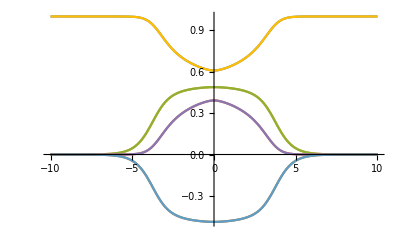

```mathematica
Plot[Evaluate[{
mP[1][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t],
mP[2][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]
}/.{ω1->0.71,α1->1/2,τ1->1/2,ω2->0.8,α2->2,τ2->1.41,αc->2.96,τc->1.17}],
relevantdomain,PlotRange->All]
```

#### Manipulable plot

```mathematica
Manipulate[
Plot[Evaluate[{
mP[1][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t],
mP[2][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]}],
relevantdomain,PlotRange->All],
Style["Parameters",12],
{{ω1,0.71,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,0.5,"τ_1"},0.1,5},
{{ω2,0.8,"ω_2"},0.1,5},{{α2,2,"α_2"},0.1,5},{{τ2,1.41,"τ_2"},0.1,5},
{{αc,2.96,"α_c"},0.01,5},{{τc,1.17,"τ_c"},0.1,5}
]
```

### Kato operator

```mathematica
mU[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]//MatrixForm
```

(Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] | Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])]
-Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] | Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])])

## Fulling’s method, part II ↪︎ Vector coefficients and adiabatic solution

## Computation of the expansion coefficients

### Parallel (∥) / Normal (⊥) decomposition

```mathematica
ClearAll[k,n,t]
```

```mathematica
va[n_,k_][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]=vaP[n,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]+vaN[n,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t];
```

### Order 0

↪︎ Rec. it determines a_0^⊥ but not a_0^∥.

#### ∥ - No new info

a_0^∥=P a_0=a_0->No new info.

#### ⊥ - All zero

a_0^⊥=(1-P)a_0=0

```mathematica
vaN[0,_][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]=v0;
Print[%]
```

{0,0}

### Order 1

↪︎ Rec. it determines a_1^⊥ and a_0^∥, but not a_1^∥.

#### ∥ - Initial eigenvectors

a_0^∥=P a_0=a_0=U(t)a_0(t_i)

```mathematica
vaP[0,k_][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][ti]=∑_(l=1)^nl[k] Subscript[ζ, 0,k,l j/ⅈ] e[k,l][ω1,α1,τ1,ω2,α2,τ2,αc,τc][ti];
Print[%]
```

∑_(l=1)^nl[k] ζ_(0,k,-ⅈ j l) e[k,l][ω1,α1,τ1,ω2,α2,τ2,αc,τc][-10]

```mathematica
vaP[0,k_][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]=∑_(l=1)^nl[k] Subscript[ζ, 0,k,l j/ⅈ] mU[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t].e[k,l][ω1,α1,τ1,ω2,α2,τ2,αc,τc][ti];
Print[%]
```

∑_(l=1)^nl[k] {{Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])],Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])]},{-Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])],Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])]}}.e[k,l][ω1,α1,τ1,ω2,α2,τ2,αc,τc][-10] ζ_(0,k,-ⅈ j l)

We have now determined a_0(t). For each eigenspace reads:

```mathematica
For[k=1,k<=nk,k++,{
Print["va[0,",k,"][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] = ",va[0,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]//MatrixForm]
}]
ClearAll[k]
```

va[0,1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] = (((Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] Cosh[10/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4)))/(αc^2 √(4+(Cosh[10/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4))+(2 Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])])/(√(4+(Cosh[10/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4))) ζ_(0,1,-ⅈ j)
((2 Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])])/(√(4+(Cosh[10/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4))-(Cosh[10/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4)) Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])])/(αc^2 √(4+(Cosh[10/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4))) ζ_(0,1,-ⅈ j))

va[0,2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] = (((Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] Cosh[10/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2-√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4)))/(αc^2 √(4+(Cosh[10/τc]^4 (ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4))+(2 Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])])/(√(4+(Cosh[10/τc]^4 (ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4))) ζ_(0,2,-ⅈ j)
((2 Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])])/(√(4+(Cosh[10/τc]^4 (ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4))-(Cosh[10/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2-√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4)) Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])])/(αc^2 √(4+(Cosh[10/τc]^4 (ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4))) ζ_(0,2,-ⅈ j))

#### ⊥ - Formula for a_1^⊥’s and computations

a_1^⊥:=(1-P) a_1=(M-p)^-1 2(p^(1/2)(a_0'))^⊥,	where  p≡p_k and  a_1≡^k a_1,

and with	(M-p)^-1≡(M-p_k)^-1=(∑_(k'≠k)^nk p_k'-p_k)^-1=(∑_(k'=1)^nk p_k'-2 p_k)^-1,

so	a_1^⊥=(∑_(k'=1)^nk p_k'-2 p_k)^-1 2(p^(1/2)(a_0'))^⊥

```mathematica
(*Before:

vaN[1,k_][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]=((∑_(kk=1)^nk (p[kk][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]-p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]))^-1 2(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^(1/2)(II-mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])).(va[0,k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]'[t])//Simplify

But this direct implementation causes trouble, so I have defined a FirstvaN[k_][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]:= function as a workaround.

Troubles come from the generic-k va[0,k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t] not having mU[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t] act on ∑_(l=1)^nl[k] e[k,l][ω1,α1,τ1,ω2,α2,τ2,αc,τc][ti], which I don't see exactly why leads to problems.

*)
```

```mathematica
FirstvaN[k_][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]:=(∑_(kk=1)^nk p[kk][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]-2p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^-1 2(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^(1/2)(II-mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]).va[0,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t]
```

```mathematica
For[k=1,k<=nk,k++,
vaN[1,k][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]=FirstvaN[k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t](*//Simplify*)
]
ClearAll[k];
```

↪︎ Not sure if the //Simplify takes forever or doesn’t compute; leave it more.

```mathematica
For[k=1,k<=nk,k++,{
Print["vaN[1,",k,"][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] = ",vaN[1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]//MatrixForm]
}]
ClearAll[k]
```

vaN[1,1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] = ((√2 √(ω1^2+ω2^2+α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+2 αc^2 Sech[t/τc]^2-√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)) (-(2 Cosh[t/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)) ζ_(0,1,-ⅈ j) (-(Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] Cosh[10/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4)) (-(2 αc^2 Sech[t/τc]^2 (-(2 α1^2 Sech[t/τ1]^2 Tanh[t/τ1])/τ1+(2 α2^2 Sech[t/τ2]^2 Tanh[t/τ2])/τ2))/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)-(4 αc^2 Sech[t/τc]^2 Tanh[t/τc])/(τc (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2))))/(2 αc^2 √(4+(Cosh[10/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4) (1+(4 αc^4 Sech[t/τc]^4)/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)))-(Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] (-(2 αc^2 Sech[t/τc]^2 (-(2 α1^2 Sech[t/τ1]^2 Tanh[t/τ1])/τ1+(2 α2^2 Sech[t/τ2]^2 Tanh[t/τ2])/τ2))/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)-(4 αc^2 Sech[t/τc]^2 Tanh[t/τc])/(τc (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2))))/(√(4+(Cosh[10/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4) (1+(4 αc^4 Sech[t/τc]^4)/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)))))/(αc^2 (4+(Cosh[t/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/αc^4))+(1-(Cosh[t/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/(αc^4 (4+(Cosh[t/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/αc^4))) ζ_(0,1,-ⅈ j) ((Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] (-(2 αc^2 Sech[t/τc]^2 (-(2 α1^2 Sech[t/τ1]^2 Tanh[t/τ1])/τ1+(2 α2^2 Sech[t/τ2]^2 Tanh[t/τ2])/τ2))/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)-(4 αc^2 Sech[t/τc]^2 Tanh[t/τc])/(τc (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2))))/(√(4+(Cosh[10/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4) (1+(4 αc^4 Sech[t/τc]^4)/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)))-(Cosh[10/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4)) Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] (-(2 αc^2 Sech[t/τc]^2 (-(2 α1^2 Sech[t/τ1]^2 Tanh[t/τ1])/τ1+(2 α2^2 Sech[t/τ2]^2 Tanh[t/τ2])/τ2))/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)-(4 αc^2 Sech[t/τc]^2 Tanh[t/τc])/(τc (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2))))/(2 αc^2 √(4+(Cosh[10/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4) (1+(4 αc^4 Sech[t/τc]^4)/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2))))))/(-ω1^2-ω2^2-α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2-2 αc^2 Sech[t/τc]^2+√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)+1/2 (ω1^2+ω2^2+α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+2 αc^2 Sech[t/τc]^2-√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))+1/2 (ω1^2+ω2^2+α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+2 αc^2 Sech[t/τc]^2+√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)))
(√2 √(ω1^2+ω2^2+α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+2 αc^2 Sech[t/τc]^2-√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)) ((1-4/(4+(Cosh[t/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/αc^4)) ζ_(0,1,-ⅈ j) (-(Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] Cosh[10/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4)) (-(2 αc^2 Sech[t/τc]^2 (-(2 α1^2 Sech[t/τ1]^2 Tanh[t/τ1])/τ1+(2 α2^2 Sech[t/τ2]^2 Tanh[t/τ2])/τ2))/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)-(4 αc^2 Sech[t/τc]^2 Tanh[t/τc])/(τc (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2))))/(2 αc^2 √(4+(Cosh[10/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4) (1+(4 αc^4 Sech[t/τc]^4)/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)))-(Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] (-(2 αc^2 Sech[t/τc]^2 (-(2 α1^2 Sech[t/τ1]^2 Tanh[t/τ1])/τ1+(2 α2^2 Sech[t/τ2]^2 Tanh[t/τ2])/τ2))/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)-(4 αc^2 Sech[t/τc]^2 Tanh[t/τc])/(τc (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2))))/(√(4+(Cosh[10/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4) (1+(4 αc^4 Sech[t/τc]^4)/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2))))-(2 Cosh[t/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)) ζ_(0,1,-ⅈ j) ((Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] (-(2 αc^2 Sech[t/τc]^2 (-(2 α1^2 Sech[t/τ1]^2 Tanh[t/τ1])/τ1+(2 α2^2 Sech[t/τ2]^2 Tanh[t/τ2])/τ2))/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)-(4 αc^2 Sech[t/τc]^2 Tanh[t/τc])/(τc (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2))))/(√(4+(Cosh[10/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4) (1+(4 αc^4 Sech[t/τc]^4)/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)))-(Cosh[10/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4)) Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] (-(2 αc^2 Sech[t/τc]^2 (-(2 α1^2 Sech[t/τ1]^2 Tanh[t/τ1])/τ1+(2 α2^2 Sech[t/τ2]^2 Tanh[t/τ2])/τ2))/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)-(4 αc^2 Sech[t/τc]^2 Tanh[t/τc])/(τc (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2))))/(2 αc^2 √(4+(Cosh[10/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4) (1+(4 αc^4 Sech[t/τc]^4)/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)))))/(αc^2 (4+(Cosh[t/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/αc^4))))/(-ω1^2-ω2^2-α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2-2 αc^2 Sech[t/τc]^2+√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)+1/2 (ω1^2+ω2^2+α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+2 αc^2 Sech[t/τc]^2-√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))+1/2 (ω1^2+ω2^2+α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+2 αc^2 Sech[t/τc]^2+√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))))

vaN[1,2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] = ((√2 √(ω1^2+ω2^2+α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+2 αc^2 Sech[t/τc]^2+√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)) (-(2 Cosh[t/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2-√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)) ζ_(0,2,-ⅈ j) (-(Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] Cosh[10/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2-√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4)) (-(2 αc^2 Sech[t/τc]^2 (-(2 α1^2 Sech[t/τ1]^2 Tanh[t/τ1])/τ1+(2 α2^2 Sech[t/τ2]^2 Tanh[t/τ2])/τ2))/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)-(4 αc^2 Sech[t/τc]^2 Tanh[t/τc])/(τc (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2))))/(2 αc^2 √(4+(Cosh[10/τc]^4 (ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4) (1+(4 αc^4 Sech[t/τc]^4)/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)))-(Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] (-(2 αc^2 Sech[t/τc]^2 (-(2 α1^2 Sech[t/τ1]^2 Tanh[t/τ1])/τ1+(2 α2^2 Sech[t/τ2]^2 Tanh[t/τ2])/τ2))/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)-(4 αc^2 Sech[t/τc]^2 Tanh[t/τc])/(τc (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2))))/(√(4+(Cosh[10/τc]^4 (ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4) (1+(4 αc^4 Sech[t/τc]^4)/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)))))/(αc^2 (4+(Cosh[t/τc]^4 (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/αc^4))+(1-(Cosh[t/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2-√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/(αc^4 (4+(Cosh[t/τc]^4 (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/αc^4))) ζ_(0,2,-ⅈ j) ((Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] (-(2 αc^2 Sech[t/τc]^2 (-(2 α1^2 Sech[t/τ1]^2 Tanh[t/τ1])/τ1+(2 α2^2 Sech[t/τ2]^2 Tanh[t/τ2])/τ2))/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)-(4 αc^2 Sech[t/τc]^2 Tanh[t/τc])/(τc (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2))))/(√(4+(Cosh[10/τc]^4 (ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4) (1+(4 αc^4 Sech[t/τc]^4)/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)))-(Cosh[10/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2-√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4)) Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] (-(2 αc^2 Sech[t/τc]^2 (-(2 α1^2 Sech[t/τ1]^2 Tanh[t/τ1])/τ1+(2 α2^2 Sech[t/τ2]^2 Tanh[t/τ2])/τ2))/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)-(4 αc^2 Sech[t/τc]^2 Tanh[t/τc])/(τc (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2))))/(2 αc^2 √(4+(Cosh[10/τc]^4 (ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4) (1+(4 αc^4 Sech[t/τc]^4)/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2))))))/(-ω1^2-ω2^2-α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2-2 αc^2 Sech[t/τc]^2-√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)+1/2 (ω1^2+ω2^2+α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+2 αc^2 Sech[t/τc]^2-√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))+1/2 (ω1^2+ω2^2+α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+2 αc^2 Sech[t/τc]^2+√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)))
(√2 √(ω1^2+ω2^2+α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+2 αc^2 Sech[t/τc]^2+√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)) ((1-4/(4+(Cosh[t/τc]^4 (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/αc^4)) ζ_(0,2,-ⅈ j) (-(Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] Cosh[10/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2-√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4)) (-(2 αc^2 Sech[t/τc]^2 (-(2 α1^2 Sech[t/τ1]^2 Tanh[t/τ1])/τ1+(2 α2^2 Sech[t/τ2]^2 Tanh[t/τ2])/τ2))/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)-(4 αc^2 Sech[t/τc]^2 Tanh[t/τc])/(τc (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2))))/(2 αc^2 √(4+(Cosh[10/τc]^4 (ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4) (1+(4 αc^4 Sech[t/τc]^4)/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)))-(Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] (-(2 αc^2 Sech[t/τc]^2 (-(2 α1^2 Sech[t/τ1]^2 Tanh[t/τ1])/τ1+(2 α2^2 Sech[t/τ2]^2 Tanh[t/τ2])/τ2))/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)-(4 αc^2 Sech[t/τc]^2 Tanh[t/τc])/(τc (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2))))/(√(4+(Cosh[10/τc]^4 (ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4) (1+(4 αc^4 Sech[t/τc]^4)/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2))))-(2 Cosh[t/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2-√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)) ζ_(0,2,-ⅈ j) ((Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] (-(2 αc^2 Sech[t/τc]^2 (-(2 α1^2 Sech[t/τ1]^2 Tanh[t/τ1])/τ1+(2 α2^2 Sech[t/τ2]^2 Tanh[t/τ2])/τ2))/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)-(4 αc^2 Sech[t/τc]^2 Tanh[t/τc])/(τc (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2))))/(√(4+(Cosh[10/τc]^4 (ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4) (1+(4 αc^4 Sech[t/τc]^4)/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)))-(Cosh[10/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2-√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4)) Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] (-(2 αc^2 Sech[t/τc]^2 (-(2 α1^2 Sech[t/τ1]^2 Tanh[t/τ1])/τ1+(2 α2^2 Sech[t/τ2]^2 Tanh[t/τ2])/τ2))/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)-(4 αc^2 Sech[t/τc]^2 Tanh[t/τc])/(τc (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2))))/(2 αc^2 √(4+(Cosh[10/τc]^4 (ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4) (1+(4 αc^4 Sech[t/τc]^4)/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)))))/(αc^2 (4+(Cosh[t/τc]^4 (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/αc^4))))/(-ω1^2-ω2^2-α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2-2 αc^2 Sech[t/τc]^2-√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)+1/2 (ω1^2+ω2^2+α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+2 αc^2 Sech[t/τc]^2-√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))+1/2 (ω1^2+ω2^2+α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+2 αc^2 Sech[t/τc]^2+√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))))

### Higher order recurrent relations

#### ∥ - Formula for ^k a_n^∥ in terms of ^k(a_(n-1))^∥’s and ^k a_n^⊥’s

a_n^∥=P a_n=U(t)(P a_n(t_i))+U(t)∫_ti^t ⅆ t_1U(t_1)^-1[-1/2 p^(-1/2)P (a_(n-1)'')+1/4 p^(-3/2)p'P (a_(n-1)')+1/2 p^(1/2)(p''/(4 p^2)-(5(p')^2)/(16 p^3))P (a_(n-1))-P ((a_n^⊥)')]

```mathematica
HOvaP[n_,k_][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]:=mU[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t].∑_(l=1)^nl[k] Subscript[ζ, n,k,+l j/ⅈ] e[k,l][ω1,α1,τ1,ω2,α2,τ2,αc,τc][ti]+mU[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t].∫_ti^t mUinv[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1].(-1/2(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1])^(-1/2)mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1].va[n-1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]''[t1]+1/4(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1])^(-3/2)p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]'[t1]mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1].va[n-1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t1]+1/2(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1])^(1/2)((p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]''[t1])/(4p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1]^2)-(5p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]'[t1]^2)/(16p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1]^3))mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1].va[n-1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t1]-mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1].vaN[n,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t1])ⅆt1//Simplify
```

#### ⊥ - Formula for ^k a_n^⊥ in terms of ^k(a_(n-1))^⊥’s and ^k(a_(n-2))^⊥’s

a_n^⊥=(1-P) a_n=(M-p)^-1[2 p^(1/2) (a_(n-1)')^⊥-p'/(2p)(a_(n-2)')^⊥+(a_(n-2)'')^⊥-p(p''/(4 p^2)-(5(p')^2)/(16 p^3))(a_(n-2))^⊥],	with (M-p)^-1=(∑_(k'=1)^nk p_k'-p)^-1

```mathematica
HOvaN[n_,k_][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]:=(∑_(kp=1)^nk (p[kp][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]-p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]))^-1(2(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^(1/2) (II.mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]).(va[n-1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t])-(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]'[t])/(2p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])(II.mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]).(va[n-2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t])+(II.mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]).(va[n-2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]''[t])-p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]((p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]''[t])/(4(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^2)-(5(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]'[t])^2)/(16(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^3))(II.mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]).(va[n-2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]))//Simplify
```

### Order 2 ↪︎ Integrals here seem to not compute (Obs: I didn’t let them that much time)

↪︎ Rec. it determines a_2^⊥ and a_1^∥, but not a_2^∥.

#### ∥ - Computation of ^k a_1^∥’s

```mathematica
(*For[k=1,k<=nk,k++,
vaP[1,k][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]=HOvaP[1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]
]*)
```

↪︎	Integrals here seem to not compute. Hence, we don’t achieve analytical expressions for
	vaP[n>=1][k][t],  nor  vaN[n>=2][k][t].

(Obs: I didn’t leave the integrals too much time, nor tried to see where the error was.)

```mathematica
For[k=1,k<=nk,k++,{
Print["vaP[1][",k,"][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] = ",vaP[1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]//MatrixForm]
}]
ClearAll[k]
```

vaP[1][1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] = vaP[1,1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]

vaP[1][2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] = vaP[1,2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]

#### ⊥ - Computation of ^k a_2^⊥’s

```mathematica
(*For[k=1,k<=nk,k++,
vaN[2,k][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]=HOvaN[2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]
]*)
```

```mathematica
For[k=1,k<=nk,k++,{
Print["vaN[2,",k,"][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] = ",vaN[2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]//MatrixForm]
}]
ClearAll[k]
```

vaN[2,1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] = vaN[2,1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]

vaN[2,2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] = vaN[2,2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]

### Order 3

↪︎ Rec. it determines a_3^⊥ and a_2^∥, but not a_3^∥.

#### ∥ - Computation of ^k a_2^∥’s

```mathematica
(*For[k=1,k<=nk,k++,
vaP[2,k][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]=HOvaP[2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]
]*)
```

```mathematica
For[k=1,k<=nk,k++,{
Print["vaP[2][",k,"][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] = ",vaP[2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]//MatrixForm]
}]
ClearAll[k]
```

vaP[2][1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] = vaP[2,1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]

vaP[2][2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] = vaP[2,2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]

#### ⊥ - Computation of ^k a_3^⊥’s

```mathematica
(*For[k=1,k<=nk,k++,
vaN[3,k][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]=HOvaN[3,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]
]*)
```

```mathematica
For[k=1,k<=nk,k++,{
Print["vaN[3,",k,"][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] = ",vaN[3,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]//MatrixForm]
}]
ClearAll[k]
```

vaN[3,1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] = vaN[3,1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]

vaN[3,2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] = vaN[3,2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]

### Higher order integrals don’t compute ↪︎ Stay analytically at order 0

Since we couldn’t compute the integrals for the higher orders yet, let’s keep the desired order for numerics, and everything else at zeroth order:

```mathematica
adbOrdNum=adbOrd;
```

```mathematica
adbOrd=0;
```

### All-orders final solutions for the vector coefficients (just printing) up to where we reach analytically

#### ∥ vector coefficients

Up to truncated analytical adiabatic order adbOrd=

```mathematica
adbOrd
```

0

```mathematica
For[n=0,n<=adbOrd,n++,{
For[k=1,k<=nk,k++,{
Print["vaP[",n,"][",k,"][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] = ",vaP[n,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]//MatrixForm]
}]
}]
ClearAll[k,n]
```

vaP[0][1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] = (((Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] Cosh[10/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4)))/(αc^2 √(4+(Cosh[10/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4))+(2 Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])])/(√(4+(Cosh[10/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4))) ζ_(0,1,-ⅈ j)
((2 Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])])/(√(4+(Cosh[10/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4))-(Cosh[10/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4)) Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])])/(αc^2 √(4+(Cosh[10/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4))) ζ_(0,1,-ⅈ j))

vaP[0][2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] = (((Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] Cosh[10/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2-√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4)))/(αc^2 √(4+(Cosh[10/τc]^4 (ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4))+(2 Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])])/(√(4+(Cosh[10/τc]^4 (ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4))) ζ_(0,2,-ⅈ j)
((2 Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])])/(√(4+(Cosh[10/τc]^4 (ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4))-(Cosh[10/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2-√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4)) Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])])/(αc^2 √(4+(Cosh[10/τc]^4 (ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4))) ζ_(0,2,-ⅈ j))

#### ⊥ vector coefficients

Up to truncated analytical adiabatic order plus one, adbOrd+1=

```mathematica
adbOrd+1
```

1

```mathematica
For[n=0,n<=adbOrd+1,n++,{
For[k=1,k<=nk,k++,{
Print["vaN[",n,"][",k,"][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] = ",vaN[n,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]//MatrixForm]
}]
}]
ClearAll[k,n]
```

vaN[0][1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] = (0
0)

vaN[0][2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] = (0
0)

vaN[1][1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] = ((√2 √(ω1^2+ω2^2+α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+2 αc^2 Sech[t/τc]^2-√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)) (-(2 Cosh[t/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)) ζ_(0,1,-ⅈ j) (-(Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] Cosh[10/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4)) (-(2 αc^2 Sech[t/τc]^2 (-(2 α1^2 Sech[t/τ1]^2 Tanh[t/τ1])/τ1+(2 α2^2 Sech[t/τ2]^2 Tanh[t/τ2])/τ2))/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)-(4 αc^2 Sech[t/τc]^2 Tanh[t/τc])/(τc (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2))))/(2 αc^2 √(4+(Cosh[10/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4) (1+(4 αc^4 Sech[t/τc]^4)/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)))-(Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] (-(2 αc^2 Sech[t/τc]^2 (-(2 α1^2 Sech[t/τ1]^2 Tanh[t/τ1])/τ1+(2 α2^2 Sech[t/τ2]^2 Tanh[t/τ2])/τ2))/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)-(4 αc^2 Sech[t/τc]^2 Tanh[t/τc])/(τc (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2))))/(√(4+(Cosh[10/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4) (1+(4 αc^4 Sech[t/τc]^4)/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)))))/(αc^2 (4+(Cosh[t/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/αc^4))+(1-(Cosh[t/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/(αc^4 (4+(Cosh[t/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/αc^4))) ζ_(0,1,-ⅈ j) ((Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] (-(2 αc^2 Sech[t/τc]^2 (-(2 α1^2 Sech[t/τ1]^2 Tanh[t/τ1])/τ1+(2 α2^2 Sech[t/τ2]^2 Tanh[t/τ2])/τ2))/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)-(4 αc^2 Sech[t/τc]^2 Tanh[t/τc])/(τc (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2))))/(√(4+(Cosh[10/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4) (1+(4 αc^4 Sech[t/τc]^4)/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)))-(Cosh[10/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4)) Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] (-(2 αc^2 Sech[t/τc]^2 (-(2 α1^2 Sech[t/τ1]^2 Tanh[t/τ1])/τ1+(2 α2^2 Sech[t/τ2]^2 Tanh[t/τ2])/τ2))/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)-(4 αc^2 Sech[t/τc]^2 Tanh[t/τc])/(τc (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2))))/(2 αc^2 √(4+(Cosh[10/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4) (1+(4 αc^4 Sech[t/τc]^4)/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2))))))/(-ω1^2-ω2^2-α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2-2 αc^2 Sech[t/τc]^2+√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)+1/2 (ω1^2+ω2^2+α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+2 αc^2 Sech[t/τc]^2-√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))+1/2 (ω1^2+ω2^2+α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+2 αc^2 Sech[t/τc]^2+√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)))
(√2 √(ω1^2+ω2^2+α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+2 αc^2 Sech[t/τc]^2-√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)) ((1-4/(4+(Cosh[t/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/αc^4)) ζ_(0,1,-ⅈ j) (-(Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] Cosh[10/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4)) (-(2 αc^2 Sech[t/τc]^2 (-(2 α1^2 Sech[t/τ1]^2 Tanh[t/τ1])/τ1+(2 α2^2 Sech[t/τ2]^2 Tanh[t/τ2])/τ2))/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)-(4 αc^2 Sech[t/τc]^2 Tanh[t/τc])/(τc (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2))))/(2 αc^2 √(4+(Cosh[10/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4) (1+(4 αc^4 Sech[t/τc]^4)/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)))-(Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] (-(2 αc^2 Sech[t/τc]^2 (-(2 α1^2 Sech[t/τ1]^2 Tanh[t/τ1])/τ1+(2 α2^2 Sech[t/τ2]^2 Tanh[t/τ2])/τ2))/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)-(4 αc^2 Sech[t/τc]^2 Tanh[t/τc])/(τc (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2))))/(√(4+(Cosh[10/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4) (1+(4 αc^4 Sech[t/τc]^4)/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2))))-(2 Cosh[t/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)) ζ_(0,1,-ⅈ j) ((Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] (-(2 αc^2 Sech[t/τc]^2 (-(2 α1^2 Sech[t/τ1]^2 Tanh[t/τ1])/τ1+(2 α2^2 Sech[t/τ2]^2 Tanh[t/τ2])/τ2))/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)-(4 αc^2 Sech[t/τc]^2 Tanh[t/τc])/(τc (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2))))/(√(4+(Cosh[10/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4) (1+(4 αc^4 Sech[t/τc]^4)/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)))-(Cosh[10/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4)) Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] (-(2 αc^2 Sech[t/τc]^2 (-(2 α1^2 Sech[t/τ1]^2 Tanh[t/τ1])/τ1+(2 α2^2 Sech[t/τ2]^2 Tanh[t/τ2])/τ2))/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)-(4 αc^2 Sech[t/τc]^2 Tanh[t/τc])/(τc (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2))))/(2 αc^2 √(4+(Cosh[10/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4) (1+(4 αc^4 Sech[t/τc]^4)/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)))))/(αc^2 (4+(Cosh[t/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/αc^4))))/(-ω1^2-ω2^2-α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2-2 αc^2 Sech[t/τc]^2+√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)+1/2 (ω1^2+ω2^2+α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+2 αc^2 Sech[t/τc]^2-√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))+1/2 (ω1^2+ω2^2+α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+2 αc^2 Sech[t/τc]^2+√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))))

vaN[1][2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] = ((√2 √(ω1^2+ω2^2+α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+2 αc^2 Sech[t/τc]^2+√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)) (-(2 Cosh[t/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2-√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)) ζ_(0,2,-ⅈ j) (-(Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] Cosh[10/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2-√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4)) (-(2 αc^2 Sech[t/τc]^2 (-(2 α1^2 Sech[t/τ1]^2 Tanh[t/τ1])/τ1+(2 α2^2 Sech[t/τ2]^2 Tanh[t/τ2])/τ2))/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)-(4 αc^2 Sech[t/τc]^2 Tanh[t/τc])/(τc (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2))))/(2 αc^2 √(4+(Cosh[10/τc]^4 (ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4) (1+(4 αc^4 Sech[t/τc]^4)/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)))-(Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] (-(2 αc^2 Sech[t/τc]^2 (-(2 α1^2 Sech[t/τ1]^2 Tanh[t/τ1])/τ1+(2 α2^2 Sech[t/τ2]^2 Tanh[t/τ2])/τ2))/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)-(4 αc^2 Sech[t/τc]^2 Tanh[t/τc])/(τc (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2))))/(√(4+(Cosh[10/τc]^4 (ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4) (1+(4 αc^4 Sech[t/τc]^4)/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)))))/(αc^2 (4+(Cosh[t/τc]^4 (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/αc^4))+(1-(Cosh[t/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2-√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/(αc^4 (4+(Cosh[t/τc]^4 (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/αc^4))) ζ_(0,2,-ⅈ j) ((Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] (-(2 αc^2 Sech[t/τc]^2 (-(2 α1^2 Sech[t/τ1]^2 Tanh[t/τ1])/τ1+(2 α2^2 Sech[t/τ2]^2 Tanh[t/τ2])/τ2))/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)-(4 αc^2 Sech[t/τc]^2 Tanh[t/τc])/(τc (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2))))/(√(4+(Cosh[10/τc]^4 (ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4) (1+(4 αc^4 Sech[t/τc]^4)/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)))-(Cosh[10/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2-√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4)) Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] (-(2 αc^2 Sech[t/τc]^2 (-(2 α1^2 Sech[t/τ1]^2 Tanh[t/τ1])/τ1+(2 α2^2 Sech[t/τ2]^2 Tanh[t/τ2])/τ2))/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)-(4 αc^2 Sech[t/τc]^2 Tanh[t/τc])/(τc (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2))))/(2 αc^2 √(4+(Cosh[10/τc]^4 (ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4) (1+(4 αc^4 Sech[t/τc]^4)/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2))))))/(-ω1^2-ω2^2-α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2-2 αc^2 Sech[t/τc]^2-√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)+1/2 (ω1^2+ω2^2+α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+2 αc^2 Sech[t/τc]^2-√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))+1/2 (ω1^2+ω2^2+α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+2 αc^2 Sech[t/τc]^2+√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)))
(√2 √(ω1^2+ω2^2+α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+2 αc^2 Sech[t/τc]^2+√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)) ((1-4/(4+(Cosh[t/τc]^4 (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/αc^4)) ζ_(0,2,-ⅈ j) (-(Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] Cosh[10/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2-√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4)) (-(2 αc^2 Sech[t/τc]^2 (-(2 α1^2 Sech[t/τ1]^2 Tanh[t/τ1])/τ1+(2 α2^2 Sech[t/τ2]^2 Tanh[t/τ2])/τ2))/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)-(4 αc^2 Sech[t/τc]^2 Tanh[t/τc])/(τc (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2))))/(2 αc^2 √(4+(Cosh[10/τc]^4 (ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4) (1+(4 αc^4 Sech[t/τc]^4)/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)))-(Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] (-(2 αc^2 Sech[t/τc]^2 (-(2 α1^2 Sech[t/τ1]^2 Tanh[t/τ1])/τ1+(2 α2^2 Sech[t/τ2]^2 Tanh[t/τ2])/τ2))/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)-(4 αc^2 Sech[t/τc]^2 Tanh[t/τc])/(τc (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2))))/(√(4+(Cosh[10/τc]^4 (ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4) (1+(4 αc^4 Sech[t/τc]^4)/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2))))-(2 Cosh[t/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2-√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)) ζ_(0,2,-ⅈ j) ((Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] (-(2 αc^2 Sech[t/τc]^2 (-(2 α1^2 Sech[t/τ1]^2 Tanh[t/τ1])/τ1+(2 α2^2 Sech[t/τ2]^2 Tanh[t/τ2])/τ2))/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)-(4 αc^2 Sech[t/τc]^2 Tanh[t/τc])/(τc (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2))))/(√(4+(Cosh[10/τc]^4 (ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4) (1+(4 αc^4 Sech[t/τc]^4)/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)))-(Cosh[10/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2-√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4)) Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] (-(2 αc^2 Sech[t/τc]^2 (-(2 α1^2 Sech[t/τ1]^2 Tanh[t/τ1])/τ1+(2 α2^2 Sech[t/τ2]^2 Tanh[t/τ2])/τ2))/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)-(4 αc^2 Sech[t/τc]^2 Tanh[t/τc])/(τc (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2))))/(2 αc^2 √(4+(Cosh[10/τc]^4 (ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4) (1+(4 αc^4 Sech[t/τc]^4)/((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2)))))/(αc^2 (4+(Cosh[t/τc]^4 (ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))^2)/αc^4))))/(-ω1^2-ω2^2-α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2-2 αc^2 Sech[t/τc]^2-√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)+1/2 (ω1^2+ω2^2+α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+2 αc^2 Sech[t/τc]^2-√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))+1/2 (ω1^2+ω2^2+α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+2 αc^2 Sech[t/τc]^2+√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4))))

Obs: Note that here in the perpendicular part we reach one order higher than in the parallel one. We won’t use it though, since we’d need the parallel part to compute the full vector coefficient.

#### Complete vector coefficients (∥ + ⊥)

Up to truncated analytical adiabatic order adbOrd=

```mathematica
adbOrd
```

0

```mathematica
For[n=0,n<=adbOrd,n++,{
For[k=1,k<=nk,k++,{
Print["va[",n,",",k,"][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] = ",va[n,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]//MatrixForm]
}]
}]
ClearAll[k,n]
```

va[0,1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] = (((Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] Cosh[10/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4)))/(αc^2 √(4+(Cosh[10/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4))+(2 Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])])/(√(4+(Cosh[10/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4))) ζ_(0,1,-ⅈ j)
((2 Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])])/(√(4+(Cosh[10/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4))-(Cosh[10/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4)) Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])])/(αc^2 √(4+(Cosh[10/τc]^4 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4))) ζ_(0,1,-ⅈ j))

va[0,2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] = (((Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] Cosh[10/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2-√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4)))/(αc^2 √(4+(Cosh[10/τc]^4 (ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4))+(2 Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])])/(√(4+(Cosh[10/τc]^4 (ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4))) ζ_(0,2,-ⅈ j)
((2 Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])])/(√(4+(Cosh[10/τc]^4 (ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4))-(Cosh[10/τc]^2 (-ω1^2+ω2^2-α1^2 Sech[10/τ1]^2+α2^2 Sech[10/τ2]^2-√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4)) Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])])/(αc^2 √(4+(Cosh[10/τc]^4 (ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2+√((ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)^2+4 αc^4 Sech[10/τc]^4))^2)/αc^4))) ζ_(0,2,-ⅈ j))

### List of all integration constants ζ_(n,k,±l)

#### Recall: Constants notation

- Constants:	ζ_(n,k,±l)->	 n: order n,
					 k: eigenspace k,
					 ±: solution +/- (i.e. j->±ⅈ)
					 l: proportional to eigenvector e_k^(l)[t]

#### List with all constants

```mathematica
constsList={};
For[n=0,n<=(*adbOrd*)2,n++,
For[k=1,k<=nk,k++,
For[l=1,l<=nl[k],l++,
AppendTo[constsList,Subscript[ζ, n,k,+l]];
AppendTo[constsList,Subscript[ζ, n,k,-l]];
]]]
ClearAll[n,k,l]
constsList
```

{ζ_(0,1,1),ζ_(0,1,-1),ζ_(0,2,1),ζ_(0,2,-1),ζ_(1,1,1),ζ_(1,1,-1),ζ_(1,2,1),ζ_(1,2,-1),ζ_(2,1,1),ζ_(2,1,-1),ζ_(2,2,1),ζ_(2,2,-1)}

#### List with all j-constants (manual)

```mathematica
constsjList={Subscript[ζ, 0,1,-ⅈ j],Subscript[ζ, 0,2,-ⅈ j],Subscript[ζ, 1,1,-ⅈ j],Subscript[ζ, 1,2,-ⅈ j],Subscript[ζ, 2,1,-ⅈ j],Subscript[ζ, 2,2,-ⅈ j]};
```

#### Lists of constants up to each order (manual)

```mathematica
constsListUpto[0]={};
For[n=0,n<=0,n++,
For[k=1,k<=nk,k++,
For[l=1,l<=nl[k],l++,
AppendTo[constsListUpto[0],Subscript[ζ, n,k,+l]];
AppendTo[constsListUpto[0],Subscript[ζ, n,k,-l]];
]]]
ClearAll[n,k,l]
constsListUpto[0]
```

{ζ_(0,1,1),ζ_(0,1,-1),ζ_(0,2,1),ζ_(0,2,-1)}

```mathematica
constsListUpto[1]={};
For[n=0,n<=1,n++,
For[k=1,k<=nk,k++,
For[l=1,l<=nl[k],l++,
AppendTo[constsListUpto[1],Subscript[ζ, n,k,+l]];
AppendTo[constsListUpto[1],Subscript[ζ, n,k,-l]];
]]]
ClearAll[n,k,l]
constsListUpto[1]
```

{ζ_(0,1,1),ζ_(0,1,-1),ζ_(0,2,1),ζ_(0,2,-1),ζ_(1,1,1),ζ_(1,1,-1),ζ_(1,2,1),ζ_(1,2,-1)}

```mathematica
constsListUpto[2]={};
For[n=0,n<=2,n++,
For[k=1,k<=nk,k++,
For[l=1,l<=nl[k],l++,
AppendTo[constsListUpto[2],Subscript[ζ, n,k,+l]];
AppendTo[constsListUpto[2],Subscript[ζ, n,k,-l]];
]]]
ClearAll[n,k,l]
constsListUpto[2]
```

{ζ_(0,1,1),ζ_(0,1,-1),ζ_(0,2,1),ζ_(0,2,-1),ζ_(1,1,1),ζ_(1,1,-1),ζ_(1,2,1),ζ_(1,2,-1),ζ_(2,1,1),ζ_(2,1,-1),ζ_(2,2,1),ζ_(2,2,-1)}

#### Lists of constants of each order (manual)

```mathematica
constsListOrder[0]={Subscript[ζ, 0,1,1],Subscript[ζ, 0,1,-1],Subscript[ζ, 0,2,1],Subscript[ζ, 0,2,-1]};
```

```mathematica
constsListOrder[1]={Subscript[ζ, 1,1,1],Subscript[ζ, 1,1,-1],Subscript[ζ, 1,2,1],Subscript[ζ, 1,2,-1]};
```

```mathematica
constsListOrder[2]={Subscript[ζ, 2,1,1],Subscript[ζ, 2,1,-1],Subscript[ζ, 2,2,1],Subscript[ζ, 2,2,-1]};
```

## Key integrals for the specified model

### Integration of the components of the Kato’s transformation U(t)

In this case they did compute, giving:

```mathematica
Print[mU[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]//MatrixForm]
```

(Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] | Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])]
-Sin[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])] | Cos[1/2 (-ArcTan[(2 αc^2 Sech[10/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[10/τ1]^2-α2^2 Sech[10/τ2]^2)]+ArcTan[(2 αc^2 Sech[t/τc]^2)/(ω1^2-ω2^2+α1^2 Sech[t/τ1]^2-α2^2 Sech[t/τ2]^2)])])

### Integration of the eigenvectors’ roots

These do not compute, so we need to bypass them semi-analytically with through (Parametric)NDSolve.

```mathematica
Print[√(p[1][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])]
```

(√(ω1^2+ω2^2+α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+2 αc^2 Sech[t/τc]^2-√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)))/(√2)

```mathematica
(*∫√(p[1][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])ⅆt*)
```

```mathematica
Print[√(p[2][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])]
```

(√(ω1^2+ω2^2+α1^2 Sech[t/τ1]^2+α2^2 Sech[t/τ2]^2+2 αc^2 Sech[t/τc]^2+√((ω1^2+α1^2 Sech[t/τ1]^2)^2-2 (ω1^2+α1^2 Sech[t/τ1]^2) (ω2^2+α2^2 Sech[t/τ2]^2)+(ω2^2+α2^2 Sech[t/τ2]^2)^2+4 αc^4 Sech[t/τc]^4)))/(√2)

```mathematica
(*∫√(p[2][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])ⅆt*)
```

### Integration in the higher order parallel recurrence relation

These do not compute either, so we can only “compute” vector coefficients at 0th order (they are just eigenvectors, here given by the Kato evolution of initial eigenvectors). For the 1st order parallel coefficients we already need to go to equations/relations at 2nd order, and those don’t compute. They were:

```mathematica
(*For[k=1,k<=nk,k++,
vaP[1,k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t_]=HOvaP[1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]
]*)
```

## Adiabatic general solution (fully analytic; disabled here)

For this model, we not only lack the analytical expression for higher order expansion coefficients, but also for the zeroth order exponents, the eigenvalues’ roots’ integrals. Hence, we lack any form of analytical adiabatic solution, not even at the truncated analytical adiabatic order adbOrd.

### General adiabatic solution

#### Each eigenspace solution (just printing)

```mathematica
Definition[VecAdbAnstz]
```

VecAdbAnstz[o_,k_][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]:=(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^(-1/4) Exp[j T (∫√(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])ⅆt+iph[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc])] ∑_(n=0)^o (j T)^-n va[n,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]

```mathematica
(*For[k=1,k<=nk,k++,
Print["VecAdbAnstz[adbOrd=2,k=",k,"][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] = ",VecAdbAnstz[adbOrd,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]//MatrixForm]
]*)
```

#### General solution (computing and printing)

```mathematica
Definition[VecAdbGralExp]
```

VecAdbGralExp[o_][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]:=(∑_(k=1)^nk VecAdbAnstz[o,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.j→+ⅈ)+(∑_(k=1)^nk VecAdbAnstz[o,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.j→-ⅈ)

```mathematica
(*For[n=0,n<=adbOrd,n++,
vxAdbGral[n][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]=VecAdbGralExp[n][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]]
ClearAll[n];*)
```

```mathematica
Print["vxAdbGral[adbOrd=2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] = ",vxAdbGral[adbOrd][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]//MatrixForm]
```

vxAdbGral[adbOrd=2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t] = vxAdbGral[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]

### Some consistency checks

All checks need the eigenvalues’ roots’ integrals too, so I comment all of them.

Let’s check that the functions work properly.
(We keep the expansions at first order for simplicity.)

#### Check that the function VecAdbAnstz[o_,k_][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_] works properly

```mathematica
Definition[VecAdbAnstz]
```

VecAdbAnstz[o_,k_][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]:=(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^(-1/4) Exp[j T (∫√(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])ⅆt+iph[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc])] ∑_(n=0)^o (j T)^-n va[n,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]

```mathematica
(*VecAdbAnstz[1,1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]//MatrixForm*)
```

```mathematica
(*VecAdbAnstz[1,2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]//MatrixForm*)
```

#### Check that the substitution j->±ⅈ works properly

j->+ⅈ :

```mathematica
(*VecAdbAnstz[1,1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.j->+ⅈ//MatrixForm*)
```

```mathematica
(*VecAdbAnstz[1,2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.j->+ⅈ//MatrixForm*)
```

j->-ⅈ :

```mathematica
(*VecAdbAnstz[1,1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.j->-ⅈ//MatrixForm*)
```

```mathematica
(*VecAdbAnstz[1,2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.j->-ⅈ//MatrixForm*)
```

#### What if we set all constants ζ_(k,n,-l) to zero?

(Recall that in this example  l=1,2 .)

```mathematica
(*VecAdbAnstz[1,1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.j->-ⅈ/.{Subscript[ζ, _,_,-1]->0,Subscript[ζ, _,_,-2]->0}//MatrixForm*)
```

```mathematica
(*VecAdbAnstz[1,2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.j->-ⅈ/.{Subscript[ζ, _,_,-1]->0,Subscript[ζ, _,_,-2]->0}//MatrixForm*)
```

So yes, they cancel the  j->-ⅈ  part of the expansion like we would expect.

#### Check that the function VecAdbGralExp[n_][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_] works properly

```mathematica
(*Definition[VecAdbGralExp]*)
```

```mathematica
(*VecAdbGralExp[adbOrd][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]//MatrixForm*)
```

## Numerics and semi-analytics

#### Parameters for numerics

```mathematica
adbOrdNum=2;
```

```mathematica
Tmax=100;
```

```mathematica
tmin=-100;
```

```mathematica
tmax=100;
```

## Integration of eigenvalues and vector coefficients + Adiabatic general solution (semi-analytic)

### Info & recall: ParametricNPrimitiveValue

#### Info

In this section we compute numerically not the final solution to the EOMs, but each step of the adiabatic expansion. It is aimed to check the suitability of the approximation for models complicated enough to feature integrals without a closed form solution.

The problematic integrals are those of the eigenvalues’ roots, ∫(p[k][t])^(1/2)ⅆt, and those in the higher order parallel recurrence relation  HOvaP, needed as well to compute their normal counterparts HOvaN.

All the section is based on the custom  ParametricNPrimitive functions.

#### Recall: ParametricNPrimitiveValue definition and brief summary

```mathematica
Definition[ParametricNPrimitiveValue]
```

ParametricNPrimitiveValue[{integrand_,vari_},primitiveName_,{var_,varMin_,varMax_},paramList_]:=ParametricNDSolveValue[{primitiveName'[var]==integrand,primitiveName[vari]==0},primitiveName,{var,varMin,varMax},Flatten[{paramList}]]

Brief summary
- The ParametricNPrimitive custom functions compute parametric versions of primitives. This corresponds with the integral when the integration constant is set right.
- Their ‘ Value’ versions (e.g. ParametricNPrimitiveValue) gives the evaluated version, without needing make the usual primitiveName/.paramsol substitution.
- ParametricNPrimitiveValue gives the integral for zero integration constant.
- ParametricNPrimitiveICValue gives the integral with the integration constant IC as an output parameter.
- To evaluate the outcome of a ParametricNPrimitiveValue solution, just add the parameters and variable, i.e. paramsol[params][var].

### Integrals of the eigenvectors’ roots

Not needed here because these integrals give closed form results.
Let’s do it, however, to lay the ground for other models.

The integrals needed are:

∫(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^(1/2)ⅆt

#### Analytical solutions

```mathematica
(*For[k=1,k<=nk,k++,
primitiveEigRtAnalyt[k][ω1_,α1_,τ1_,ω2_,α2_,τ2_,αc_,τc_][t_]=∫(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^(1/2)ⅆt+iph[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc];
Print["∫p[",k,"][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]^(1/2)ⅆt = ",primitiveEigRtAnalyt[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]]]
ClearAll[k];*)
```

#### Semi-analytical solutions

```mathematica
For[k=1,k<=nk,k++,
primitiveEigRtNum[k]=ParametricNPrimitiveValue[{(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^(1/2),ti},intN,{t,tmin,tmax},{ω1,α1,τ1,ω2,α2,τ2,αc,τc}]]
ClearAll[k];
```

#### Checks

Evaluations:

```mathematica
(*primitiveEigRtAnalyt[1][ω1,α1,τ1,ω2,α2,τ2,αc,τc][ti]/.{ω1->1,α1->1,τ1->1,ω2->1,α2->1,τ2->1,αc->1,τc->1}*)
```

```mathematica
primitiveEigRtNum[1]
primitiveEigRtNum[1][ω1,α1,τ1,ω2,α2,τ2,αc,τc]/.{ω1->1,α1->1,τ1->1,ω2->1,α2->1,τ2->1,αc->1,τc->1}
primitiveEigRtNum[1][ω1,α1,τ1,ω2,α2,τ2,αc,τc][ti]/.{ω1->1,α1->1,τ1->1,ω2->1,α2->1,τ2->1,αc->1,τc->1}
```

ParametricFunction[<>]

InterpolatingFunction[…]

0.

Plots:

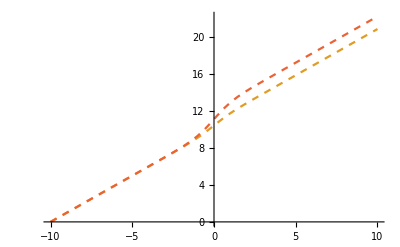

```mathematica
Plot[Evaluate[{
primitiveEigRtAnalyt[1][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t],
primitiveEigRtNum[1][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t],
primitiveEigRtAnalyt[2][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t],
primitiveEigRtNum[2][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]
}/.{ω1->1,α1->1,τ1->1,ω2->1,α2->1,τ2->1,αc->1,τc->1}
],relevantdomain,PlotStyle->stylecompare]
```

### Integrals in the higher order parallel (∥) recurrence relation (HOvaP)

#### Semi-analytical parallel (∥) / normal (⊥) decomposition

```mathematica
Definition[va]
```

va[n_,k_][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]=vaN[n,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]+vaP[n,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]

```mathematica
vaNum[n_,k_][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]:=vaNNum[n,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]+vaPNum[n,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]
```

#### Problematic integrands

```mathematica
IntegrandinHOvaPAnalyt[n_,k_][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t1_]:=mUinv[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1].(-1/2(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1])^(-1/2)mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1].va[n-1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]''[t1]+1/4(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1])^(-3/2)p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]'[t1]mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1].va[n-1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t1]+1/2(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1])^(1/2)((p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]''[t1])/(4p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1]^2)-(5p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]'[t1]^2)/(16p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1]^3))mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1].va[n-1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t1]-mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1].vaN[n,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t1])
```

```mathematica
IntegrandinHOvaPNum[n_,k_][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t1_]:=mUinv[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1].(-1/2(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1])^(-1/2)mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1].vaNum[n-1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]''[t1]+1/4(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1])^(-3/2)p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]'[t1]mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1].vaNum[n-1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t1]+1/2(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1])^(1/2)((p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]''[t1])/(4p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1]^2)-(5p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]'[t1]^2)/(16p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1]^3))mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1].vaNum[n-1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t1]-mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1].vaNNum[n,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t1])
```

#### Semi-analytical higher order normal (⊥) recurrence relation (ζ-dependent)

```mathematica
Definition[HOvaN]
```

HOvaN[n_,k_][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]:=Simplify[(2 √(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]) (II.mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]).va[n-1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t]-(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]'[t] (II.mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]).va[n-2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t])/(2 p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])+(II.mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]).va[n-2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]''[t]-p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t] ((p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]''[t])/(4 (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^2)-(5 (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]'[t])^2)/(16 (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^3)) (II.mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]).va[n-2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t])/(∑_(kp=1)^nk (p[kp][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]-p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]))]

I only define this normal one for the relevant Test’s i.c.’s:

```mathematica
NHOvaN[n_,k_][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]:=(2 √(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]) (II.mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]).vaNum[n-1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t]-1/(2 p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]'[t] (II.mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]).vaNum[n-2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t]+(II.mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]).vaNum[n-2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]''[t]-p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t] ((p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]''[t])/(4 (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^2)-(5 (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]'[t])^2)/(16 (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t])^3)) (II.mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]).vaNum[n-2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t])/(∑_(kp=1)^nk (p[kp][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]-p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]))(*//Simplify*)
```

#### Semi-analytical higher order parallel (∥) recurrence relation (ζ-dependent)

Recall of HOvaP:

```mathematica
Definition[HOvaP]
```

HOvaP[n_,k_][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]:=Simplify[mU[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t].∑_(l=1)^nl[k] Subscript[ζ,n,k,(+l j)/ⅈ] e[k,l][ω1,α1,τ1,ω2,α2,τ2,αc,τc][ti]+mU[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t].∫_ti^t mUinv[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1].(-1/2 1/(√(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1])) mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1].va[n-1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]''[t1]+1/4 (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1])^(-3/2) p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]'[t1] mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1].va[n-1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t1]+1/2 √(p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1]) ((p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]''[t1])/(4 (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1])^2)-(5 (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc]'[t1])^2)/(16 (p[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1])^3)) mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1].va[n-1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t1]-mP[k][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t1].vaN[n,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[t1])ⅆt1]

Semi-analytical version of HOvaP for Test’s i.c.’s:

```mathematica
NHOvaP[n_,k_][ω1b_,α1b_,τ1b_,A1b_,ω2b_,α2b_,τ2b_,A2b_,αcb_,τcb_,S_][t_]:=mU[ω1b,α1b,τ1b,ω2b,α2b,τ2b,αcb,τcb][t].∑_(l=1)^nl[k] Subscript[ζ, n,k,+l j/ⅈ] e[k,l][ω1b,α1b,τ1b,ω2b,α2b,τ2b,αcb,τcb][ti]+mU[ω1b,α1b,τ1b,ω2b,α2b,τ2b,αcb,τcb][t].Array[ParametricNPrimitiveValue[{(IntegrandinHOvaPNum[n,k][ω1b,α1b,τ1b,A1b,ω2b,α2b,τ2b,A2b,αcb,τcb,S][t])[[#]],ti},
intN,{t,tmin,tmax},{ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T,constsjList}//Flatten][ω1b,α1b,τ1b,A1b,ω2b,α2b,τ2b,A2b,αcb,τcb,S,Subscript[ζ, 0,1,-ⅈ j],Subscript[ζ, 0,2,-ⅈ j],Subscript[ζ, 1,1,-ⅈ j],Subscript[ζ, 1,2,-ⅈ j],Subscript[ζ, 2,1,-ⅈ j],Subscript[ζ, 2,2,-ⅈ j]][t]&,dim]
```

ζ_(0,1,1),ζ_(0,1,-1),ζ_(0,2,1),ζ_(0,2,-1),ζ_(1,1,1),ζ_(1,1,-1),ζ_(1,2,1),ζ_(1,2,-1),ζ_(2,1,1),ζ_(2,1,-1),ζ_(2,2,1),ζ_(2,2,-1)

-ⅈ j

#### Semi-analytical zeroth (0th) order coefficients

Zeroth order normal (⊥) coefficients: the analytical  ^k a_0^⊥ (which are zero)

```mathematica
For[k=1,k<=nk,k++,{
vaNNum[0,k][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]=vaN[0,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]
}]
ClearAll[k]
```

Zeroth order parallel (∥) coefficients: the analytical  ^k a_0^∥

```mathematica
For[k=1,k<=nk,k++,{
vaPNum[0,k][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]=vaP[0,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]
}]
ClearAll[k]
```

#### Semi-analytical first (1st) order coefficients

First order normal (⊥) coefficients: the analytical  ^k a_1^⊥ (which involve  ^k a_0^∥ ~ ^k e, analytical)

```mathematica
For[k=1,k<=nk,k++,{
vaNNum[1,k][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]=vaN[1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]
}]
ClearAll[k]
```

First order parallel (∥) coefficients:  ^k a_1^∥

```mathematica
For[k=1,k<=nk,k++,{
vaPNum[1,k][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]=NHOvaP[1,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]
}]
ClearAll[k]
```

#### Semi-analytical second (2nd) order coefficients (~ 15 sec.)

Second order normal (⊥) coefficients:  ^k a_2^∥

```mathematica
For[k=1,k<=nk,k++,{
vaNNum[2,k][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]=NHOvaN[2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]
}]
ClearAll[k]
```

Second order parallel (∥) coefficients:  ^k a_2^∥

```mathematica
For[k=1,k<=nk,k++,{
vaPNum[2,k][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]=NHOvaP[2,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]
}]
ClearAll[k]
```

### Semi-analytical solutions (~ 30 sec.)

#### Functions

Semi-analytical vector adiabatic ansatz function:

```mathematica
VecAdbAnsatzNum[o_,k_][ω1b_,α1b_,τ1b_,A1b_,ω2b_,α2b_,τ2b_,A2b_,αcb_,τcb_,S_][s_]:=(p[k][ω1b,α1b,τ1b,ω2b,α2b,τ2b,αcb,τcb][s])^(-1/4) Exp[j S primitiveEigRtNum[k][ω1b,α1b,τ1b,ω2b,α2b,τ2b,αcb,τcb][s]] ∑_(n=0)^o (j S)^-n vaNum[n,k][ω1b,α1b,τ1b,A1b,ω2b,α2b,τ2b,A2b,αcb,τcb,S][s]
```

Semi-analytical vector adiabatic general expansion function:

```mathematica
VecAdbGralExpNum[o_][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]:=(∑_(k=1)^nk VecAdbAnsatzNum[o,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.j->+ⅈ)+(∑_(k=1)^nk VecAdbAnsatzNum[o,k][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.j->-ⅈ)
```

#### 0th and 1st-orders solutions

Semi-analytical adiabatic solution:

```mathematica
For[n=0,n<=1,n++,
vxAdbNum[n][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]=VecAdbGralExpNum[n][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]
]
ClearAll[n]
```

#### 2nd-order solution (~ 30 sec.)

```mathematica
n=2;
vxAdbNum[n][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][t_]=VecAdbGralExpNum[n][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]
ClearAll[n]
```

## Specification of the expansion constants

### Plus/minus solutions

#### “Plus” solution (i.e. j->+ⅈ)

To focus only on the ‘+’ solution:

```mathematica
constsPlus={Subscript[ζ, _,_,-1]->0,Subscript[ζ, _,_,-2]->0};
```

#### “Minus” solution (i.e. j->-ⅈ)

To focus only on the ‘−’ solution:

```mathematica
constsMinus={Subscript[ζ, _,_,+1]->0,Subscript[ζ, _,_,+2]->0};
```

### Higher orders: initially switched off

```mathematica
constsHOsOff={};
For[n=1,n<=adbOrdNum,n++,
For[k=1,k<=nk,k++,
For[l=1,l<=nl[k],l++,{
AppendTo[constsHOsOff,Subscript[ζ, n,k,l]->0],
AppendTo[constsHOsOff,Subscript[ζ, n,k,-l]->0]
}]]]
ClearAll[n,k,l]
constsHOsOff
```

{ζ_(1,1,1)→0,ζ_(1,1,-1)→0,ζ_(1,2,1)→0,ζ_(1,2,-1)→0,ζ_(2,1,1)→0,ζ_(2,1,-1)→0,ζ_(2,2,1)→0,ζ_(2,2,-1)→0}

### Single-eigenspace excitations (ATTEMPT OF in- and anti-phase i.c.’s)

```mathematica
For[k=1,k<=nk,k++,
constsEig[k]={};
For[ñ=1,ñ<=nk,ñ++,
If[ñ!=k,AppendTo[constsEig[k],Subscript[ζ, _,ñ,_]->0]]];
Print["constsEig[",k,"]=",constsEig[k]]
]
```

constsEig[1]={ζ_(_,2,_)→0}

constsEig[2]={ζ_(_,1,_)→0}

```mathematica
constsInPhase=constsEig[1]
constsAntiPhase=constsEig[2]
```

{ζ_(_,2,_)→0}

{ζ_(_,1,_)→0}

### Constants for generic initial amplitudes at 0th order

#### Constants for generic initial amplitudes (numerical)

```mathematica
constsNum[ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_]=NSolve[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][ti][[1]]==A1,
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][ti][[2]]==A2,
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[ti][[1]]==-ⅈ A1 T ω1,
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[ti][[2]]==-ⅈ A2 T ω2
},constsListUpto[0]]//Flatten;
```

```mathematica
(*constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]*)
```

#### Constants for generic initial amplitudes (analytic attempt)

```mathematica
(*AbsoluteTiming[Solve[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][ti][[1]]==A1,
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][ti][[2]]==A2,
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[ti][[1]]==-ⅈ A1 T ω1,
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]'[ti][[2]]==-ⅈ A2 T ω2
}/.constsMinus,constsListUpto[0]]//Flatten]
constsAdb[ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_]=%[[2]];*)
```

I don’t think it’s going to compute (though I have only left it ~ 15 min.)

#### Increase numerical precision?

Obs: I think that the lack of analytical expressions for these constants leads to terrible results for the in-phase initial conditions in the sudden and high-frequency regimes, which is quite inconvenient.

Possible solution: I could try to increase the numerical precision and see if that suffices for the range of parameters I would use.

#### Corresponding constants for my test parameters (test constants)

These are the constants for the chosen test parameters  paramTest  and the higher-order corrections initially switched off through  constsHOsOff.

- Numerical values  for generic initial conditions (automatized through the computed, generic constsNum):

```mathematica
constsTest={constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],constsHOsOff}/.paramTest//Flatten;
```

- Obs: Analytical values for the ‘first single-oscillator initially excited initial condition’ icOsc1:

```mathematica
(*constsTest={
Subscript[ζ, 0,1,1]->0,Subscript[ζ, 0,1,-1]->1/(√2),Subscript[ζ, 0,2,1]->0,Subscript[ζ, 0,2,-1]->0,
Subscript[ζ, 1,1,1]->0,Subscript[ζ, 1,1,-1]->0,Subscript[ζ, 1,2,1]->0,Subscript[ζ, 1,2,-1]->1,
Subscript[ζ, 2,1,1]->0,Subscript[ζ, 2,1,-1]->1,Subscript[ζ, 2,2,1]->0,Subscript[ζ, 2,2,-1]->1
};*)
```

## Exact solution (fully numerical)

```mathematica
icSolSingleOsc[1]
```

{A1,0}

```mathematica
icDerivSingleOsc[1]
```

{-ⅈ A1 T ω1,0}

### Recall the EOM

```mathematica
Print[Eom[mM[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t],vx[t]]//MatrixForm]
```

(T^2 ((ω1^2+α1^2 Sech[t/τ1]^2+αc^2 Sech[t/τc]^2) x[1][t]-αc^2 Sech[t/τc]^2 x[2][t])+x[1]''[t]
T^2 (-αc^2 Sech[t/τc]^2 x[1][t]+(ω2^2+α2^2 Sech[t/τ2]^2+αc^2 Sech[t/τc]^2) x[2][t])+x[2]''[t])

### Single-oscillator initially excited solutions

#### Oscillator 1 solution

```mathematica
Eom[mM[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t],vx[t]][[1]]==icDerivSingleOsc[1][[1]]
```

T^2 ((ω1^2+α1^2 Sech[t/τ1]^2+αc^2 Sech[t/τc]^2) x[1][t]-αc^2 Sech[t/τc]^2 x[2][t])+x[1]''[t]==-ⅈ A1 T ω1

```mathematica
solNumSingleOsc[1]=ParametricNDSolve[{
Eom[mM[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t],vx[t]][[1]]==0,
Eom[mM[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t],vx[t]][[2]]==0,
x[1][ti]==icSolSingleOsc[1][[1]],x[1]'[ti]==icDerivSingleOsc[1][[1]],
x[2][ti]==icSolSingleOsc[1][[2]],x[2]'[ti]==icDerivSingleOsc[1][[2]]},
{x[1],x[2]},{t,tmin,tmax},{ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T}]
```

{x[1]→ParametricFunction[<>],x[2]→ParametricFunction[<>]}

```mathematica
vxNumSingleOsc[1][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][s_]=Evaluate[{x[1][t],x[2][t]}/.solNumSingleOsc[1]]/.t->s;
vxNumSingleOsc[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]
```

{ParametricFunction[<>][t],ParametricFunction[<>][t]}

#### Oscillator 2 solution

```mathematica
solNumSingleOsc[2]=ParametricNDSolve[{
Eom[mM[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t],vx[t]][[1]]==0,
Eom[mM[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t],vx[t]][[2]]==0,
x[1][ti]==icSolSingleOsc[2][[1]],x[1]'[ti]==icDerivSingleOsc[2][[1]],
x[2][ti]==icSolSingleOsc[2][[2]],x[2]'[ti]==icDerivSingleOsc[2][[2]]},
{x[1],x[2]},{t,tmin,tmax},{ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T}]
```

{x[1]→ParametricFunction[<>],x[2]→ParametricFunction[<>]}

```mathematica
vxNumSingleOsc[2][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][s_]=Evaluate[{x[1][t],x[2][t]}/.solNumSingleOsc[2]]/.t->s;
vxNumSingleOsc[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]
```

{ParametricFunction[<>][t],ParametricFunction[<>][t]}

### General solution (with manipulable initial amplitudes)

```mathematica
solNumGral=ParametricNDSolve[{
Eom[mM[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t],vx[t]][[1]]==0,
Eom[mM[ω1,α1,τ1,ω2,α2,τ2,αc,τc][t],vx[t]][[2]]==0,
x[1][ti]==icSolSingleOsc[1][[1]],x[1]'[ti]==icDerivSingleOsc[1][[1]],
x[2][ti]==icSolSingleOsc[2][[2]],x[2]'[ti]==icDerivSingleOsc[2][[2]]},
{x[1],x[2]},{t,tmin,tmax},{ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T}]
```

{x[1]→ParametricFunction[<>],x[2]→ParametricFunction[<>]}

```mathematica
vxNumGral[ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_][s_]=Evaluate[{x[1][t],x[2][t]}/.solNumGral]/.t->s;
vxNumGral[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]
```

{ParametricFunction[<>][t],ParametricFunction[<>][t]}

## Plots of results

## Exact solution plots (fully numerical)

### Static plots

#### Oscillator 1 initially excited (at x_(1, i)=1 /√(2 ω_1), for {ω_1 → 1/2, α_1 → 1, τ_1 → 1, ω_2 → 1, α_2 → 1, τ_2 → 1, α_c → 1, τ_c → 1, T → 3})

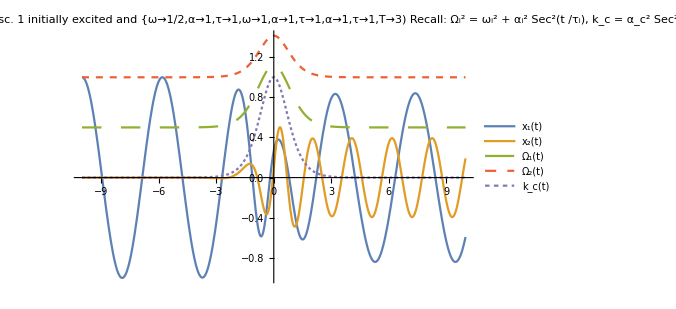

```mathematica
Plot[
Evaluate[{
Re[vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]]/.solNumSingleOsc[1],
Ω[1][ω1,α1,τ1][t],
Ω[2][ω2,α2,τ2][t],
kc[αc,τc][t]
}/.paramTest/.icOsc1
],relevantdomain,
PlotRange->All,
PlotStyle->{SolidData,SolidData,Dashing[Large],Dashed,Dashing[Tiny]},
PlotLegends->{"x_1(t)","x_2(t)","Ω_1(t)","Ω_2(t)","k_c(t)"},
PlotLabel->"Numerical solution (for only Osc. 1 initially excited and
{ω→1/2,α→1,τ→1,ω→1,α→1,τ→1,α→1,τ→1,T→3)
Recall:  Ω_i^2 = ω_i^2 + α_i^2 Sec^2(t /τ_i),  k_c = α_c^2 Sec^2(t /τ_c)",
ImageSize->500]
```

#### Oscillator 2 initially excited (at x_(2, i)=1 /√(2 ω_2), for {ω_1 → 1/2, α_1 → 1, τ_1 → 1, ω_2 → 1, α_2 → 1, τ_2 → 1, α_c → 1, τ_c → 1, T → 3})

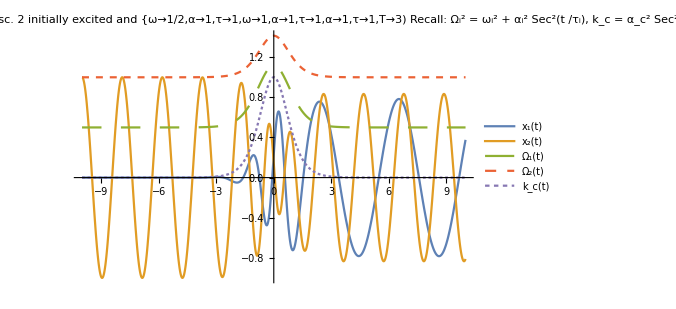

```mathematica
Plot[
Evaluate[{
Re[vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]]/.solNumSingleOsc[2],
Ω[1][ω1,α1,τ1][t],
Ω[2][ω2,α2,τ2][t],
kc[αc,τc][t]
}/.paramTest/.icOsc2
],relevantdomain,
PlotRange->All,
PlotStyle->{SolidData,SolidData,Dashing[Large],Dashed,Dashing[Tiny]},
PlotLegends->{"x_1(t)","x_2(t)","Ω_1(t)","Ω_2(t)","k_c(t)"},
PlotLabel->"Numerical solution (for only Osc. 2 initially excited and
{ω→1/2,α→1,τ→1,ω→1,α→1,τ→1,α→1,τ→1,T→3)
Recall:  Ω_i^2 = ω_i^2 + α_i^2 Sec^2(t /τ_i),  k_c = α_c^2 Sec^2(t /τ_c)",
ImageSize->500]
```

#### General solution (for x_(1, i)=A_1/√(2 ω_1) and {ω_1 → 1/2, α_1 → 1, τ_1 → 1, ω_2 → 1, α_2 → 1, τ_2 → 1, α_c → 1, τ_c → 1, T → 3})

```mathematica
Plot[
Evaluate[{
Re[vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]]/.solNumGral,
Ω[1][ω1,α1,τ1][t],
Ω[2][ω2,α2,τ2][t],
kc[αc,τc][t]
}/.paramTest/.icOsc1
],relevantdomain,
PlotRange->All,
PlotStyle->{SolidData,SolidData,Dashing[Large],Dashed,Dashing[Tiny]},
PlotLegends->{"x_1(t)","x_2(t)","Ω_1(t)","Ω_2(t)","k_c(t)"},
PlotLabel->"Numerical solution (for only Osc. 1 initially excited and
{ω→1/2,α→1,τ→1,ω→1,α→1,τ→1,α→1,τ→1,T→3)
Recall:  Ω_i^2 = ω_i^2 + α_i^2 Sec^2(t /τ_i),  k_c = α_c^2 Sec^2(t /τ_c)",
ImageSize->500]
```

-Graphics-

### Manipulable plots

#### Oscillator 1 initially excited (at x_(1, i)=1 /√(2 ω_1))

```mathematica
Manipulate[
Plot[
Evaluate[{
Re[vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]]/.solNumSingleOsc[1],
Ω[1][ω1,α1,τ1][t],
Ω[2][ω2,α2,τ2][t],
kc[αc,τc][t]
}
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->All,
PlotStyle->{SolidData,SolidData,Dashing[Large],Dashed,Dashing[Tiny]},
PlotLegends->{"x_1(t)","x_2(t)","Ω_1(t)","Ω_2(t)","k_c(t)"},
PlotLabel->"Numerical solution (for only Osc. 1 initially excited)
Recall:  Ω_i^2 = ω_i^2 + α_i^2 Sec^2(t /τ_i),  k_c = α_c^2 Sec^2(t /τ_c)",
ImageSize->500],
Style["Parameters",12],
{{ω1,1/2,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,1,"τ_1"},0.1,5},
{{ω2,1,"ω_2"},0.1,5},{{α2,1,"α_2"},0.1,5},{{τ2,1,"τ_2"},0.1,5},
{{αc,1,"α_c"},0.1,5},{{τc,1,"τ_c"},0.1,5},Style["
Initial conditions",12],{{A1,1,"A_1"},-10,10},{{A2,0,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,3,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

#### Oscillator 2 initially excited (at x_(2, i)=1 /√(2 ω_2))

```mathematica
Manipulate[
Plot[
Evaluate[{
Re[vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]]/.solNumSingleOsc[2],
Ω[1][ω1,α1,τ1][t],
Ω[2][ω2,α2,τ2][t],
kc[αc,τc][t]
}
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotStyle->{SolidData,SolidData,Dashing[Large],Dashing[Tiny],Dashed},
PlotRange->All,
PlotLegends->{"x_1(t)","x_2(t)","Ω_1(t)","Ω_2(t)","k_c(t)"},
PlotLabel->"Numerical solution (for only Osc. 1 initially excited)
Recall:  Ω_i^2 = ω_i^2 + α_i^2 Sec^2(t /τ_i),  k_c = α_c^2 Sec^2(t /τ_c)",
ImageSize->500],
Style["Parameters",12],
{{ω1,1/2,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,1,"τ_1"},0.1,5},
{{ω2,1,"ω_2"},0.1,5},{{α2,1,"α_2"},0.1,5},{{τ2,1,"τ_2"},0.1,5},
{{αc,1,"α_c"},0.1,5},{{τc,1,"τ_c"},0.1,5},Style["
Initial conditions",12],{{A1,0,"A_1"},-10,10},{{A2,1,"A_2"},-10,10},
Style["
Adiabatic regime",12],{{T,3,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

#### General solution

```mathematica
Manipulate[
Plot[
Evaluate[{
Re[vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]]/.solNumGral,
Ω[1][ω1,α1,τ1][t],
Ω[2][ω2,α2,τ2][t],
kc[αc,τc][t]
}
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->All,
PlotStyle->{SolidData,SolidData,Dashing[Large],Dashed,Dashing[Tiny]},
PlotLegends->{"x_1(t)","x_2(t)","Ω_1(t)","Ω_2(t)","k_c(t)"},
PlotLabel->"Numerical solution (for arbitrary initial amplitudes)
Recall:  Ω_i^2 = ω_i^2 + α_i^2 Sec^2(t /τ_i),  k_c = α_c^2 Sec^2(t /τ_c)",
ImageSize->500],
Style["Parameters",12],
{{ω1,1/2,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,1,"τ_1"},0.1,5},
{{ω2,1,"ω_2"},0.1,5},{{α2,1,"α_2"},0.1,5},{{τ2,1,"τ_2"},0.1,5},
{{αc,1,"α_c"},0.1,5},{{τc,1,"τ_c"},0.1,5},Style["
Initial conditions",12],{{A1,1,"A_1"},-10,10},{{A2,1,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,3,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

## Adiabatic solution plots (semi-analytic)

### 0th order semi-analytical adiabatic solution

#### Static plot - Test constants

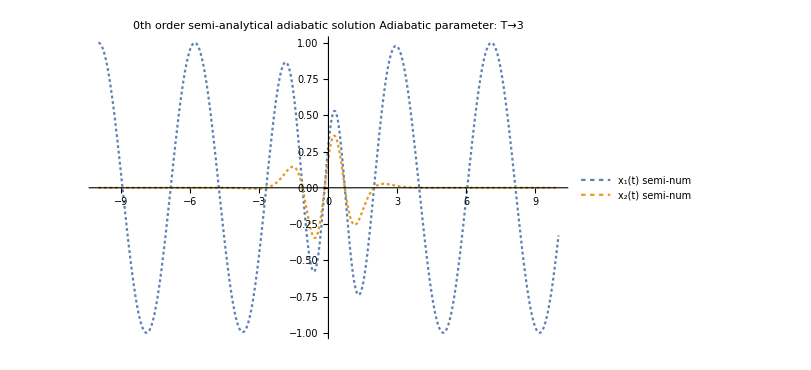

```mathematica
Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.paramTest/.icOsc1
],relevantdomain,
PlotRange->All,
PlotStyle->style0th,
PlotLegends->{"x_1(t) semi-num","x_2(t) semi-num"(*,"x_3(t) semi-num"*)},
PlotLabel->"0th order semi-analytical adiabatic solution
Adiabatic parameter: T"->3,
ImageSize->600]
```

#### Manipulable plot

```mathematica
Manipulate[Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]
}/.constsMinus/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.icOsc1
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->All,
PlotStyle->style0th,
PlotLegends->{"x_1(t) semi-num","x_2(t) semi-num"(*,"x_3(t) semi-num"*)},
PlotLabel->"0th order semi-analytical adiabatic solution
Adiabatic parameter: T"->3,
ImageSize->600],
Style["Parameters",12],
{{ω1,1/2,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,1,"τ_1"},0.1,5},{{ω2,1,"ω_2"},0.1,5},{{α2,1,"α_2"},0.1,5},{{τ2,1,"τ_2"},0.1,5},{{αc,1,"α_c"},0.1,5},{{τc,1,"τ_c"},0.1,5},Style["
Adiabatic regime",12],{{T,3,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

### 1st order adiabatic solution vs. semi-analytical

#### Static plot - Test constants

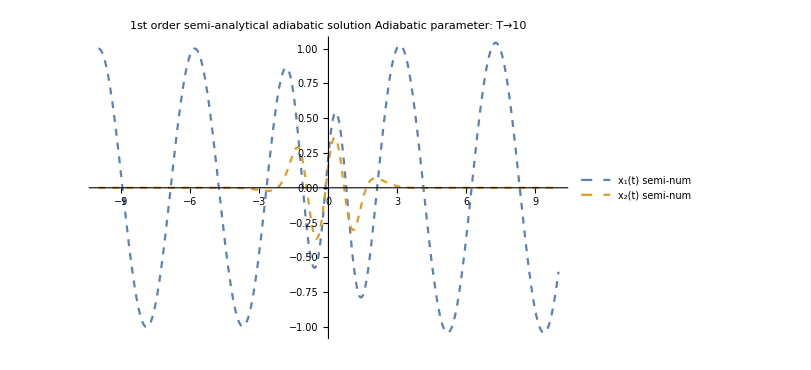

```mathematica
Plot[
Evaluate@Re[{
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff/.paramTest/.icOsc1
],relevantdomain,
PlotRange->All,
PlotStyle->style1st,
PlotLegends->{"x_1(t) semi-num","x_2(t) semi-num"(*,"x_3(t) semi-num"*)},
PlotLabel->"1st order semi-analytical adiabatic solution
Adiabatic parameter: T"->10,
ImageSize->600]
```

#### Manipulable plot

```mathematica
Manipulate[Plot[
Evaluate@Re[{
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff/.T->10
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->All,
PlotStyle->style1st,
PlotLegends->{"x_1(t) semi-num","x_2(t) semi-num"(*,"x_3(t) semi-num"*)},
PlotLabel->"1st order semi-analytical adiabatic solution
Adiabatic parameter: T"->3,
ImageSize->600],
Style["Parameters",12],
{{ω1,1/2,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,1,"τ_1"},0.1,5},
{{ω2,1,"ω_2"},0.1,5},{{α2,1,"α_2"},0.1,5},{{τ2,1,"τ_2"},0.1,5},
{{αc,1,"α_c"},0.1,5},{{τc,1,"τ_c"},0.1,5},Style["
Initial conditions",12],{{A1,1,"A_1"},-10,10},{{A2,0,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,3,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

### 2nd order adiabatic solution vs. semi-analytical

#### Static plot

Takes quite long so I disabled it. It printed:

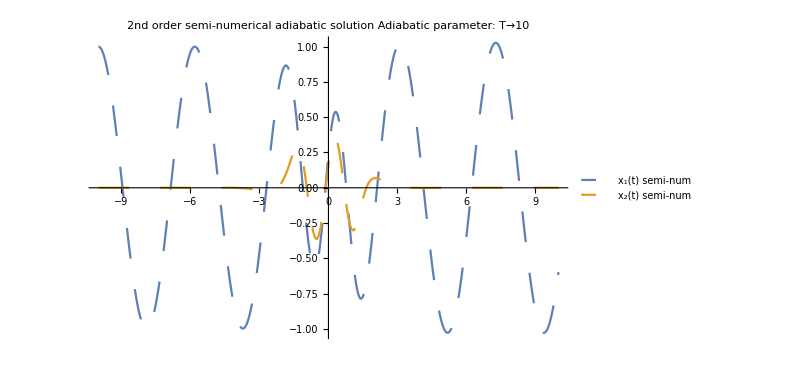

```mathematica
(*Plot[
Evaluate@Re[{
vxAdbNum[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff/.paramTest/.icOsc1
],relevantdomain,
PlotRange->All,
PlotStyle->style2nd,
PlotLegends->{"x_1(t) semi-num","x_2(t) semi-num"(*,"x_3(t) semi-num"*)},
PlotLabel->"2nd order semi-analytical adiabatic solution
Adiabatic parameter: T"->3,
ImageSize->600]*)
```

#### Manipulable plot

```mathematica
(*Manipulate[Plot[
Evaluate@Re[{
vxAdbNum[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff/.T->10
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->All,
PlotStyle->style2nd,
PlotLegends->{"x_1(t) semi-num","x_2(t) semi-num"(*,"x_3(t) semi-num"*)},
PlotLabel->"2nd order semi-analytical adiabatic solution
Adiabatic parameter: T"->3,
ImageSize->600],
Style["Parameters",12],
{{ω1,1/2,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,1,"τ_1"},0.1,5},
{{ω2,1,"ω_2"},0.1,5},{{α2,1,"α_2"},0.1,5},{{τ2,1,"τ_2"},0.1,5},
{{αc,1,"α_c"},0.1,5},{{τc,1,"τ_c"},0.1,5},Style["
Initial conditions",12],{{A1,1,"A_1"},-10,10},{{A2,0,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,3,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]*)
```

### Altogether (0th, 1st and 2nd order, semi-analytical adiabatic solutions)

#### Static plot

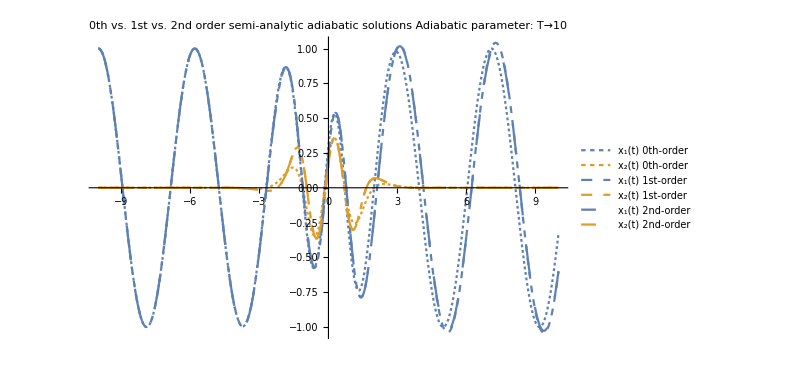

```mathematica
(*Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff/.paramTest/.icOsc1
],relevantdomain,
PlotRange->All,
PlotStyle->Flatten[{style0th,style1st,style2nd},1],
PlotLegends->{
"x_1(t) 0th-order","x_2(t) 0th-order"(*,"x_3(t) 0th-order"*),
"x_1(t) 1st-order","x_2(t) 1st-order"(*,"x_3(t) 1st-order"*),
"x_1(t) 2nd-order","x_2(t) 2nd-order"(*,"x_3(t) 2nd-order"*),
"x_1(t) num","x_2(t) semi-num"(*,"x_3(t) semi-num"*)},
PlotLabel->"0th vs. 1st vs. 2nd order semi-analytic adiabatic solutions
Adiabatic parameter: T"->3,
ImageSize->600]*)
```

#### Manipulable plot

```mathematica
(*Manipulate[Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff/.T->10
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->All,
PlotStyle->Flatten[{style0th,style1st,style2nd},1],
PlotLegends->{
"x_1(t) adb","x_2(t) adb"(*,"x_3(t) adb"*),
"x_1(t) semi-num","x_2(t) semi-num"(*,"x_3(t) semi-num"*)},
PlotLabel->"0th order adiabatic vs. semi-analytical solution
Adiabatic parameter: T"->3,
ImageSize->600],
Style["Parameters",12],
{{ω1,1/2,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,1,"τ_1"},0.1,5},
{{ω2,1,"ω_2"},0.1,5},{{α2,1,"α_2"},0.1,5},{{τ2,1,"τ_2"},0.1,5},
{{αc,1,"α_c"},0.1,5},{{τc,1,"τ_c"},0.1,5},Style["
Initial conditions",12],{{A1,1,"A_1"},-10,10},{{A2,0,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,3,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]*)
```

### Manipulating the constants of the adiabatic expansion

#### Constructing manipulative constants

```mathematica
ClearAll[constsManip,constsTestManip]
```

```mathematica
(*constsManip[0][c01p_,c01m_,c02p_,c02m_]={
Subscript[ζ, 0,1,1]->c01p,Subscript[ζ, 0,1,-1]->c01m,Subscript[ζ, 0,2,1]->c02p,Subscript[ζ, 0,2,-1]->c02m};*)
```

```mathematica
(*constsManip[1][c01p_,c01m_,c02p_,c02m_,c11p_,c11m_,c12p_,c12m_]={
Subscript[ζ, 0,1,1]->c01p,Subscript[ζ, 0,1,-1]->c01m,Subscript[ζ, 0,2,1]->c02p,Subscript[ζ, 0,2,-1]->c02m,
Subscript[ζ, 1,1,1]->c11p,Subscript[ζ, 1,1,-1]->c11m,Subscript[ζ, 1,2,1]->c12p,Subscript[ζ, 1,2,-1]->c12m};*)
```

```mathematica
(*constsManip[2][c01p_,c01m_,c02p_,c02m_,c11p_,c11m_,c12p_,c12m_,c21p_,c21m_,c22p_,c22m_]={
Subscript[ζ, 0,1,1]->c01p,Subscript[ζ, 0,1,-1]->c01m,Subscript[ζ, 0,2,1]->c02p,Subscript[ζ, 0,2,-1]->c02m,
Subscript[ζ, 1,1,1]->c11p,Subscript[ζ, 1,1,-1]->c11m,Subscript[ζ, 1,2,1]->c12p,Subscript[ζ, 1,2,-1]->c12m,
Subscript[ζ, 2,1,1]->c21p,Subscript[ζ, 2,1,-1]->c21m,Subscript[ζ, 2,2,1]->c22p,Subscript[ζ, 2,2,-1]->c22m};*)
```

```mathematica
constsManip[c01p_,c01m_,c02p_,c02m_,c11p_,c11m_,c12p_,c12m_,c21p_,c21m_,c22p_,c22m_]={
Subscript[ζ, 0,1,1]->c01p,Subscript[ζ, 0,1,-1]->c01m,Subscript[ζ, 0,2,1]->c02p,Subscript[ζ, 0,2,-1]->c02m,
Subscript[ζ, 1,1,1]->c11p,Subscript[ζ, 1,1,-1]->c11m,Subscript[ζ, 1,2,1]->c12p,Subscript[ζ, 1,2,-1]->c12m,
Subscript[ζ, 2,1,1]->c21p,Subscript[ζ, 2,1,-1]->c21m,Subscript[ζ, 2,2,1]->c22p,Subscript[ζ, 2,2,-1]->c22m};
```

```mathematica
constsManip[c01p,c01m,c02p,c02m,c11p,c11m,c12p,c12m,c21p,c21m,c22p,c22m]
```

{ζ_(0,1,1)→c01p,ζ_(0,1,-1)→c01m,ζ_(0,2,1)→c02p,ζ_(0,2,-1)→c02m,ζ_(1,1,1)→c11p,ζ_(1,1,-1)→c11m,ζ_(1,2,1)→c12p,ζ_(1,2,-1)→c12m,ζ_(2,1,1)→c21p,ζ_(2,1,-1)→c21m,ζ_(2,2,1)→c22p,ζ_(2,2,-1)→c22m}

Old Test constants:

{ζ_(0,1,1)→0,ζ_(0,1,-1)→1/(√2),ζ_(0,2,1)→0,ζ_(0,2,-1)→0,ζ_(1,1,1)→0,ζ_(1,1,-1)→0,ζ_(1,2,1)→0,ζ_(1,2,-1)→1,ζ_(2,1,1)→0,ζ_(2,1,-1)→1,ζ_(2,2,1)→0,ζ_(2,2,-1)→1}

```mathematica
constsTestManip[c01p_,c01m_,c02p_,c02m_,c11p_,c11m_,c12p_,c12m_,c21p_,c21m_,c22p_,c22m_]={c01p->0,c01m->1/2,c02p->0,c02m->0,c11p->0,c11m->1/2,c12p->0,c12m->1,c21p->0,c21m->1/2,c22p->0,c22m->1};
```

```mathematica
constsTestManip[c01p,c01m,c02p,c02m,c11p,c11m,c12p,c12m,c21p,c21m,c22p,c22m]
```

{c01p→0,c01m→1/2,c02p→0,c02m→0,c11p→0,c11m→1/2,c12p→0,c12m→1,c21p→0,c21m→1/2,c22p→0,c22m→1}

```mathematica
ClearAll[vxAdbNumManip]
```

```mathematica
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]
```

```mathematica
vxAdbNumManip[1][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_,c01p_,c01m_,c02p_,c02m_,c11p_,c11m_,c12p_,c12m_,c21p_,c21m_,c22p_,c22m_][t_]=vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.constsManip[c01p,c01m,c02p,c02m,c11p,c11m,c12p,c12m,c21p,c21m,c22p,c22m];
```

```mathematica
vxAdbNumManip[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T,c01p,c01m,c02p,c02m,c11p,c11m,c12p,c12m,c21p,c21m,c22p,c22m][t]
```

```mathematica
vxAdbNumManip[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T,c01p,c01m,c02p,c02m,c11p,c11m,c12p,c12m,c21p,c21m,c22p,c22m][t]/.constsTestManip[c01p,c01m,c02p,c02m,c11p,c11m,c12p,c12m,c21p,c21m,c22p,c22m]/.paramTest/.icOsc1/.t->0
```

{-0.0667966+4.38849 ⅈ,0.245222+3.06586 ⅈ}

```mathematica
vxAdbNumManip[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T,c01p,c01m,c02p,c02m,c11p,c11m,c12p,c12m,c21p,c21m,c22p,c22m][t][[1]]
```

#### Manipulable plot with free constants

```mathematica
Manipulate[Quiet@Plot[
Evaluate@Re[{
vxAdbNumManip[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T,c01p,c01m,c02p,c02m,c11p,c11m,c12p,c12m,0,0,0,0][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumSingleOsc[1]
}
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->All,
PlotStyle->Flatten[{style1st,stylenum},1],
PlotLegends->{"x_1(t) adb semi-num","x_2(t) adb semi-num"(*,"x_3(t) adb semi-num"*),
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"1st order semi-analytical adiabatic solution
Adiabatic parameter: T"->3,
ImageSize->600],
Style["Parameters",12],
{{ω1,1/2,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,1,"τ_1"},0.1,5},
{{ω2,1,"ω_2"},0.1,5},{{α2,1,"α_2"},0.1,5},{{τ2,1,"τ_2"},0.1,5},
{{αc,1,"α_c"},0.1,5},{{τc,1,"τ_c"},0.1,5},Style["
Initial conditions",12],{{A1,1,"A_1"},-10,10},{{A2,0,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,3,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01},Style["
Integration constants",12],{{c01p,0},-10,10},{{c01m,1},-10,10},{{c02p,0},-10,10},{{c02m,0},-10,10},{{c11p,0},-10,10},{{c11m,0},-10,10},{{c12p,0},-10,10},{{c12m,0},-10,10}
]
```

#### Manipulable plot with opposite values for the 1st-order 2nd-oscillator constants (they cancel any contribution)

```mathematica
Manipulate[Quiet@Plot[
Evaluate@Re[{
vxAdbNumManip[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T,c01p,c01m,c02p,c02m,c11p,c11m,c12p,-c12p(*c12m*),0,0,0,0][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumSingleOsc[1]
}
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->All,
PlotStyle->Flatten[{style1st,stylenum},1],
PlotLegends->{"x_1(t) adb semi-num","x_2(t) adb semi-num"(*,"x_3(t) adb semi-num"*),
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"1st order semi-analytical adiabatic solution
Adiabatic parameter: T"->3,
ImageSize->600],
Style["Parameters",12],
{{ω1,1/2,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,1,"τ_1"},0.1,5},
{{ω2,1,"ω_2"},0.1,5},{{α2,1,"α_2"},0.1,5},{{τ2,1,"τ_2"},0.1,5},
{{αc,1,"α_c"},0.1,5},{{τc,1,"τ_c"},0.1,5},Style["
Initial conditions",12],{{A1,1,"A_1"},-10,10},{{A2,0,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,3,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01},Style["
Integration constants",12],{{c01p,0},-10,10},{{c01m,1},-10,10},{{c02p,0},-10,10},{{c02m,0},-10,10},{{c11p,0},-10,10},{{c11m,0},-10,10},{{c12p,0},-10,10}(*,{{c12m,0},-10,10}*)
]
```

## Eigenvalues, eigenvectors and vector coefficients

Recall: Fulling’s vector adiabatic ansatz

^k x^(∓ (o))(t)=p_k(t)^(-1/4)e^(∓ ⅈ T (∫^t (p_k(t'))^(1/2)ⅆt' + ϕ_k)) ∑_(n=0)^o (∓ ⅈ T )^-n ^k a_n^∓(t)

	x^(o)(t)=∑_∓ ∑_k ^k x^(∓ (o))(t)

### Eigenvalues

#### Static plot

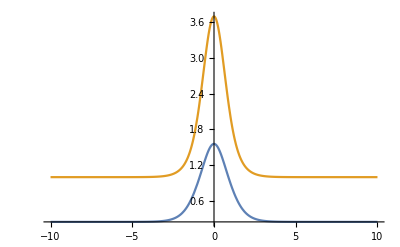

```mathematica
Plot[Evaluate[{
p[1][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t],
p[2][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]
}/.paramTest],
relevantdomain,PlotRange->All]
```

#### Manipulable plot

```mathematica
Manipulate[
Plot[Evaluate[{
p[1][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t],
p[2][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]}],
relevantdomain,PlotRange->All],
Style["Parameters",12],
{{ω1,0.71,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,0.5,"τ_1"},0.1,5},
{{ω2,0.8,"ω_2"},0.1,5},{{α2,2,"α_2"},0.1,5},{{τ2,1.41,"τ_2"},0.1,5},
{{αc,2.96,"α_c"},0.01,5},{{τc,1.17,"τ_c"},0.1,5}
]
```

### Eigenprojectors

#### Static plot

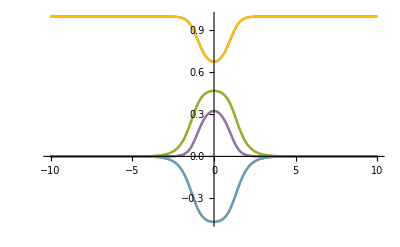

```mathematica
Plot[Evaluate[{
mP[1][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t],
mP[2][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]
}/.paramTest],
relevantdomain,PlotRange->All]
```

#### Manipulable plot

```mathematica
Manipulate[
Plot[Evaluate[{
mP[1][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t],
mP[2][ω1,α1,τ1,ω2,α2,τ2,αc,τc][t]}],
relevantdomain,PlotRange->All],
Style["Parameters",12],
{{ω1,0.71,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,0.5,"τ_1"},0.1,5},
{{ω2,0.8,"ω_2"},0.1,5},{{α2,2,"α_2"},0.1,5},{{τ2,1.41,"τ_2"},0.1,5},
{{αc,2.96,"α_c"},0.01,5},{{τc,1.17,"τ_c"},0.1,5}
]
```

### Vector coefficients

#### 0th order coefficients - Static plot

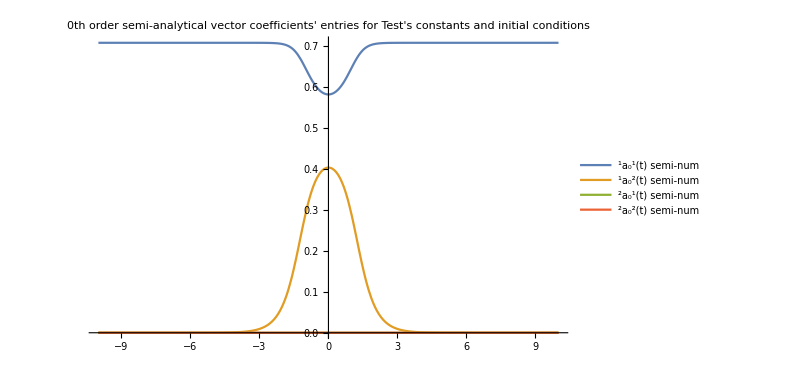

```mathematica
Plot[
Evaluate[Re[{
vaNum[0,1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vaNum[0,2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]
}/.j->-ⅈ/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.paramTest/.icOsc1
]],relevantdomain,
PlotRange->All,
PlotLegends->{"^1a_0^1(t) semi-num","^1a_0^2(t) semi-num","^2a_0^1(t) semi-num","^2a_0^2(t) semi-num"},
PlotLabel->"0th order semi-analytical vector coefficients' entries
for Test's constants and initial conditions",
ImageSize->600]
```

#### 1st order coefficients - Static plot

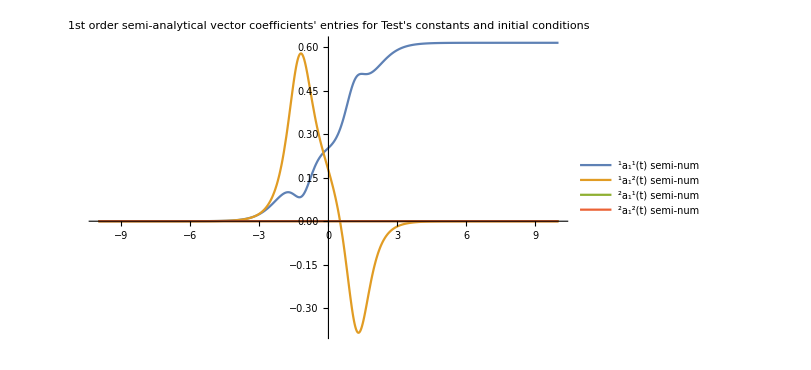

```mathematica
Plot[
Evaluate[Re[{
vaNum[1,1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vaNum[1,2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]
}/.j->-ⅈ/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff/.paramTest/.icOsc1
]],relevantdomain,
PlotRange->All,
PlotLegends->{"^1a_1^1(t) semi-num","^1a_1^2(t) semi-num","^2a_1^1(t) semi-num","^2a_1^2(t) semi-num"},
PlotLabel->"1st order semi-analytical vector coefficients' entries
for Test's constants and initial conditions",
ImageSize->600]
```

#### 0th order coefficients - Manipulable plot

```mathematica
Manipulate[
Plot[Evaluate[Re[{
vaNum[0,1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vaNum[0,2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]
}/.j->-ⅈ/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.T->1
]],relevantdomain,
PlotRange->All,
PlotLegends->{"^1a_0^1(t) semi-num","^1a_0^2(t) semi-num","^2a_0^1(t) semi-num","^2a_0^2(t) semi-num"},
PlotLabel->"0th order semi-analytical vector coefficients' entries
for Test's constants and initial conditions"],
Style["Parameters",12],
{{ω1,0.71,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,0.5,"τ_1"},0.1,5},
{{ω2,0.8,"ω_2"},0.1,5},{{α2,2,"α_2"},0.1,5},{{τ2,1.41,"τ_2"},0.1,5},
{{αc,2.96,"α_c"},0.01,5},{{τc,1.17,"τ_c"},0.1,5},Style["
Initial conditions",12],{{A1,1,"A_1"},-10,10},{{A2,0,"A_2"},-10,10}
]
```

#### 1st order coefficients - Manipulable plot

```mathematica
Manipulate[
Plot[Evaluate[Re[{
vaNum[1,1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vaNum[1,2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]
}/.j->-ⅈ/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff/.T->1
]],relevantdomain,
PlotRange->All,
PlotLegends->{"^1a_0^1(t) semi-num","^1a_0^2(t) semi-num","^2a_0^1(t) semi-num","^2a_0^2(t) semi-num"},
PlotLabel->"1st order semi-analytical vector coefficients' entries
for Test's constants and initial conditions"],
Style["Parameters",12],
{{ω1,0.71,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,0.5,"τ_1"},0.1,5},
{{ω2,0.8,"ω_2"},0.1,5},{{α2,2,"α_2"},0.1,5},{{τ2,1.41,"τ_2"},0.1,5},
{{αc,2.96,"α_c"},0.01,5},{{τc,1.17,"τ_c"},0.1,5},Style["
Initial conditions",12],{{A1,1,"A_1"},-10,10},{{A2,0,"A_2"},-10,10}
]
```

## Comparison of results

## Adiabatic vs. exact - Single-oscillator initially excited (bad results)

### 0th adiabatic approx. vs. exact solution

#### Static plot

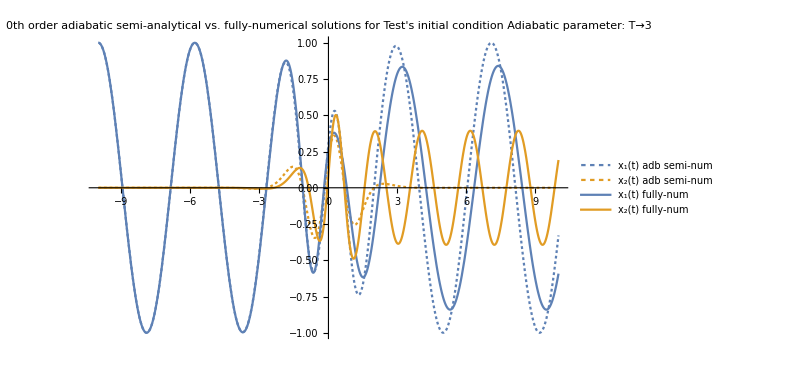

```mathematica
Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.paramTest/.icOsc1
],relevantdomain,
PlotRange->All,
PlotStyle->Flatten[{style0th,stylenum},1],
PlotLegends->{
"x_1(t) adb semi-num","x_2(t) adb semi-num"(*,"x_3(t) adb semi-num"*),
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order adiabatic semi-analytical vs. fully-numerical solutions for Test's initial condition
Adiabatic parameter: T"->3,
ImageSize->600]
```

#### Manipulable plot - paramTest

```mathematica
Manipulate[
Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->All,
PlotStyle->Flatten[{style0th,stylenum},1],
PlotLegends->{
"x_1(t) adb semi-num","x_2(t) adb semi-num"(*,"x_3(t) adb semi-num"*),
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order adiabatic semi-analytical vs. fully-numerical solutions",
ImageSize->600],
Style["Parameters",12],
{{ω1,ω1/.paramTest,"ω_1"},0.1,5},{{α1,α1/.paramTest,"α_1"},0.1,5},{{τ1,τ1/.paramTest,"τ_1"},0.1,5},
{{ω2,ω2/.paramTest,"ω_2"},0.1,5},{{α2,α2/.paramTest,"α_2"},0.1,5},{{τ2,τ2/.paramTest,"τ_2"},0.1,5},
{{αc,αc/.paramTest,"α_c"},0.01,5},{{τc,τc/.paramTest,"τ_c"},0.1,5},Style["
Initial conditions",12],{{A1,1,"A_1"},-10,10},{{A2,0,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,T/.paramTest},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

#### Manipulable plot - 1

```mathematica
Manipulate[
Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->All,
PlotStyle->Flatten[{style0th,stylenum},1],
PlotLegends->{
"x_1(t) adb semi-num","x_2(t) adb semi-num"(*,"x_3(t) adb semi-num"*),
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order adiabatic semi-analytical vs. fully-numerical solutions",
ImageSize->600],
Style["Parameters",12],
{{ω1,0.71,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,0.5,"τ_1"},0.1,5},
{{ω2,0.8,"ω_2"},0.1,5},{{α2,2,"α_2"},0.1,5},{{τ2,1.41,"τ_2"},0.1,5},
{{αc,2.96,"α_c"},0.01,5},{{τc,1.17,"τ_c"},0.1,5},Style["
Initial conditions",12],{{A1,1,"A_1"},-10,10},{{A2,0,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,3,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

#### Manipulable plot - 2

```mathematica
Manipulate[
Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->All,
PlotStyle->Flatten[{style0th,stylenum},1],
PlotLegends->{
"x_1(t) adb semi-num","x_2(t) adb semi-num"(*,"x_3(t) adb semi-num"*),
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order adiabatic semi-analytical vs. fully-numerical solutions",
ImageSize->600],
Style["Parameters",12],
{{ω1,0.67,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,0.5,"τ_1"},0.1,5},
{{ω2,0.92,"ω_2"},0.1,5},{{α2,2,"α_2"},0.1,5},{{τ2,1.41,"τ_2"},0.1,5},
{{αc,2.96,"α_c"},0.1,5},{{τc,1.17,"τ_c"},0.1,5},Style["
Initial conditions",12],{{A1,1,"A_1"},-10,10},{{A2,0,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,3.3},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

### 1st adiabatic approx. vs. exact solution

#### Static plot

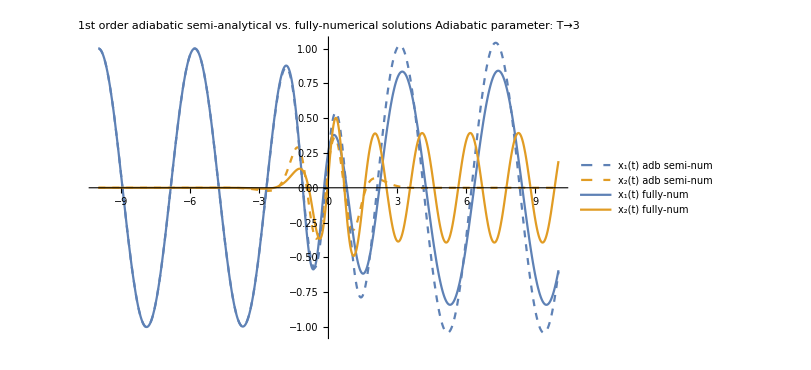

```mathematica
Plot[
Evaluate@Re[{
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff/.paramTest/.icOsc1
],relevantdomain,
PlotRange->All,
PlotStyle->Flatten[{style1st,stylenum},1],
PlotLegends->{
"x_1(t) adb semi-num","x_2(t) adb semi-num"(*,"x_3(t) adb semi-num"*),
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"1st order adiabatic semi-analytical vs. fully-numerical solutions
Adiabatic parameter: T"->3,
ImageSize->600]
```

#### NEW PLOT

Style["Parameters",12],
{{ω1,0.71,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,0.5,"τ_1"},0.1,5},
{{ω2,0.8,"ω_2"},0.1,5},{{α2,2,"α_2"},0.1,5},{{τ2,1.41,"τ_2"},0.1,5},
{{αc,2.96,"α_c"},0.1,5},{{τc,1,"τ_c"},0.1,5},Style["
Initial conditions",12],{{A1,1,"A_1"},-10,10},{{A2,0,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,3,"T "},1,Tmax},

```mathematica
Manipulate[
Plot[
Evaluate@Re[{
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->All,
PlotStyle->Flatten[{style1st,stylenum},1],
PlotLegends->{
"x_1(t) adb semi-num","x_2(t) adb semi-num"(*,"x_3(t) adb semi-num"*),
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"1st order adiabatic semi-analytical vs. fully-numerical solutions",
ImageSize->600],
Style["Parameters",12],
{{ω1,4Pi,"ω_1"},0.1,20},{{α1,2Pi,"α_1"},0.1,20},{{τ1,1,"τ_1"},0.1,5},
{{ω2,3.5Pi,"ω_2"},0.1,20},{{α2,Pi,"α_2"},0.1,20},{{τ2,1,"τ_2"},0.1,5},
{{αc,Pi,"α_c"},0.1,20},{{τc,1,"τ_c"},0.1,5},Style["
Initial conditions",12],{{A1,1,"A_1"},-10,10},{{A2,0,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,1,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

#### Manipulable plot - 1

```mathematica
Manipulate[
Plot[
Evaluate@Re[{
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->All,
PlotStyle->Flatten[{style1st,stylenum},1],
PlotLegends->{
"x_1(t) adb semi-num","x_2(t) adb semi-num"(*,"x_3(t) adb semi-num"*),
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"1st order adiabatic semi-analytical vs. fully-numerical solutions",
ImageSize->600],
Style["Parameters",12],
{{ω1,0.71,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,0.5,"τ_1"},0.1,5},
{{ω2,0.8,"ω_2"},0.1,5},{{α2,2,"α_2"},0.1,5},{{τ2,1.41,"τ_2"},0.1,5},
{{αc,2.96,"α_c"},0.1,5},{{τc,1.17,"τ_c"},0.1,5},Style["
Initial conditions",12],{{A1,1,"A_1"},-10,10},{{A2,0,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,3,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

#### Manipulable plot - 2

```mathematica
Manipulate[
Plot[
Evaluate@Re[{
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->All,
PlotStyle->Flatten[{style1st,stylenum},1],
PlotLegends->{
"x_1(t) adb semi-num","x_2(t) adb semi-num"(*,"x_3(t) adb semi-num"*),
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"1st order adiabatic semi-analytical vs. fully-numerical solutions",
ImageSize->600],
Style["Parameters",12],
{{ω1,0.67,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,0.5,"τ_1"},0.1,5},
{{ω2,0.92,"ω_2"},0.1,5},{{α2,2,"α_2"},0.1,5},{{τ2,1.41,"τ_2"},0.1,5},
{{αc,2.96,"α_c"},0.1,5},{{τc,1.17,"τ_c"},0.1,5},Style["
Initial conditions",12],{{A1,1,"A_1"},-10,10},{{A2,0,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,3.3,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

### 0th and 1st adiabatic approx. vs. exact solution - Only oscillator 1 initially excited

#### Static plot (T → 3)

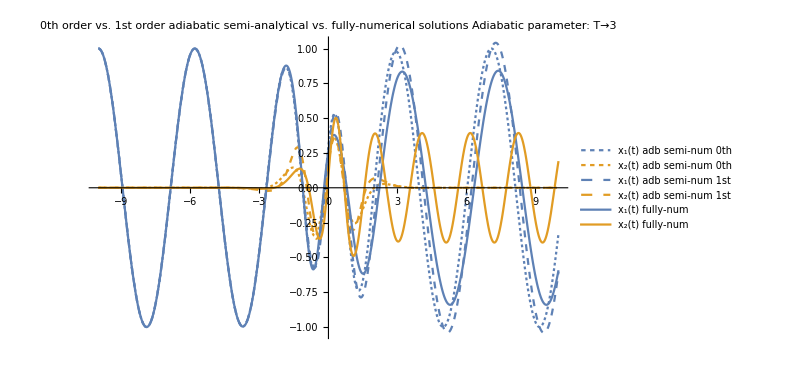

```mathematica
Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff/.paramTest/.icOsc1
],relevantdomain,
PlotRange->All,
PlotStyle->Flatten[{style0th,style1st,stylenum},1],
PlotLegends->{
"x_1(t) adb semi-num 0th","x_2(t) adb semi-num 0th",(*"x_3(t) adb semi-num 0th",*)
"x_1(t) adb semi-num 1st","x_2(t) adb semi-num 1st",(*"x_3(t) adb semi-num 1st",*)
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order vs. 1st order adiabatic semi-analytical vs. fully-numerical solutions
Adiabatic parameter: T"->3,
ImageSize->600]
```

#### Static plot (T → 10)

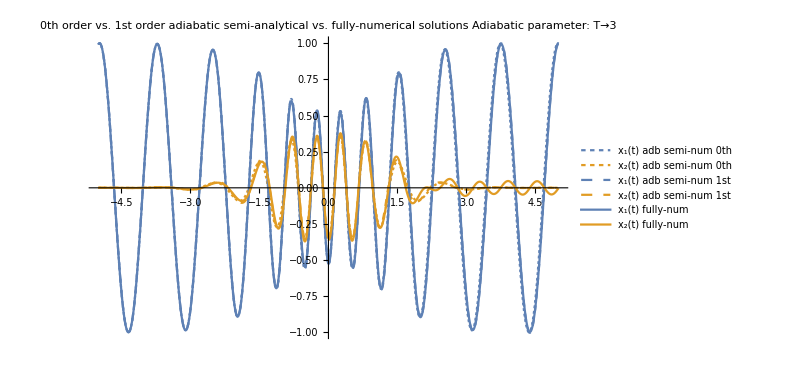

```mathematica
Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff/.T->10/.paramTest/.icOsc1
],{t,ti/2,tf/2},
PlotRange->All,
PlotStyle->Flatten[{style0th,style1st,stylenum},1],
PlotLegends->{
"x_1(t) adb semi-num 0th","x_2(t) adb semi-num 0th",(*"x_3(t) adb semi-num 0th",*)
"x_1(t) adb semi-num 1st","x_2(t) adb semi-num 1st",(*"x_3(t) adb semi-num 1st",*)
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order vs. 1st order adiabatic semi-analytical vs. fully-numerical solutions
Adiabatic parameter: T"->3,
ImageSize->600]
```

#### Manipulable plot

```mathematica
Manipulate[
Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->All,
PlotStyle->Flatten[{style0th,style1st,stylenum},1],
PlotLegends->{
"x_1(t) adb semi-num 0th","x_2(t) adb semi-num 0th",(*"x_3(t) adb semi-num 0th",*)
"x_1(t) adb semi-num 1st","x_2(t) adb semi-num 1st",(*"x_3(t) adb semi-num 1st",*)
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order vs. 1st order adiabatic semi-analytical vs. fully-numerical solutions",
ImageSize->600],
Style["Parameters",12],
{{ω1,0.71,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,0.5,"τ_1"},0.1,5},
{{ω2,0.8,"ω_2"},0.1,5},{{α2,2,"α_2"},0.1,5},{{τ2,1.41,"τ_2"},0.1,5},
{{αc,2.96,"α_c"},0.1,5},{{τc,1.17,"τ_c"},0.1,5},Style["
Initial conditions",12],{{A1,1,"A_1"},-10,10},{{A2,0,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,3,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

## Adiabatic vs. exact - Both oscillators initially excited (good results)

#### Comment

Contrary to what I expected, the sets of replacement rules  constsInPhase  and  constsAntiPhase  are not needed. Or rather, they do not work. Maybe they could be amended, but it is not necessary since the one that does work is the set  constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]  for arbitrary initial conditions. This is great because works for any i.c.’s, and we only need to specify them afterwards.

(Obs: The constants  constsNum  for arbitrary i.c.’s are computed at zero order, so they do need  constsHOsOff  or other higher-order constants specification.)

### In- and Anti-Phase constants and linear independence

```mathematica
Chop[(*constsList/.*)constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.paramTest/.icInPhase,10^-6]
```

{ζ_(0,1,1)→0,ζ_(0,1,-1)→0.707107,ζ_(0,2,1)→0,ζ_(0,2,-1)→0.5}

```mathematica
Chop[(*constsList/.*)constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.paramTest/.icAntiPhase,10^-6]
```

{ζ_(0,1,1)→0,ζ_(0,1,-1)→0.707107,ζ_(0,2,1)→0,ζ_(0,2,-1)→-0.5}

### 0th and 1st adiabatic orders - In-phase solution

#### Static plot (T → 3)

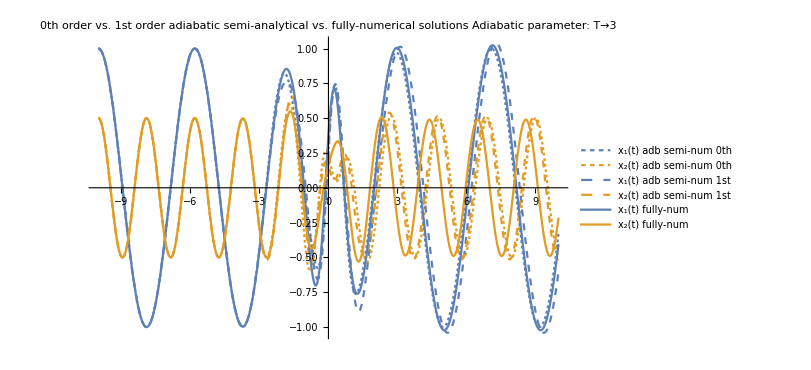

```mathematica
Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff/.paramTest/.icInPhase
],relevantdomain,
PlotRange->All,
PlotStyle->Flatten[{style0th,style1st,stylenum},1],
PlotLegends->{
"x_1(t) adb semi-num 0th","x_2(t) adb semi-num 0th",(*"x_3(t) adb semi-num 0th",*)
"x_1(t) adb semi-num 1st","x_2(t) adb semi-num 1st",(*"x_3(t) adb semi-num 1st",*)
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order vs. 1st order adiabatic semi-analytical vs. fully-numerical solutions
Adiabatic parameter: T"->3,
ImageSize->600]
```

#### Static plot (T → 10)

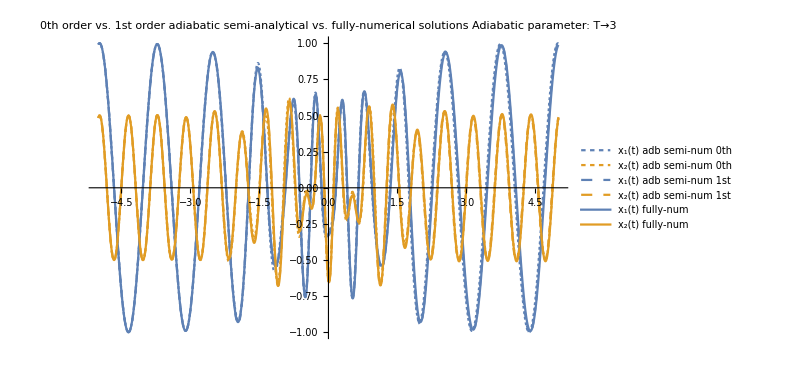

```mathematica
Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff/.T->10/.paramTest/.icInPhase
],{t,ti/2,tf/2},
PlotRange->All,
PlotStyle->Flatten[{style0th,style1st,stylenum},1],
PlotLegends->{
"x_1(t) adb semi-num 0th","x_2(t) adb semi-num 0th",(*"x_3(t) adb semi-num 0th",*)
"x_1(t) adb semi-num 1st","x_2(t) adb semi-num 1st",(*"x_3(t) adb semi-num 1st",*)
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order vs. 1st order adiabatic semi-analytical vs. fully-numerical solutions
Adiabatic parameter: T"->3,
ImageSize->600]
```

#### Manipulable plot

```mathematica
Manipulate[
Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->All,
PlotStyle->Flatten[{style0th,style1st,stylenum},1],
PlotLegends->{
"x_1(t) adb semi-num 0th","x_2(t) adb semi-num 0th",(*"x_3(t) adb semi-num 0th",*)
"x_1(t) adb semi-num 1st","x_2(t) adb semi-num 1st",(*"x_3(t) adb semi-num 1st",*)
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order vs. 1st order adiabatic semi-analytical vs. fully-numerical solutions",
ImageSize->600],
Style["Parameters",12],
{{ω1,0.71,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,0.5,"τ_1"},0.1,5},
{{ω2,0.8,"ω_2"},0.1,5},{{α2,2,"α_2"},0.1,5},{{τ2,1.41,"τ_2"},0.1,5},
{{αc,2.96,"α_c"},0.1,5},{{τc,1.17,"τ_c"},0.1,5},Style["
Initial conditions",12],{{A1,A1/.icInPhase,"A_1"},-10,10},{{A2,A2/.icInPhase,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,3,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

### 0th and 1st adiabatic orders - Anti-phase solution

#### Static plot (T → 3)

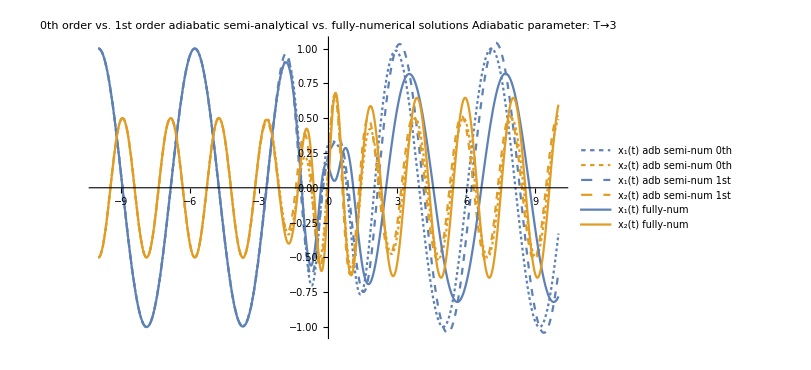

```mathematica
Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff/.paramTest/.icAntiPhase
],relevantdomain,
PlotRange->All,
PlotStyle->Flatten[{style0th,style1st,stylenum},1],
PlotLegends->{
"x_1(t) adb semi-num 0th","x_2(t) adb semi-num 0th",(*"x_3(t) adb semi-num 0th",*)
"x_1(t) adb semi-num 1st","x_2(t) adb semi-num 1st",(*"x_3(t) adb semi-num 1st",*)
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order vs. 1st order adiabatic semi-analytical vs. fully-numerical solutions
Adiabatic parameter: T"->3,
ImageSize->600]
```

#### Static plot (T → 10)

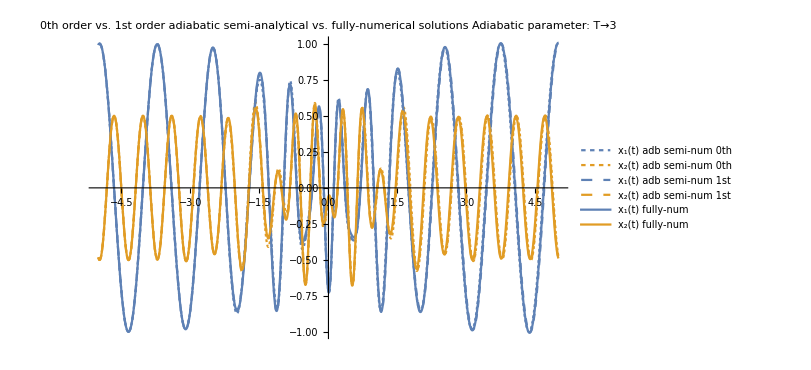

```mathematica
Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff/.T->10/.paramTest/.icAntiPhase
],{t,ti/2,tf/2},
PlotRange->All,
PlotStyle->Flatten[{style0th,style1st,stylenum},1],
PlotLegends->{
"x_1(t) adb semi-num 0th","x_2(t) adb semi-num 0th",(*"x_3(t) adb semi-num 0th",*)
"x_1(t) adb semi-num 1st","x_2(t) adb semi-num 1st",(*"x_3(t) adb semi-num 1st",*)
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order vs. 1st order adiabatic semi-analytical vs. fully-numerical solutions
Adiabatic parameter: T"->3,
ImageSize->600]
```

#### Manipulable plot

```mathematica
Manipulate[
Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->All,
PlotStyle->Flatten[{style0th,style1st,stylenum},1],
PlotLegends->{
"x_1(t) adb semi-num 0th","x_2(t) adb semi-num 0th",(*"x_3(t) adb semi-num 0th",*)
"x_1(t) adb semi-num 1st","x_2(t) adb semi-num 1st",(*"x_3(t) adb semi-num 1st",*)
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order vs. 1st order adiabatic semi-analytical vs. fully-numerical solutions",
ImageSize->600],
Style["Parameters",12],
{{ω1,0.71,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,0.5,"τ_1"},0.1,5},
{{ω2,0.8,"ω_2"},0.1,5},{{α2,2,"α_2"},0.1,5},{{τ2,1.41,"τ_2"},0.1,5},
{{αc,2.96,"α_c"},0.1,5},{{τc,1.17,"τ_c"},0.1,5},Style["
Initial conditions",12],{{A1,A1/.icAntiPhase,"A_1"},-10,10},{{A2,A2/.icAntiPhase,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,3,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

### Solutions with 2nd adiabatic order (switched off)

#### In-phase solution - Static plot (T → 3)

```mathematica
(*Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff/.paramTest/.icInPhase
],relevantdomain,
PlotRange->All,
PlotStyle->Flatten[{style0th,style1st,stylenum},1],
PlotLegends->{
"x_1(t) adb semi-num 0th","x_2(t) adb semi-num 0th",(*"x_3(t) adb semi-num 0th",*)
"x_1(t) adb semi-num 1st","x_2(t) adb semi-num 1st",(*"x_3(t) adb semi-num 1st",*)
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order vs. 1st order adiabatic semi-analytical vs. fully-numerical solutions
Adiabatic parameter: T"->3,
ImageSize->600]*)
```

#### In-phase solution - Static plot (T → 10)

```mathematica
(*Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff/.T->10/.paramTest/.icInPhase
],{t,ti/2,tf/2},
PlotRange->All,
PlotStyle->Flatten[{style0th,style1st,stylenum},1],
PlotLegends->{
"x_1(t) adb semi-num 0th","x_2(t) adb semi-num 0th",(*"x_3(t) adb semi-num 0th",*)
"x_1(t) adb semi-num 1st","x_2(t) adb semi-num 1st",(*"x_3(t) adb semi-num 1st",*)
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order vs. 1st order adiabatic semi-analytical vs. fully-numerical solutions
Adiabatic parameter: T"->3,
ImageSize->600]*)
```

#### Anti-phase solution - Static plot (T → 3)

```mathematica
(*Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff/.paramTest/.icAntiPhase
],relevantdomain,
PlotRange->All,
PlotStyle->Flatten[{style0th,style1st,stylenum},1],
PlotLegends->{
"x_1(t) adb semi-num 0th","x_2(t) adb semi-num 0th",(*"x_3(t) adb semi-num 0th",*)
"x_1(t) adb semi-num 1st","x_2(t) adb semi-num 1st",(*"x_3(t) adb semi-num 1st",*)
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order vs. 1st order adiabatic semi-analytical vs. fully-numerical solutions
Adiabatic parameter: T"->3,
ImageSize->600]*)
```

#### Anti-phase solution - Static plot (T → 10)

```mathematica
(*Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff/.T->10/.paramTest/.icAntiPhase
],{t,ti/2,tf/2},
PlotRange->All,
PlotStyle->Flatten[{style0th,style1st,stylenum},1],
PlotLegends->{
"x_1(t) adb semi-num 0th","x_2(t) adb semi-num 0th",(*"x_3(t) adb semi-num 0th",*)
"x_1(t) adb semi-num 1st","x_2(t) adb semi-num 1st",(*"x_3(t) adb semi-num 1st",*)
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order vs. 1st order adiabatic semi-analytical vs. fully-numerical solutions
Adiabatic parameter: T"->3,
ImageSize->600]*)
```

### Choosing regimes (manipulable plots) - First attempt

I’ll use in-phase i.c.’s, so the approximation is good at late times as well. (Obs: Anti-phase i.c.’s can be achieved here just by setting A_2<0.)

NOTE that for in/anti-phase initial conditions, neither of the oscillator starts still. Hence, the coupling effect does not excite the other oscillator, but only alter their dynamics. This makes the near/apart from resonance effect to be much less noticeable. This can be checked playing with the strength of the coupling through α_c.

#### Adiabatic regime

```mathematica
Manipulate[
Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral,
Sech[t/τc]
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->All,
PlotStyle->Flatten[{style0th,style1st,stylenum},1],
PlotLegends->{
"x_1(t) adb semi-num 0th","x_2(t) adb semi-num 0th",(*"x_3(t) adb semi-num 0th",*)
"x_1(t) adb semi-num 1st","x_2(t) adb semi-num 1st",(*"x_3(t) adb semi-num 1st",*)
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order vs. 1st order adiabatic semi-analytical vs. fully-numerical solutions",
ImageSize->600],
Style["Parameters",12],
{{ω1,2π,"ω_1"},0.1,20},{{α1,4π,"α_1"},0.1,20},{{τ1,1,"τ_1"},0.1,20},
{{ω2,1,1.5π,"ω_2"},0.1,20},{{α2,3π,"α_2"},0.1,20},{{τ2,1,"τ_2"},0.1,20},
{{αc,1.5π,"α_c"},0.1,20},{{τc,1,"τ_c"},0.1,20},Style["
Initial conditions",12],{{A1,A1/.icInPhase,"A_1"},-10,10},{{A2,A2/.icInPhase,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,1,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

#### Adiabatic regime, with frequencies further apart

```mathematica
Manipulate[
Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral,
Sech[t/τc]
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->All,
PlotStyle->Flatten[{style0th,style1st,stylenum},1],
PlotLegends->{
"x_1(t) adb semi-num 0th","x_2(t) adb semi-num 0th",(*"x_3(t) adb semi-num 0th",*)
"x_1(t) adb semi-num 1st","x_2(t) adb semi-num 1st",(*"x_3(t) adb semi-num 1st",*)
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order vs. 1st order adiabatic semi-analytical vs. fully-numerical solutions",
ImageSize->600],
Style["Parameters",12],
{{ω1,3π,"ω_1"},0.1,20},{{α1,7π,"α_1"},0.1,30},{{τ1,1,"τ_1"},0.1,20},
{{ω2,1π,"ω_2"},0.1,20},{{α2,3π,"α_2"},0.1,20},{{τ2,1,"τ_2"},0.1,20},
{{αc,1π,"α_c"},0.1,20},{{τc,1,"τ_c"},0.1,20},Style["
Initial conditions",12],{{A1,A1/.icInPhase,"A_1"},-10,10},{{A2,A2/.icInPhase,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,1,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

#### Adiabatic regime but with much stronger coupling

```mathematica
Manipulate[
Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral,
Sech[t/τc]
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff
],{t,Center-WindowSize/2,Center+WindowSize/2},AspectRatio->0.3,
PlotRange->All,
PlotStyle->Flatten[{style0th,style1st,stylenum},1],
PlotLegends->{
"x_1(t) adb semi-num 0th","x_2(t) adb semi-num 0th",(*"x_3(t) adb semi-num 0th",*)
"x_1(t) adb semi-num 1st","x_2(t) adb semi-num 1st",(*"x_3(t) adb semi-num 1st",*)
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order vs. 1st order adiabatic semi-analytical vs. fully-numerical solutions",
ImageSize->900],
Style["Parameters",12],
{{ω1,2π,"ω_1"},0.1,20},{{α1,2π,"α_1"},0.1,20},{{τ1,1,"τ_1"},0.1,20},
{{ω2,1.6π,"ω_2"},0.1,20},{{α2,π,"α_2"},0.1,20},{{τ2,1,"τ_2"},0.1,20},
{{αc,4π,"α_c"},0.1,20},{{τc,1,"τ_c"},0.1,20},Style["
Initial conditions",12],{{A1,A1/.icInPhase,"A_1"},-10,10},{{A2,A2/.icInPhase,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,2},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,Abs[ti]2/3,"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

#### Leaving the adiabatic regime (quite curious behavior)

As one would expect, decreasing the τ_i’s worsens the approximation, just like in the scalar-WKB case.

HOWEVER, decreasing the coupling’s adiabaticity through a smaller τ_c makes the approximation to recover a great accuracy!

It does so, of course, until the breakdown of the initial conditions, but I still think that is not a problem of the approximation.

AH, I JUST REALIZED: THIS MIGHT BE A BREAKDOWN OF THE NUMERICAL INITIAL CONDITIONS, given that the Sech function looses numerical accuracy very quickly due to its exponential character!!!

```mathematica
Manipulate[
Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral,
Sech[t/τc]
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->All,
PlotStyle->Flatten[{style0th,style1st,stylenum},1],
PlotLegends->{
"x_1(t) adb semi-num 0th","x_2(t) adb semi-num 0th",(*"x_3(t) adb semi-num 0th",*)
"x_1(t) adb semi-num 1st","x_2(t) adb semi-num 1st",(*"x_3(t) adb semi-num 1st",*)
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order vs. 1st order adiabatic semi-analytical vs. fully-numerical solutions",
ImageSize->600],
Style["Parameters",12],
{{ω1,2π,"ω_1"},0.1,20},{{α1,4π,"α_1"},0.1,20},{{τ1,0.8,"τ_1"},0.1,20},
{{ω2,1.5π,"ω_2"},0.1,20},{{α2,3π,"α_2"},0.1,20},{{τ2,0.8,"τ_2"},0.1,20},
{{αc,1.5π,"α_c"},0.1,20},{{τc,0.6,"τ_c"},0.1,20},Style["
Initial conditions",12],{{A1,A1/.icInPhase,"A_1"},-10,10},{{A2,A2/.icInPhase,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,1,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

### Choosing regimes (manipulable plots) - Final plots

#### Adiabatic regime

```mathematica
Manipulate[{
(*c=*)(2αc^2)/(ω1^2+ω2^2+α1^2+α2^2)//N,
T*τc(ω1+ω2)/π//N,
Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral,
(2αc^2)/(ω1^2+ω2^2+α1^2+α2^2)Sech[t/τc],
1+α1^2Sech[t/τ1]/ω1^2,
0.97+α2^2Sech[t/τ2]/ω2^2
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->{-1.17,1.57},
PlotStyle->Flatten[{style0th,style1st,stylenum,{{Dashed,RGBColor[0.560181, 0.691569, 0.194885]}},{{Dotted,RGBColor[0.753628, 0.82591, 0.991257]}},{{Dotted,RGBColor[1, 0.784756, 0.323308]}}},1],
PlotLegends->{
"x_1(t) adb semi-num 0th","x_2(t) adb semi-num 0th",(*"x_3(t) adb semi-num 0th",*)
"x_1(t) adb semi-num 1st","x_2(t) adb semi-num 1st",(*"x_3(t) adb semi-num 1st",*)
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order vs. 1st order adiabatic semi-analytical vs. fully-numerical solutions",
ImageSize->600]},
Style["Parameters",12],
{{ω1,2π,"ω_1"},0.1,20},{{α1,2π,"α_1"},0.1,20},{{τ1,1,"τ_1"},0.1,20},
{{ω2,π,"ω_2"},0.1,20},{{α2,π,"α_2"},0.1,20},{{τ2,1,"τ_2"},0.1,20},
{{αc,2π,"α_c"},0.1,20},{{τc,1,"τ_c"},0.1,20},Style["
Initial conditions",12],{{A1,A1/.icInPhase,"A_1"},-10,10},{{A2,A2/.icInPhase,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,1,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

#### Fairly adiabatic regime

```mathematica
Manipulate[{
(*c=*)(2αc^2)/(ω1^2+ω2^2+α1^2+α2^2)//N,
T*τc(ω1+ω2)/π//N,
Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral,
(2αc^2)/(ω1^2+ω2^2+α1^2+α2^2)Sech[t/τc],
1+α1^2Sech[t/τ1]/ω1^2,
0.97+α2^2Sech[t/τ2]/ω2^2
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->{-1.17,1.57},
PlotStyle->Flatten[{style0th,style1st,stylenum,{{Dashed,RGBColor[0.560181, 0.691569, 0.194885]}},{{Dotted,RGBColor[0.753628, 0.82591, 0.991257]}},{{Dotted,RGBColor[1, 0.784756, 0.323308]}}},1],
PlotLegends->{
"x_1(t) adb semi-num 0th","x_2(t) adb semi-num 0th",(*"x_3(t) adb semi-num 0th",*)
"x_1(t) adb semi-num 1st","x_2(t) adb semi-num 1st",(*"x_3(t) adb semi-num 1st",*)
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order vs. 1st order adiabatic semi-analytical vs. fully-numerical solutions",
ImageSize->600]},
Style["Parameters",12],
{{ω1,1.4π,"ω_1"},0.1,20},{{α1,1.4π,"α_1"},0.1,20},{{τ1,1,"τ_1"},0.1,20},
{{ω2,0.4π,"ω_2"},0.1,20},{{α2,0.4π,"α_2"},0.1,20},{{τ2,1,"τ_2"},0.1,20},
{{αc,1.4π,"α_c"},0.1,20},{{τc,1,"τ_c"},0.1,20},Style["
Initial conditions",12],{{A1,A1/.icInPhase,"A_1"},-10,10},{{A2,A2/.icInPhase,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,1,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,Abs[ti]*1.5,"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

#### Leaving the adiabatic regime - Near resonance

```mathematica
Manipulate[{
(*c=*)(2αc^2)/(ω1^2+ω2^2+α1^2+α2^2)//N,
T*τc(ω1+ω2)/π//N,
Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral,
(2αc^2)/(ω1^2+ω2^2+α1^2+α2^2)Sech[t/τc],
1+α1^2Sech[t/τ1]/ω1^2,
0.97+α2^2Sech[t/τ2]/ω2^2
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->{-1.17,1.57},
PlotStyle->Flatten[{style0th,style1st,stylenum,{{Dashed,RGBColor[0.560181, 0.691569, 0.194885]}},{{Dotted,RGBColor[0.753628, 0.82591, 0.991257]}},{{Dotted,RGBColor[1, 0.784756, 0.323308]}}},1],
PlotLegends->{
"x_1(t) adb semi-num 0th","x_2(t) adb semi-num 0th",(*"x_3(t) adb semi-num 0th",*)
"x_1(t) adb semi-num 1st","x_2(t) adb semi-num 1st",(*"x_3(t) adb semi-num 1st",*)
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order vs. 1st order adiabatic semi-analytical vs. fully-numerical solutions",
ImageSize->600]},
Style["Parameters",12],
{{ω1,1.1π,"ω_1"},0.1,20},{{α1,1.1π,"α_1"},0.1,20},{{τ1,1,"τ_1"},0.1,20},
{{ω2,0.9π,"ω_2"},0.1,20},{{α2,0.9π,"α_2"},0.1,20},{{τ2,1,"τ_2"},0.1,20},
{{αc,1.3π,"α_c"},0.1,20},{{τc,1,"τ_c"},0.1,20},Style["
Initial conditions",12],{{A1,A1/.icInPhase,"A_1"},-10,10},{{A2,A2/.icInPhase,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,1,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,Abs[ti]*1.5,"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

#### Leaving the adiabatic regime

```mathematica
Manipulate[{
(*c=*)(2αc^2)/(ω1^2+ω2^2+α1^2+α2^2)//N,
T*τc(ω1+ω2)/π//N,
Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral,
(2αc^2)/(ω1^2+ω2^2+α1^2+α2^2)Sech[t/τc],
1+α1^2Sech[t/τ1]/ω1^2,
0.97+α2^2Sech[t/τ2]/ω2^2
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->{-1.17,1.57},
PlotStyle->Flatten[{style0th,style1st,stylenum,{{Dashed,RGBColor[0.560181, 0.691569, 0.194885]}},{{Dotted,RGBColor[0.753628, 0.82591, 0.991257]}},{{Dotted,RGBColor[1, 0.784756, 0.323308]}}},1],
PlotLegends->{
"x_1(t) adb semi-num 0th","x_2(t) adb semi-num 0th",(*"x_3(t) adb semi-num 0th",*)
"x_1(t) adb semi-num 1st","x_2(t) adb semi-num 1st",(*"x_3(t) adb semi-num 1st",*)
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order vs. 1st order adiabatic semi-analytical vs. fully-numerical solutions",
ImageSize->600]},
Style["Parameters",12],
{{ω1,0.8π,"ω_1"},0.1,20},{{α1,0.8π,"α_1"},0.1,20},{{τ1,1,"τ_1"},0.1,20},
{{ω2,0.4π,"ω_2"},0.1,20},{{α2,0.4π,"α_2"},0.1,20},{{τ2,1,"τ_2"},0.1,20},
{{αc,2π,"α_c"},0.1,20},{{τc,1,"τ_c"},0.1,20},Style["
Initial conditions",12],{{A1,A1/.icInPhase,"A_1"},-10,10},{{A2,A2/.icInPhase,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,1,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,Abs[ti]*1.2,"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

#### Recovering adiabaticity

```mathematica
Manipulate[{
(*c=*)(2αc^2)/(ω1^2+ω2^2+α1^2+α2^2)//N,
T*τc(ω1+ω2)/π//N,
Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral,
(2αc^2)/(ω1^2+ω2^2+α1^2+α2^2)Sech[t/τc],
1+α1^2Sech[t/τ1]/ω1^2,
0.97+α2^2Sech[t/τ2]/ω2^2
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->{-1.17,1.57},
PlotStyle->Flatten[{style0th,style1st,stylenum,{{Dashed,RGBColor[0.560181, 0.691569, 0.194885]}},{{Dotted,RGBColor[0.753628, 0.82591, 0.991257]}},{{Dotted,RGBColor[1, 0.784756, 0.323308]}}},1],
PlotLegends->{
"x_1(t) adb semi-num 0th","x_2(t) adb semi-num 0th",(*"x_3(t) adb semi-num 0th",*)
"x_1(t) adb semi-num 1st","x_2(t) adb semi-num 1st",(*"x_3(t) adb semi-num 1st",*)
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order vs. 1st order adiabatic semi-analytical vs. fully-numerical solutions",
ImageSize->600]},
Style["Parameters",12],
{{ω1,0.8π,"ω_1"},0.1,20},{{α1,0.8π,"α_1"},0.1,20},{{τ1,1,"τ_1"},0.1,20},
{{ω2,0.4π,"ω_2"},0.1,20},{{α2,0.4π,"α_2"},0.1,20},{{τ2,1,"τ_2"},0.1,20},
{{αc,2π,"α_c"},0.1,20},{{τc,1,"τ_c"},0.1,20},Style["
Initial conditions",12],{{A1,A1/.icInPhase,"A_1"},-10,10},{{A2,A2/.icInPhase,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,3,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,Abs[ti]*1.2,"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

#### Adiabatic but strong coupling regime

```mathematica
Manipulate[{
(*c=*)(2αc^2)/(ω1^2+ω2^2+α1^2+α2^2)//N,
T*τc(ω1+ω2)/π//N,
Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral,
(2αc^2)/(ω1^2+ω2^2+α1^2+α2^2)Sech[t/τc],
1+α1^2Sech[t/τ1]/ω1^2,
0.97+α2^2Sech[t/τ2]/ω2^2
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->{-1.17,1.57},AspectRatio->0.6180339887498948/2,
PlotStyle->Flatten[{style0th,style1st,stylenum,{{Dashed,RGBColor[0.560181, 0.691569, 0.194885]}},{{Dotted,RGBColor[0.753628, 0.82591, 0.991257]}},{{Dotted,RGBColor[1, 0.784756, 0.323308]}}},1],
PlotLegends->{
"x_1(t) adb semi-num 0th","x_2(t) adb semi-num 0th",(*"x_3(t) adb semi-num 0th",*)
"x_1(t) adb semi-num 1st","x_2(t) adb semi-num 1st",(*"x_3(t) adb semi-num 1st",*)
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order vs. 1st order adiabatic semi-analytical vs. fully-numerical solutions",
ImageSize->900]},
Style["Parameters",12],
{{ω1,2π,"ω_1"},0.1,20},{{α1,2π,"α_1"},0.1,20},{{τ1,1,"τ_1"},0.1,20},
{{ω2,π,"ω_2"},0.1,20},{{α2,π,"α_2"},0.1,20},{{τ2,1,"τ_2"},0.1,20},
{{αc,5π,"α_c"},0.1,40},{{τc,1,"τ_c"},0.1,20},Style["
Initial conditions",12],{{A1,A1/.icInPhase,"A_1"},-10,10},{{A2,A2/.icInPhase,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,1,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

## Comparisons with 2nd order (switched off)

#### ↪︎ Take forever, so I switched them off (but I kept the printed plots displayed)

### 2nd order adiabatic semi-analytical vs. fully-numerical solution

#### Static plot

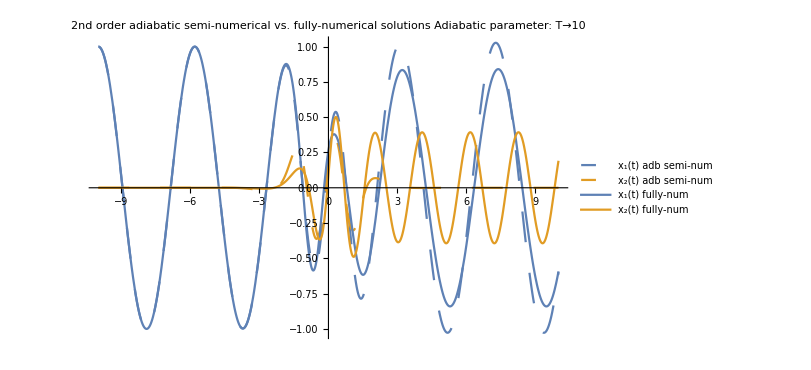

```mathematica
(*Plot[
Evaluate@Re[{
vxAdbNum[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff/.paramTest/.icOsc1
],relevantdomain,
PlotRange->All,
PlotStyle->Flatten[{style2nd,stylenum},1],
PlotLegends->{
"x_1(t) adb semi-num","x_2(t) adb semi-num"(*,"x_3(t) adb semi-num"*),
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"2nd order adiabatic semi-analytical vs. fully-numerical solutions
Adiabatic parameter: T"->3,
ImageSize->600]*)
```

#### Manipulable plot

```mathematica
(*Manipulate[
Plot[
Evaluate@Re[{
vxAdbNum[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->All,
PlotStyle->Flatten[{style2nd,stylenum},1],
PlotLegends->{
"x_1(t) adb semi-num","x_2(t) adb semi-num"(*,"x_3(t) adb semi-num"*),
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"2nd order adiabatic semi-analytical vs. fully-numerical solutions",
ImageSize->600],
Style["Parameters",12],
{{ω1,1/2,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,1,"τ_1"},0.1,5},
{{ω2,1,"ω_2"},0.1,5},{{α2,1,"α_2"},0.1,5},{{τ2,1,"τ_2"},0.1,5},
{{αc,1,"α_c"},0.1,5},{{τc,1,"τ_c"},0.1,5},Style["
Initial conditions",12],{{A1,1,"A_1"},-10,10},{{A2,0,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,3,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]*)
```

### Full comparison: 0th vs. 1st vs. 2nd orders adiabatic semi-analytical solution vs. fully numerical solution

#### Static plot

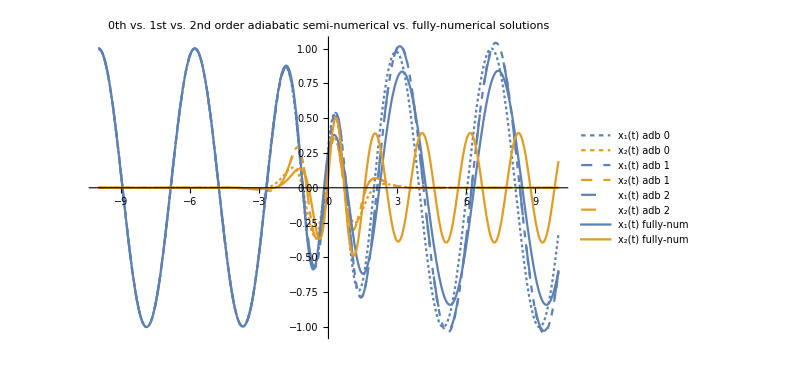

```mathematica
(*Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff/.paramTest/.icOsc1
],relevantdomain,
PlotRange->All,
PlotStyle->Flatten[{style0th,style1st,style2nd,stylenum},1],
PlotLegends->{
"x_1(t) adb 0","x_2(t) adb 0"(*,"x_3(t) adb 0"*),
"x_1(t) adb 1","x_2(t) adb 1"(*,"x_3(t) adb 1"*),
"x_1(t) adb 2","x_2(t) adb 2"(*,"x_3(t) adb 2"*),
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th vs. 1st vs. 2nd order adiabatic semi-analytical vs. fully-numerical solutions",
ImageSize->600]*)
```

#### Manipulable plot

```mathematica
(*Manipulate[
Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->All,
PlotStyle->Flatten[{style0th,style1st,style2nd,stylenum},1],
PlotLegends->{
"x_1(t) adb 0","x_2(t) adb 0"(*,"x_3(t) adb 0"*),
"x_1(t) adb 1","x_2(t) adb 1"(*,"x_3(t) adb 1"*),
"x_1(t) adb 2","x_2(t) adb 2"(*,"x_3(t) adb 2"*),
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th vs. 1st vs. 2nd order adiabatic semi-analytical vs. fully-numerical solutions",
ImageSize->600],
Style["Parameters",12],
{{ω1,1/2,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,1,"τ_1"},0.1,5},
{{ω2,1,"ω_2"},0.1,5},{{α2,1,"α_2"},0.1,5},{{τ2,1,"τ_2"},0.1,5},
{{αc,1,"α_c"},0.1,5},{{τc,1,"τ_c"},0.1,5},Style["
Initial conditions",12],{{A1,1,"A_1"},-10,10},{{A2,0,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,3,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]*)
```

### Partial comparison: 1st vs. 2nd orders adiabatic semi-analytical solution vs. fully-numerical solution

#### Static plot

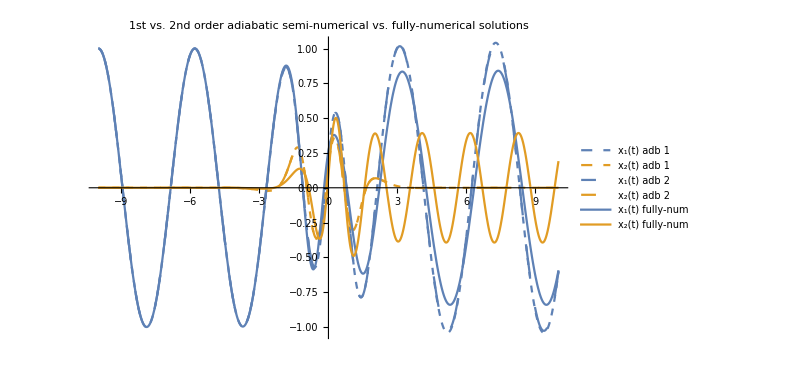

```mathematica
(*Plot[
Evaluate@Re[{
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff/.paramTest/.icOsc1
],relevantdomain,
PlotRange->All,
PlotStyle->Flatten[{style1st,style2nd,stylenum},1],
PlotLegends->{
"x_1(t) adb 1","x_2(t) adb 1"(*,"x_3(t) adb 1"*),
"x_1(t) adb 2","x_2(t) adb 2"(*,"x_3(t) adb 2"*),
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"1st vs. 2nd order adiabatic semi-analytical vs. fully-numerical solutions",
ImageSize->600]*)
```

#### Manipulable plot

```mathematica
(*Manipulate[
Plot[
Evaluate@Re[{
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->All,
PlotStyle->Flatten[{style1st,style2nd,stylenum},1],
PlotLegends->{
"x_1(t) adb 1","x_2(t) adb 1"(*,"x_3(t) adb 1"*),
"x_1(t) adb 2","x_2(t) adb 2"(*,"x_3(t) adb 2"*),
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"1st vs. 2nd order adiabatic semi-analytical vs. fully-numerical solutions",
ImageSize->600],
Style["Parameters",12],
{{ω1,1/2,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,1,"τ_1"},0.1,5},
{{ω2,1,"ω_2"},0.1,5},{{α2,1,"α_2"},0.1,5},{{τ2,1,"τ_2"},0.1,5},
{{αc,1,"α_c"},0.1,5},{{τc,1,"τ_c"},0.1,5},Style["
Initial conditions",12],{{A1,1,"A_1"},-10,10},{{A2,0,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,3,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]*)
```

## Adiabatic vs. perturbative approach

#### Plots for the parameters used in the perturbative approximation

### Parameters used in the perturbative approach

{ω1,ω2,ωc,αc,τc}

```mathematica
plotParamPert[0]={4π,3.5π,0,1π,0.5,2};
plotParamPert[1]={8π,2π,0,2.5π,0.2,3};
plotParamPert[2]={12π,8π,0,4.5π,0.1,3};
plotParamPert[3]={2π,1.6π,0,0.9π,0.5,2};
plotParamPert[4]={2π,1.6π,0,0.9π,0.5,2};
plotParamPert[5]={2π,1.8π,0,1.3π,0.5,2};
plotParamPert[6]={2π,1.4π,0,1.7π,0.1,2};
```

(The last parameter 2-3 was the number of orders plotted; I erase it.)

```mathematica
pertParam[0]={ω1->4π,ω2->3.5π,ωc->0,αc->1π,τc->0.5};
pertParam[1]={ω1->8π,ω2->2π,ωc->0,αc->2.5π,τc->0.2};
pertParam[2]={ω1->12π,ω2->8π,ωc->0,αc->4.5π,τc->0.1};
pertParam[3]={ω1->2π,ω2->1.6π,ωc->0,αc->0.9π,τc->0.5};
pertParam[4]={ω1->2π,ω2->1.6π,ωc->0,αc->0.9π,τc->0.5};
pertParam[5]={ω1->2π,ω2->1.8π,ωc->0,αc->1.3π,τc->0.5};
pertParam[6]={ω1->2π,ω2->1.4π,ωc->0,αc->1.7π,τc->0.1};
```

### Adaptation and plotting function

We also need to include the Pöschl-Teller parameters α_i and τ_i for each frequency;
let’s take them equal to those of the coupling, α_c and τ_c:

```mathematica
pert2adiab={α1->αc,τ1->τc,α2->αc,τ2->τc};
```

```mathematica
PlotPerturbative[params_,ics_]:=Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff/.pert2adiab/.params/.ics/.T->1
],{t,-1,1},
PlotRange->All,
PlotStyle->Flatten[{style0th,style1st,stylenum},1],
PlotLegends->{
"x_1(t) adb semi-num 0th","x_2(t) adb semi-num 0th",(*"x_3(t) adb semi-num 0th",*)
"x_1(t) adb semi-num 1st","x_2(t) adb semi-num 1st",(*"x_3(t) adb semi-num 1st",*)
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order vs. 1st order adiabatic semi-analytical vs. fully-numerical solutions"]
```

### Adiabatic plots for the perturbative parameters

#### Plotting codes (~ 6 sec. each; switched off)

```mathematica
(*PlotPerturbative[pertParam[0],icOsc1]
PlotPerturbative[pertParam[1],icOsc1]
PlotPerturbative[pertParam[2],icOsc1]
PlotPerturbative[pertParam[3],icOsc1]
PlotPerturbative[pertParam[5],icOsc1]
PlotPerturbative[pertParam[6],icOsc1]*)
```

```mathematica
(*PlotPerturbative[pertParam[0],icInPhase]//Quiet
PlotPerturbative[pertParam[1],icInPhase]//Quiet
PlotPerturbative[pertParam[2],icInPhase]//Quiet
PlotPerturbative[pertParam[3],icInPhase]//Quiet
PlotPerturbative[pertParam[5],icInPhase]//Quiet
PlotPerturbative[pertParam[6],icInPhase]//Quiet*)
```

```mathematica
(*PlotPerturbative[pertParam[0],icAntiPhase]//Quiet
PlotPerturbative[pertParam[1],icAntiPhase]//Quiet
PlotPerturbative[pertParam[2],icAntiPhase]//Quiet
PlotPerturbative[pertParam[3],icAntiPhase]//Quiet
PlotPerturbative[pertParam[5],icAntiPhase]//Quiet
PlotPerturbative[pertParam[6],icAntiPhase]//Quiet*)
```

#### Plots for the first single-oscillator i.c.’s

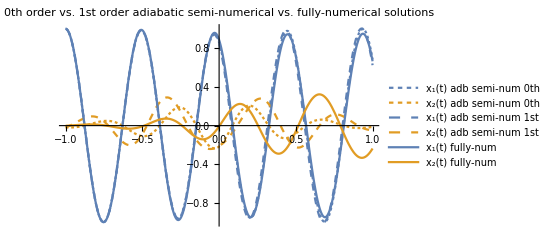

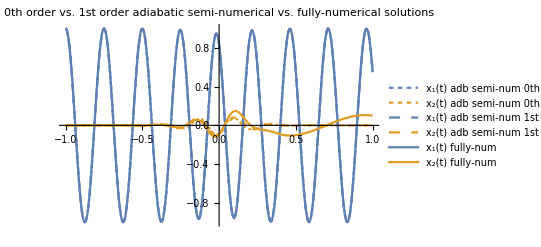

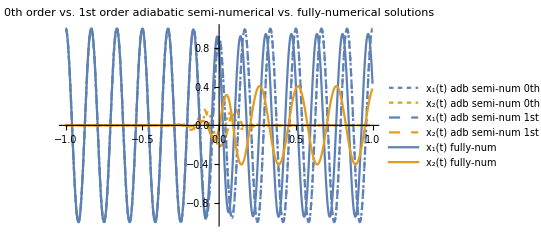

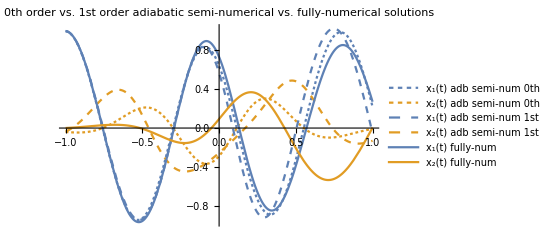

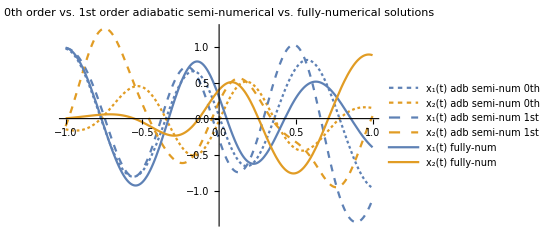

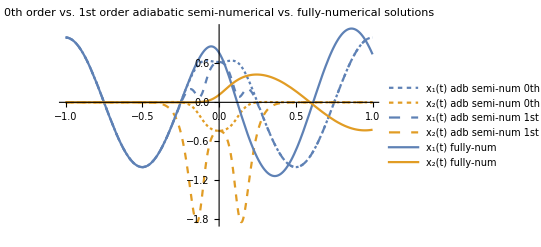

#### Plots for the in-phase i.c.’s

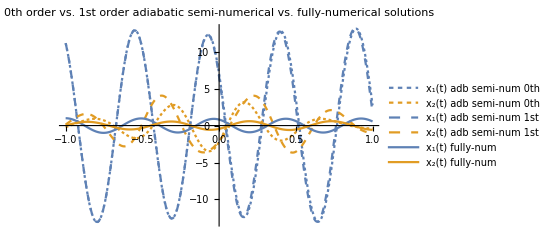

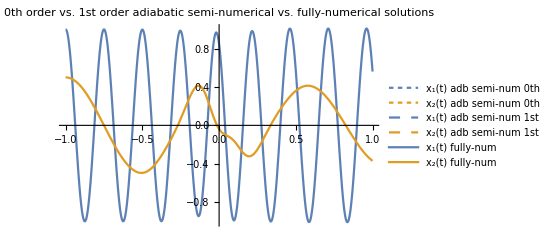

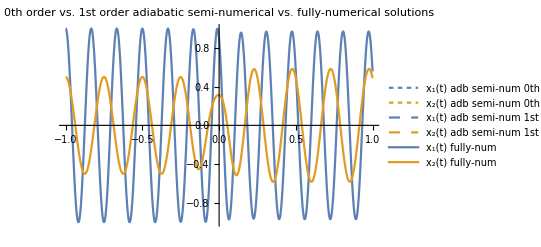

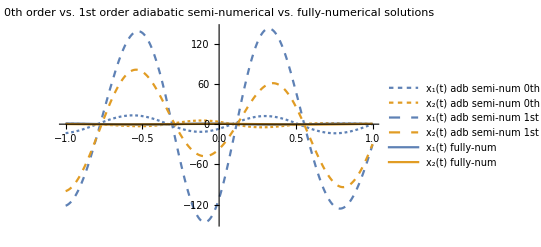

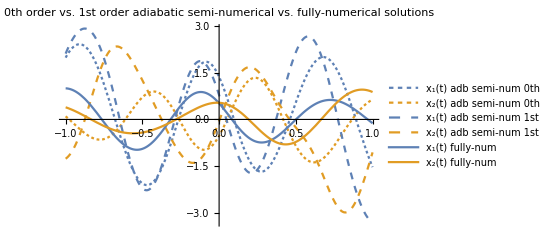

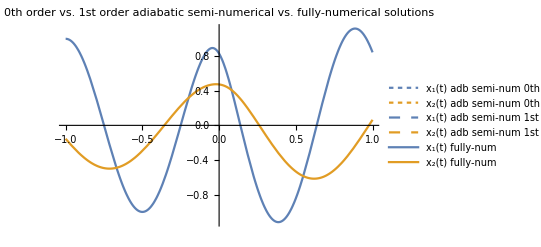

#### Plots for the anti-phase i.c.’s

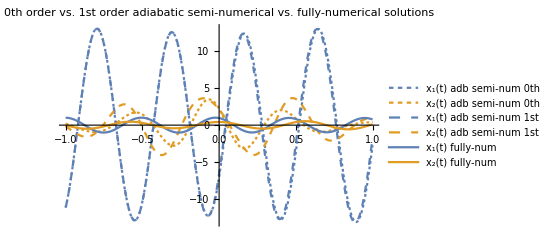

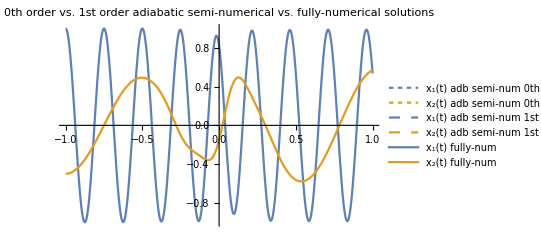

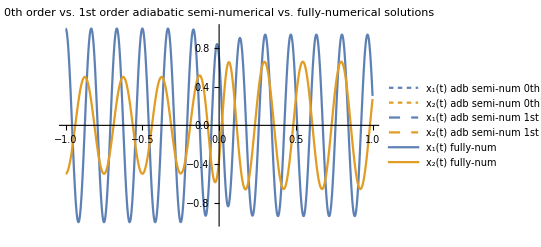

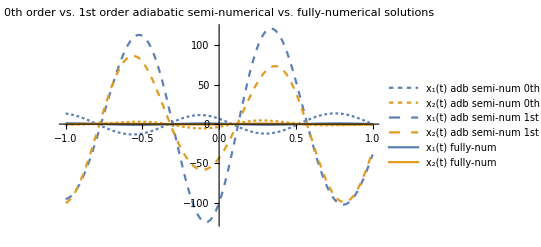

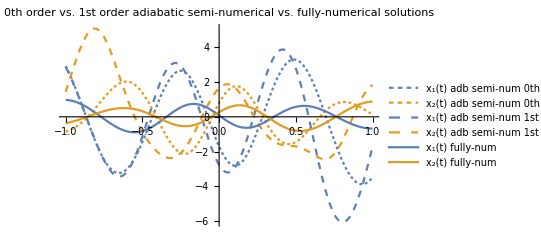

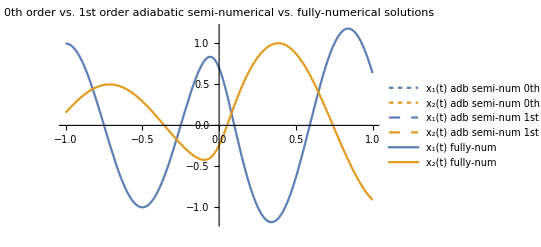

### Discussion

Something is *clearly* wrong with the perturbative parameters and/or the in/anti-phase initial conditions.

Since the approximation, even though not accurate, doesn’t break down for the same parameters and the single-oscillator i.c.’s, I assume the problem must come from the expansion constants implementing such i.c.’s.

At the same time, those constants implementing such initial conditions work for the test parameters, so the breakdown of the in/anti-phase constants and i.c.’s happens together with the perturbative parameters.

Actually, it is not the solution which breaks down, they are the initial conditions itself, and the constants constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T] (plus constsHOsOff) should guarantee the initial conditions for arbitrary {A1,A2}, for that is how they were computed. However, they work for

```mathematica
icOsc1
```

{A1→1,A2→0}

but not for

```mathematica
icInPhase
```

{A1→1,A2→0.5}

nor

```mathematica
icAntiPhase
```

{A1→1,A2→-0.5}

Check for the test parameters:

```mathematica
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][ti](*==A1*)/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff/.pert2adiab/.paramTest/.A1->3/.A2->7//Chop
```

{3.,7.}

Check for similar but different parameters:

```mathematica
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][ti](*==A1*)/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff/.pert2adiab/.{ω1->2,α1->2,τ1->0.5,ω2->1/2,α2->2,τ2->0.5,αc->2,τc->1,T->3}/.A1->3/.A2->7//Chop
```

{3.,7.}

But for the perturbative parameters…

```mathematica
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][ti](*==A1*)/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff/.pert2adiab/.pertParam[0]/.T->3/.A1->3/.A2->7//Chop
```

{216.649,7.}

When do the parameters break the initial conditions? The problem comes from τ_i=τ_c, and/or from small τ_c’s:

```mathematica
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][ti][[1]](*==A1*)/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff/.pert2adiab/.{ω1->2,α1->2,τ1->0.5,ω2->1/2,α2->2,τ2->0.5,αc->2,τc->0.5,T->3}/.A1->3/.A2->7//Chop
```

-45.2548

They work again for τ_i=τ_c=1 or even for the slightly change τ_c=0.6>τ_i=0.5:

```mathematica
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][ti][[1]](*==A1*)/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff/.pert2adiab/.{ω1->2,α1->2,τ1->1,ω2->1/2,α2->2,τ2->1,αc->2,τc->1,T->3}/.A1->3/.A2->7//Chop
```

3.

```mathematica
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][ti][[1]](*==A1*)/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff/.pert2adiab/.{ω1->2,α1->2,τ1->0.5,ω2->1/2,α2->2,τ2->0.5,αc->2,τc->0.6,T->3}/.A1->3/.A2->7//Chop
```

3.09359

### Conclusion

Since the approximation is not even that good for the perturbative parameters, for the thesis report I will simply say that we need more adiabatic parameters (something completely understandable and logic) and not solve the issue of these i.c.’s, because even if I solve it I am not going to use them for such parameters.

And, even if I do use the perturbative parameters, I would use them to compare it with the perturbative plots! And those were made for single-oscillator i.c.’s, which work fine. So settled.

## Klein-Gordon norm

↪︎ Some plots here take long time to draw.

#### KG colors

```mathematica
colorNum=ColorData[97,1]
color0th=ColorData[35,2]
color1st=Orange
color2nd=ColorData[35,1]
```

RGBColor[0.368417, 0.506779, 0.709798]

RGBColor[1., 0.7254901960784313, 0.09411764705882353]

RGBColor[1, 0.5, 0]

RGBColor[0.803921568627451, 0.30980392156862746, 0.07058823529411765]

### Numerical solution - Oscillator 1

#### Computation

```mathematica
kgNormFullNum[ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_]=KleinGordonNorm[{
x[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
x[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t](*,
x[3][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]*)}/.solNumGral]/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff;
```

#### Static plot

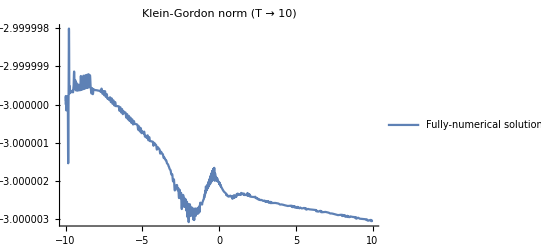

```mathematica
Plot[Evaluate[
kgNormFullNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.paramTest/.icOsc1
],relevantdomain,
PlotLabel->"Klein-Gordon norm (T → 10)",
PlotLegends->{"Fully-numerical solution"}]
```

#### Manipulable plot

(Since it takes a bit in computing every time we change T, we keep it unevaluated.)

```mathematica
(*Manipulate[
Plot[Evaluate[{
kgNormFullNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]}
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotLabel->"Klein-Gordon norm",
PlotLegends->{"Fully-numerical solution"}],
Style["Parameters",12],
{{ω1,1/2,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,1,"τ_1"},0.1,5},
{{ω2,1,"ω_2"},0.1,5},{{α2,1,"α_2"},0.1,5},{{τ2,1,"τ_2"},0.1,5},
{{αc,1,"α_c"},0.1,5},{{τc,1,"τ_c"},0.1,5},Style["
Initial conditions",12],{{A1,1,"A_1"},-10,10},Style["
Adiabatic regime",12],{{T,3,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]*)
```

### Numerical solution - General

#### Computation

```mathematica
kgNormFullNumGral[ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_]=KleinGordonNorm[{
x[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
x[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]}/.solNumGral];
```

#### Static plot

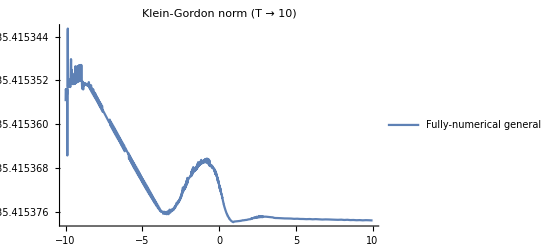

```mathematica
Plot[Evaluate[
kgNormFullNumGral[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.{ω1->0.67,α1->1/2,τ1->1/2,A1->2.83,ω2->0.92,α2->2,τ2->1.41,A2->0,αc->2.96,τc->1.17,T->3.3}
],relevantdomain,
PlotLabel->"Klein-Gordon norm (T → 10)",
PlotLegends->{"Fully-numerical general solution"}]
```

#### Manipulable plot

```mathematica
Manipulate[
Plot[Evaluate[{
kgNormFullNumGral[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]}
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotLabel->"Klein-Gordon norm",
PlotLegends->{"Fully-numerical solution"}],
Style["Parameters",12],
{{ω1,0.67,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,0.5,"τ_1"},0.1,5},
{{ω2,0.92,"ω_2"},0.1,5},{{α2,2,"α_2"},0.1,5},{{τ2,1.41,"τ_2"},0.1,5},
{{αc,2.96,"α_c"},0.1,5},{{τc,1.17,"τ_c"},0.1,5},Style["
Initial conditions",12],{{A1,2.83,"A_1"},-10,10},{{A2,0,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,3.3},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

### Semi-analytical solutions - 0th and 1st orders

#### Computation

```mathematica
kgNormAdbNum[0][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_]=KleinGordonNorm[vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]];
```

```mathematica
kgNormAdbNum[1][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_]=KleinGordonNorm[vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]];
```

#### Static plots

0th order:

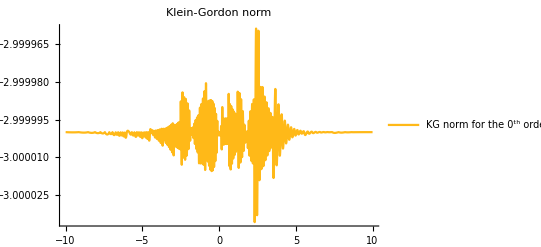

```mathematica
Plot[Evaluate[{
kgNormAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]}/.Flatten[{constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],constsHOsOff}/.paramTest]/.paramTest/.icOsc1
],relevantdomain,PlotRange->All,
PlotStyle->color0th,
PlotLabel->"Klein-Gordon norm",
PlotLegends->{"KG norm for the
0^th order solution"}]
```

1st order:

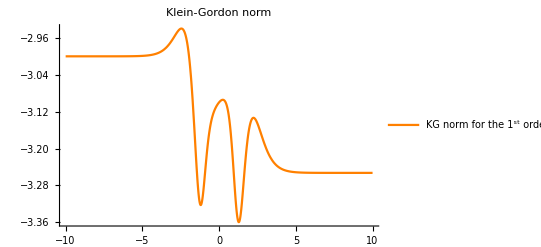

```mathematica
Plot[Evaluate[{
kgNormAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]}/.Flatten[{constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],constsHOsOff}/.paramTest]/.paramTest/.icOsc1
],relevantdomain,PlotRange->All,
PlotStyle->color1st,
PlotLabel->"Klein-Gordon norm",
PlotLegends->{"KG norm for the
1^st order solution"}]
```

#### Manipulable plot (switched off)

```mathematica
(*Manipulate[
Plot[Evaluate[{
kgNormAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],kgNormAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]}/.Flatten[{constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],constsHOsOff}/.paramTest]/.icOsc1
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotStyle->{color1st,color0th},
PlotLabel->"Klein-Gordon norm",
PlotLegends->{"KG norm for the
1^st order solution","KG norm for the
0^th order solution"}],
Style["Parameters",12],
{{ω1,1/2,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,1,"τ_1"},0.1,5},{{ω2,1,"ω_2"},0.1,5},{{α2,1,"α_2"},0.1,5},{{τ2,1,"τ_2"},0.1,5},{{αc,1,"α_c"},0.1,5},{{τc,1,"τ_c"},0.1,5},Style["
Adiabatic regime",12],{{T,3,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]*)
```

### Semi-analytical solutions - 2nd order ↪︎ Didn’t compute; leave more time (switched off for now)

#### Computation

```mathematica
(*AbsoluteTiming[KleinGordonNorm[vxAdbNum[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]]];
%[[1]]
kgNormAdbNum[2][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_]=%%[[2]];*)
```

#### Static plot

2nd order:

```mathematica
(*AbsoluteTiming[
Plot[Evaluate[{
kgNormAdbNum[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]}/.Flatten[{constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],constsHOsOff}/.paramTest]/.paramTest/.icOsc1
],relevantdomain,PlotRange->All,
PlotStyle->color2nd,
PlotLabel->"Klein-Gordon norm",
PlotLegends->{"KG norm for the
2^nd order solution"}]
];
%[[1]]
%%[[2]]*)
```

#### Manipulable plot (switched off)

```mathematica
(*Manipulate[
Plot[Evaluate[{
kgNormAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],kgNormAdbNum[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],kgNormAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]}/.Flatten[{constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],constsHOsOff}/.paramTest]/.icOsc1
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotStyle->{color1st,color2nd,color0th},
PlotLabel->"Klein-Gordon norm",
PlotLegends->{"KG norm for the
1^st order solution","KG norm for the
2^nd order solution","KG norm for the
0^th order solution"}],
Style["Parameters",12],
{{ω1,1/2,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,1,"τ_1"},0.1,5},{{ω2,1,"ω_2"},0.1,5},{{α2,1,"α_2"},0.1,5},{{τ2,1,"τ_2"},0.1,5},{{αc,1,"α_c"},0.1,5},{{τc,1,"τ_c"},0.1,5},Style["
Adiabatic regime",12],{{T,3,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]*)
```

### Comparisons

#### 0th and 1st orders vs. numerical - Static plot

0th and 1st orders vs. fully-numerical:

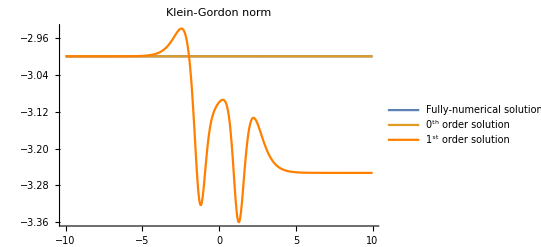

```mathematica
Plot[Evaluate[{
kgNormFullNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],
kgNormAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],
kgNormAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]}/.Flatten[{constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],constsHOsOff}/.paramTest]/.paramTest/.icOsc1
],relevantdomain,PlotRange->All,
PlotStyle->{colorNum,color0thDashed,color1st},
PlotLabel->"Klein-Gordon norm",
PlotLegends->{"Fully-numerical solution","0^th order solution","1^st order solution"}]
```

#### 0th, 1st and 2nd orders vs. numerical - Static plot (switched off)

All orders vs. fully-numerical:

```mathematica
(*AbsoluteTiming[
Plot[Evaluate[{
kgNormFullNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],kgNormAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],kgNormAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],kgNormAdbNum[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]}/.Flatten[{constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],constsHOsOff}/.paramTest]/.paramTest/.icOsc1
],relevantdomain,
PlotStyle->{colorNum,color0th,color1st,color2nd},
PlotLabel->"Klein-Gordon norm",
PlotLegends->{"Fully-numerical solution","0^th order solution","1^st order solution","2^nd order solution"}]
];
%[[1]]
%%[[2]]*)
```

### Exploration of Klein-Gordon norms to be sure the zero solution is not an error

Some wave equations’ solutions have certain Klein-Gordon norm:

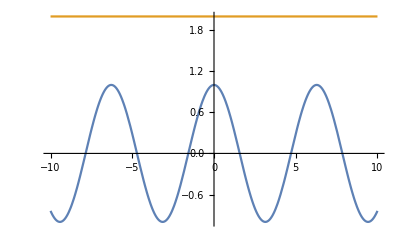

```mathematica
Plot[Evaluate[{Re[ⅇ^(ⅈ t)],KleinGordonNorm[ⅇ^(ⅈ t)]}],relevantdomain]
```

And some have others, including zero:

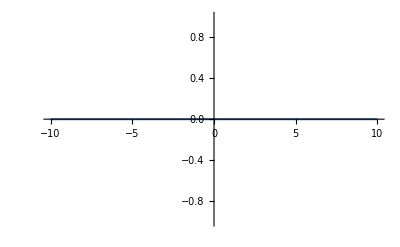

```mathematica
Plot[Evaluate[KleinGordonNorm[Cos[t]]],relevantdomain]
```

So I think I don’t have to worry about it.

In any case, the KleinGordonNorm function works well (and all within it).

### Normalized versions

#### Initial KG norm values (for test parameters and oscillator 1 i.c.’s)

```mathematica
kgNormFullNumGral[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.t->ti/.paramTest/.icOsc1
```

-3.+0. ⅈ

```mathematica
kgNormAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.t->ti/.constsTest/.paramTest/.icOsc1
```

-3.+5.80185×10^-25 ⅈ

```mathematica
kgNormAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.t->ti/.constsTest/.paramTest/.icOsc1
```

-3.+3.79107×10^-25 ⅈ

```mathematica
kgNormAdbNum[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.t->ti/.constsTest/.paramTest/.icOsc1
```

kgNormAdbNum[2][1/2,1,1,1,1,1,1,0,1,1,3]

#### Initial KG norm values (for generic parameters)

```mathematica
kgNormFullNumGralti[ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_]=kgNormFullNumGral[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.t->ti;
```

```mathematica
kgNormAdbNumti[0][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_]=kgNormAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.t->ti;
```

```mathematica
kgNormAdbNumti[1][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_]=kgNormAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.t->ti;
```

```mathematica
kgNormAdbNumti[2][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_]=kgNormAdbNum[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.t->ti;
```

#### Normalized KG norms

```mathematica
kgNormFullNumGralNormalized[ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_]=
kgNormFullNumGral[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/kgNormFullNumGralti[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T];
```

```mathematica
kgNormAdbNumNormalized[0][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_]=kgNormAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/kgNormAdbNumti[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T];
```

```mathematica
kgNormAdbNumNormalized[1][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_]=kgNormAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/kgNormAdbNumti[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T];
```

```mathematica
kgNormAdbNumNormalized[2][ω1_,α1_,τ1_,A1_,ω2_,α2_,τ2_,A2_,αc_,τc_,T_]=kgNormAdbNum[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/kgNormAdbNumti[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T];
```

#### Plots (T → 3) - Osc1 i.c.’s

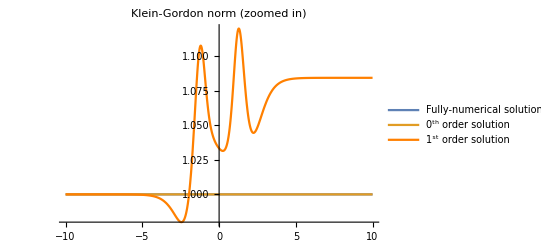

```mathematica
Plot[Evaluate[{
kgNormFullNumGralNormalized[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],
kgNormAdbNumNormalized[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],
kgNormAdbNumNormalized[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]
(*,kgNormAdbNumNormalized[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]*)
}/.Flatten[{constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],constsHOsOff}/.paramTest]/.paramTest/.icOsc1
],relevantdomain,PlotRange->All,
PlotStyle->{colorNum,color0thDashed,color1st},
PlotLabel->"Klein-Gordon norm (zoomed in)",
PlotLegends->{"Fully-numerical solution","0^th order solution","1^st order solution","2^nd order solution"}]
```

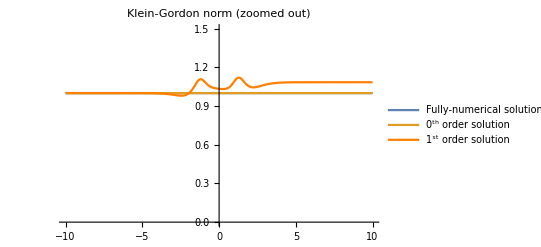

```mathematica
Plot[Evaluate[{
kgNormFullNumGralNormalized[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],
kgNormAdbNumNormalized[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],
kgNormAdbNumNormalized[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]
(*,kgNormAdbNumNormalized[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]*)
}/.Flatten[{constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],constsHOsOff}/.paramTest]/.paramTest/.icOsc1
],relevantdomain,PlotRange->{0,1.5},
PlotStyle->{colorNum,color0thDashed,color1st},
PlotLabel->"Klein-Gordon norm (zoomed out)",
PlotLegends->{"Fully-numerical solution","0^th order solution","1^st order solution","2^nd order solution"}]
```

#### Plots (T → 10) - Osc1 i.c.’s

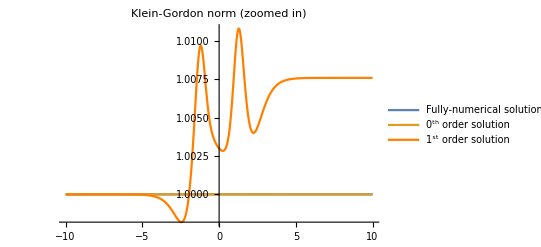

```mathematica
Plot[Evaluate[{
kgNormFullNumGralNormalized[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],
kgNormAdbNumNormalized[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],
kgNormAdbNumNormalized[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]
(*,kgNormAdbNumNormalized[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]*)
}/.Flatten[{constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],constsHOsOff}/.paramTest]/.T->10/.paramTest/.icOsc1
],relevantdomain,PlotRange->All,
PlotStyle->{colorNum,color0thDashed,color1st,color2nd},
PlotLabel->"Klein-Gordon norm (zoomed in)",
PlotLegends->{"Fully-numerical solution","0^th order solution","1^st order solution","2^nd order solution"}]
```

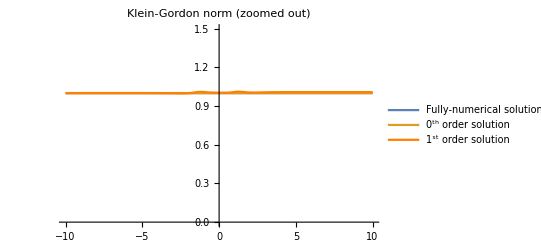

```mathematica
Plot[Evaluate[{
kgNormFullNumGralNormalized[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],
kgNormAdbNumNormalized[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],
kgNormAdbNumNormalized[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]
(*,kgNormAdbNumNormalized[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]*)
}/.Flatten[{constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],constsHOsOff}/.paramTest]/.T->10/.paramTest/.icOsc1
],relevantdomain,PlotRange->{0,1.5},
PlotStyle->{colorNum,color0thDashed,color1st,color2nd},
PlotLabel->"Klein-Gordon norm (zoomed out)",
PlotLegends->{"Fully-numerical solution","0^th order solution","1^st order solution","2^nd order solution"}]
```

#### Plots (T → 3) - InPhase i.c.’s

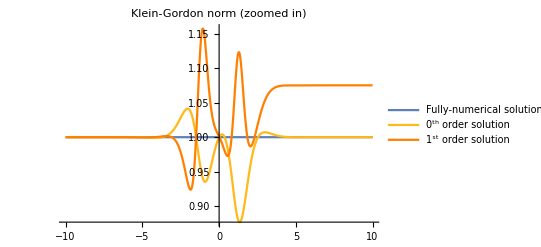

```mathematica
Plot[Evaluate[{
kgNormFullNumGralNormalized[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],
kgNormAdbNumNormalized[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],
kgNormAdbNumNormalized[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]
(*,kgNormAdbNumNormalized[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]*)
}/.Flatten[{constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],constsHOsOff}/.paramTest]/.paramTest/.icInPhase
],relevantdomain,PlotRange->All,
PlotStyle->{colorNum,color0th,color1st},
PlotLabel->"Klein-Gordon norm (zoomed in)",
PlotLegends->{"Fully-numerical solution","0^th order solution","1^st order solution","2^nd order solution"}]
```

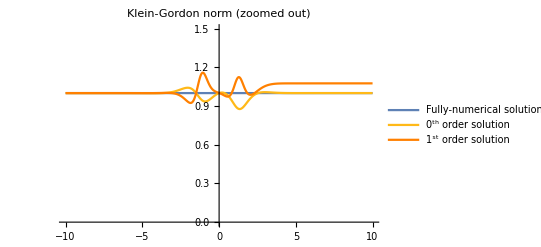

```mathematica
Plot[Evaluate[{
kgNormFullNumGralNormalized[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],
kgNormAdbNumNormalized[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],
kgNormAdbNumNormalized[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]
(*,kgNormAdbNumNormalized[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]*)
}/.Flatten[{constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],constsHOsOff}/.paramTest]/.paramTest/.icInPhase
],relevantdomain,PlotRange->{0,1.5},
PlotStyle->{colorNum,color0th,color1st},
PlotLabel->"Klein-Gordon norm (zoomed out)",
PlotLegends->{"Fully-numerical solution","0^th order solution","1^st order solution","2^nd order solution"}]
```

#### Plots (T → 10) - InPhase i.c.’s

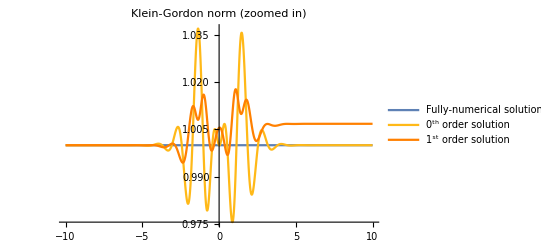

```mathematica
Plot[Evaluate[{
kgNormFullNumGralNormalized[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],
kgNormAdbNumNormalized[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],
kgNormAdbNumNormalized[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]
(*,kgNormAdbNumNormalized[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]*)
}/.Flatten[{constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],constsHOsOff}/.paramTest]/.T->10/.paramTest/.icInPhase
],relevantdomain,PlotRange->All,
PlotStyle->{colorNum,color0th,color1st,color2nd},
PlotLabel->"Klein-Gordon norm (zoomed in)",
PlotLegends->{"Fully-numerical solution","0^th order solution","1^st order solution","2^nd order solution"}]
```

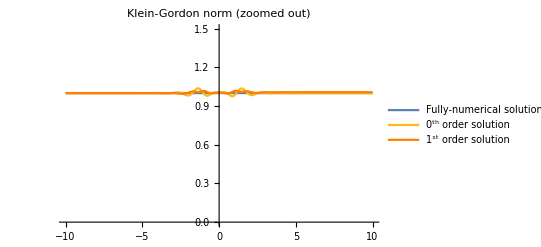

```mathematica
Plot[Evaluate[{
kgNormFullNumGralNormalized[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],
kgNormAdbNumNormalized[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],
kgNormAdbNumNormalized[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]
(*,kgNormAdbNumNormalized[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]*)
}/.Flatten[{constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T],constsHOsOff}/.paramTest]/.T->10/.paramTest/.icInPhase
],relevantdomain,PlotRange->{0,1.5},
PlotStyle->{colorNum,color0th,color1st,color2nd},
PlotLabel->"Klein-Gordon norm (zoomed out)",
PlotLegends->{"Fully-numerical solution","0^th order solution","1^st order solution","2^nd order solution"}]
```

## Extra

## Numerical solution: generic vs. single-oscillator i.c.’s comparison

#### ↪︎ Just to check the generic version worked well; no longer needed.

### Exact solutions: general vs. single-oscillator i.c.’s → Both i.c.’s solutions agree ✔

#### Static plot

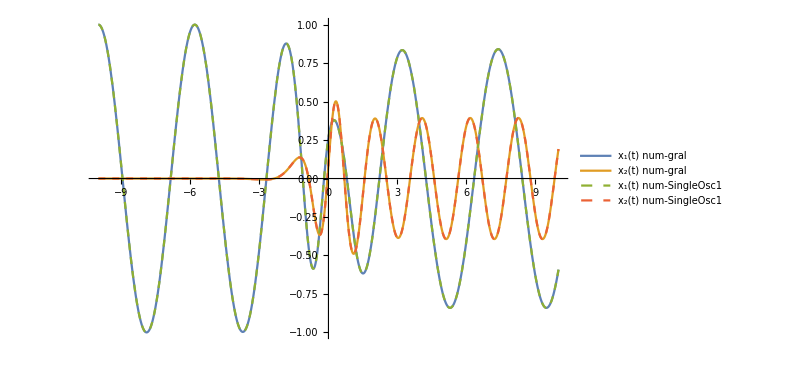

```mathematica
Plot[
Evaluate[{
{Re[x[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]],
Re[x[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]](*,
Re[x[3][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]]*)}/.solNumGral,
{Re[x[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]],
Re[x[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]](*,
Re[x[3][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]]*)}/.solNumSingleOsc[1]
}/.paramTest/.icOsc1
],relevantdomain,
PlotRange->All,
PlotStyle->{SolidData,SolidData(*,SolidData*),Dashed,Dashed(*,Dashed*)},
PlotLegends->{
"x_1(t) num-gral","x_2(t) num-gral"(*,"x_3(t) num-gral"*),
"x_1(t) num-SingleOsc1","x_2(t) num-SingleOsc1"(*,"x_3(t) num-SingleOsc1"*)},
ImageSize->600]
```

#### Manipulable plot

```mathematica
Manipulate[
Plot[
Evaluate[{
{Re[x[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]],
Re[x[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]](*,
Re[x[3][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]]*)}/.solNumGral,
{Re[x[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]],
Re[x[2][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]](*,
Re[x[3][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]]*)}/.solNumSingleOsc[1]
}],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->All,
PlotStyle->{SolidData,SolidData(*,SolidData*),Dashed,Dashed(*,Dashed*)},
PlotLegends->{
"x_1(t) num-gral","x_2(t) num-gral"(*,"x_3(t) num-gral"*),
"x_1(t) num-SingleOsc1","x_2(t) num-SingleOsc1"(*,"x_3(t) num-SingleOsc1"*)},
ImageSize->600],
Style["Parameters",12],
{{ω1,1/2,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,1,"τ_1"},0.1,5},
{{ω2,1,"ω_2"},0.1,5},{{α2,1,"α_2"},0.1,5},{{τ2,1,"τ_2"},0.1,5},
{{αc,1,"α_c"},0.1,5},{{τc,1,"τ_c"},0.1,5},Style["
Initial conditions",12],{{A1,1,"A_1"},-10,10},{{A2,0,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,3,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

### 0th adiabatic approx. vs. exact solution (single-oscillator i.c.’s) → Same plot as generic i.c.’s ✔

#### Static plot

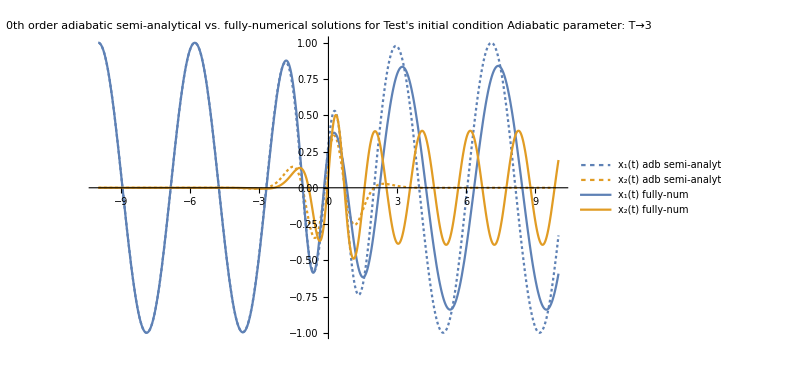

```mathematica
Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumSingleOsc[1]
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.paramTest/.icOsc1
],relevantdomain,
PlotRange->All,
PlotStyle->Flatten[{style0th,stylenum},1],
PlotLegends->{
"x_1(t) adb semi-analyt","x_2(t) adb semi-analyt"(*,"x_3(t) adb semi-analyt"*),
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order adiabatic semi-analytical vs. fully-numerical solutions for Test's initial condition
Adiabatic parameter: T"->3,
ImageSize->600]
```

#### Manipulable plot

```mathematica
Manipulate[
Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumSingleOsc[1]
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->All,
PlotStyle->Flatten[{style0th,stylenum},1],
PlotLegends->{
"x_1(t) adb semi-analyt","x_2(t) adb semi-analyt"(*,"x_3(t) adb semi-analyt"*),
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order adiabatic semi-analytical vs. fully-numerical solutions",
ImageSize->600],
Style["Parameters",12],
{{ω1,1/2,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,1,"τ_1"},0.1,5},
{{ω2,1,"ω_2"},0.1,5},{{α2,1,"α_2"},0.1,5},{{τ2,1,"τ_2"},0.1,5},
{{αc,1,"α_c"},0.1,5},{{τc,1,"τ_c"},0.1,5},Style["
Initial conditions",12],{{A1,1,"A_1"},-10,10},{{A2,0,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,3,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

### 1st adiabatic approx. vs. exact solution (single-oscillator i.c.’s) → Same plot as generic i.c.’s ✔

#### Static plot

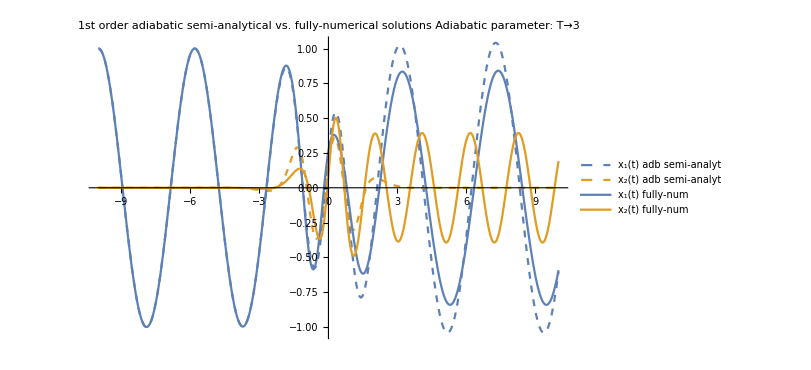

```mathematica
Plot[
Evaluate@Re[{
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumSingleOsc[1]
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff/.paramTest/.icOsc1
],relevantdomain,
PlotRange->All,
PlotStyle->Flatten[{style1st,stylenum},1],
PlotLegends->{
"x_1(t) adb semi-analyt","x_2(t) adb semi-analyt"(*,"x_3(t) adb semi-analyt"*),
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"1st order adiabatic semi-analytical vs. fully-numerical solutions
Adiabatic parameter: T"->3,
ImageSize->600]
```

#### Manipulable plot

```mathematica
Manipulate[
Plot[
Evaluate@Re[{
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumSingleOsc[1]
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->All,
PlotStyle->Flatten[{style1st,stylenum},1],
PlotLegends->{
"x_1(t) adb semi-analyt","x_2(t) adb semi-analyt"(*,"x_3(t) adb semi-analyt"*),
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"1st order adiabatic semi-analytical vs. fully-numerical solutions",
ImageSize->600],
Style["Parameters",12],
{{ω1,1/2,"ω_1"},0.1,5},{{α1,1/2,"α_1"},0.1,5},{{τ1,1,"τ_1"},0.1,5},
{{ω2,1,"ω_2"},0.1,5},{{α2,1,"α_2"},0.1,5},{{τ2,1,"τ_2"},0.1,5},
{{αc,1,"α_c"},0.1,5},{{τc,1,"τ_c"},0.1,5},Style["
Initial conditions",12],{{A1,1,"A_1"},-10,10},{{A2,0,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,3,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

## Representative plots: WKB approximation (semi-analytic) vs. exact solution (numerical)

## Adiabatic vs. exact - Both oscillators initially excited (good results)

### Adiabatic regime

Figure 4.3 in the report.

#### Static plot

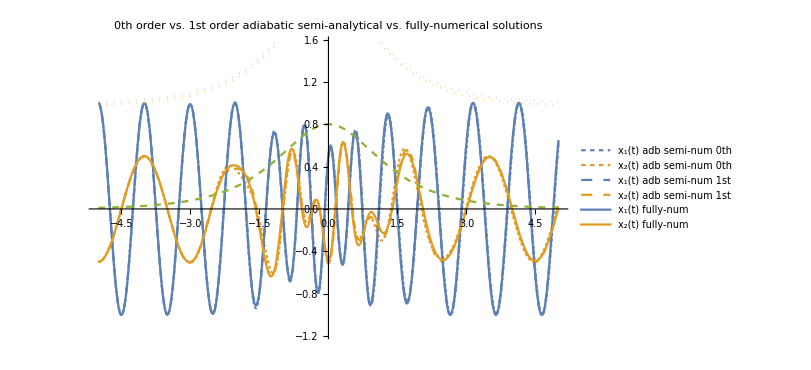

#### Manipulable plot

```mathematica
paramAdiabReg={ω1->2π,α1->2π,τ1->1,ω2->π,α2->π,τ2->1,αc->2π,τc->1,A1->A1/.icInPhase,A2->A2/.icInPhase,T->1};
Manipulate[{
(*c=*)(2αc^2)/(ω1^2+ω2^2+α1^2+α2^2)//N,
T*τc(ω1+ω2)/π//N,
Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral,
(2αc^2)/(ω1^2+ω2^2+α1^2+α2^2)Sech[t/τc],
1+α1^2Sech[t/τ1]/ω1^2,
0.97+α2^2Sech[t/τ2]/ω2^2
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->{-1.17,1.57},
PlotStyle->Flatten[{style0th,style1st,stylenum,{{Dashed,RGBColor[0.560181, 0.691569, 0.194885]}},{{Dotted,RGBColor[0.753628, 0.82591, 0.991257]}},{{Dotted,RGBColor[1, 0.784756, 0.323308]}}},1],
PlotLegends->{
"x_1(t) adb semi-num 0th","x_2(t) adb semi-num 0th",(*"x_3(t) adb semi-num 0th",*)
"x_1(t) adb semi-num 1st","x_2(t) adb semi-num 1st",(*"x_3(t) adb semi-num 1st",*)
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order vs. 1st order adiabatic semi-analytical vs. fully-numerical solutions",
ImageSize->600]},
Style["Parameters",12],
{{ω1,2π,"ω_1"},0.1,20},{{α1,2π,"α_1"},0.1,20},{{τ1,1,"τ_1"},0.1,20},
{{ω2,π,"ω_2"},0.1,20},{{α2,π,"α_2"},0.1,20},{{τ2,1,"τ_2"},0.1,20},
{{αc,2π,"α_c"},0.1,20},{{τc,1,"τ_c"},0.1,20},Style["
Initial conditions",12],{{A1,A1/.icInPhase,"A_1"},-10,10},{{A2,A2/.icInPhase,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,1,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

### More regimes (manipulable plots)

Figure 4.5 a)-e) in the report.

#### a) Fairly adiabatic regime

```mathematica
Manipulate[{
(*c=*)(2αc^2)/(ω1^2+ω2^2+α1^2+α2^2)//N,
T*τc(ω1+ω2)/π//N,
Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral,
(2αc^2)/(ω1^2+ω2^2+α1^2+α2^2)Sech[t/τc],
1+α1^2Sech[t/τ1]/ω1^2,
0.97+α2^2Sech[t/τ2]/ω2^2
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->{-1.17,1.57},
PlotStyle->Flatten[{style0th,style1st,stylenum,{{Dashed,RGBColor[0.560181, 0.691569, 0.194885]}},{{Dotted,RGBColor[0.753628, 0.82591, 0.991257]}},{{Dotted,RGBColor[1, 0.784756, 0.323308]}}},1],
PlotLegends->{
"x_1(t) adb semi-num 0th","x_2(t) adb semi-num 0th",(*"x_3(t) adb semi-num 0th",*)
"x_1(t) adb semi-num 1st","x_2(t) adb semi-num 1st",(*"x_3(t) adb semi-num 1st",*)
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order vs. 1st order adiabatic semi-analytical vs. fully-numerical solutions",
ImageSize->600]},
Style["Parameters",12],
{{ω1,1.4π,"ω_1"},0.1,20},{{α1,1.4π,"α_1"},0.1,20},{{τ1,1,"τ_1"},0.1,20},
{{ω2,0.4π,"ω_2"},0.1,20},{{α2,0.4π,"α_2"},0.1,20},{{τ2,1,"τ_2"},0.1,20},
{{αc,1.4π,"α_c"},0.1,20},{{τc,1,"τ_c"},0.1,20},Style["
Initial conditions",12],{{A1,A1/.icInPhase,"A_1"},-10,10},{{A2,A2/.icInPhase,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,1,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,Abs[ti]*1.5,"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

#### b) Leaving the adiabatic regime - Near resonance

```mathematica
Manipulate[{
(*c=*)(2αc^2)/(ω1^2+ω2^2+α1^2+α2^2)//N,
T*τc(ω1+ω2)/π//N,
Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral,
(2αc^2)/(ω1^2+ω2^2+α1^2+α2^2)Sech[t/τc],
1+α1^2Sech[t/τ1]/ω1^2,
0.97+α2^2Sech[t/τ2]/ω2^2
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->{-1.17,1.57},
PlotStyle->Flatten[{style0th,style1st,stylenum,{{Dashed,RGBColor[0.560181, 0.691569, 0.194885]}},{{Dotted,RGBColor[0.753628, 0.82591, 0.991257]}},{{Dotted,RGBColor[1, 0.784756, 0.323308]}}},1],
PlotLegends->{
"x_1(t) adb semi-num 0th","x_2(t) adb semi-num 0th",(*"x_3(t) adb semi-num 0th",*)
"x_1(t) adb semi-num 1st","x_2(t) adb semi-num 1st",(*"x_3(t) adb semi-num 1st",*)
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order vs. 1st order adiabatic semi-analytical vs. fully-numerical solutions",
ImageSize->600]},
Style["Parameters",12],
{{ω1,1.1π,"ω_1"},0.1,20},{{α1,1.1π,"α_1"},0.1,20},{{τ1,1,"τ_1"},0.1,20},
{{ω2,0.9π,"ω_2"},0.1,20},{{α2,0.9π,"α_2"},0.1,20},{{τ2,1,"τ_2"},0.1,20},
{{αc,1.3π,"α_c"},0.1,20},{{τc,1,"τ_c"},0.1,20},Style["
Initial conditions",12],{{A1,A1/.icInPhase,"A_1"},-10,10},{{A2,A2/.icInPhase,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,1,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,Abs[ti]*1.5,"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

#### c) Leaving the adiabatic regime

```mathematica
Manipulate[{
(*c=*)(2αc^2)/(ω1^2+ω2^2+α1^2+α2^2)//N,
T*τc(ω1+ω2)/π//N,
Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral,
(2αc^2)/(ω1^2+ω2^2+α1^2+α2^2)Sech[t/τc],
1+α1^2Sech[t/τ1]/ω1^2,
0.97+α2^2Sech[t/τ2]/ω2^2
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->{-1.17,1.57},
PlotStyle->Flatten[{style0th,style1st,stylenum,{{Dashed,RGBColor[0.560181, 0.691569, 0.194885]}},{{Dotted,RGBColor[0.753628, 0.82591, 0.991257]}},{{Dotted,RGBColor[1, 0.784756, 0.323308]}}},1],
PlotLegends->{
"x_1(t) adb semi-num 0th","x_2(t) adb semi-num 0th",(*"x_3(t) adb semi-num 0th",*)
"x_1(t) adb semi-num 1st","x_2(t) adb semi-num 1st",(*"x_3(t) adb semi-num 1st",*)
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order vs. 1st order adiabatic semi-analytical vs. fully-numerical solutions",
ImageSize->600]},
Style["Parameters",12],
{{ω1,0.8π,"ω_1"},0.1,20},{{α1,0.8π,"α_1"},0.1,20},{{τ1,1,"τ_1"},0.1,20},
{{ω2,0.4π,"ω_2"},0.1,20},{{α2,0.4π,"α_2"},0.1,20},{{τ2,1,"τ_2"},0.1,20},
{{αc,2π,"α_c"},0.1,20},{{τc,1,"τ_c"},0.1,20},Style["
Initial conditions",12],{{A1,A1/.icInPhase,"A_1"},-10,10},{{A2,A2/.icInPhase,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,1,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,Abs[ti]*1.2,"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

#### d) Recovering adiabaticity

```mathematica
Manipulate[{
(*c=*)(2αc^2)/(ω1^2+ω2^2+α1^2+α2^2)//N,
T*τc(ω1+ω2)/π//N,
Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral,
(2αc^2)/(ω1^2+ω2^2+α1^2+α2^2)Sech[t/τc],
1+α1^2Sech[t/τ1]/ω1^2,
0.97+α2^2Sech[t/τ2]/ω2^2
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->{-1.17,1.57},
PlotStyle->Flatten[{style0th,style1st,stylenum,{{Dashed,RGBColor[0.560181, 0.691569, 0.194885]}},{{Dotted,RGBColor[0.753628, 0.82591, 0.991257]}},{{Dotted,RGBColor[1, 0.784756, 0.323308]}}},1],
PlotLegends->{
"x_1(t) adb semi-num 0th","x_2(t) adb semi-num 0th",(*"x_3(t) adb semi-num 0th",*)
"x_1(t) adb semi-num 1st","x_2(t) adb semi-num 1st",(*"x_3(t) adb semi-num 1st",*)
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order vs. 1st order adiabatic semi-analytical vs. fully-numerical solutions",
ImageSize->600]},
Style["Parameters",12],
{{ω1,0.8π,"ω_1"},0.1,20},{{α1,0.8π,"α_1"},0.1,20},{{τ1,1,"τ_1"},0.1,20},
{{ω2,0.4π,"ω_2"},0.1,20},{{α2,0.4π,"α_2"},0.1,20},{{τ2,1,"τ_2"},0.1,20},
{{αc,2π,"α_c"},0.1,20},{{τc,1,"τ_c"},0.1,20},Style["
Initial conditions",12],{{A1,A1/.icInPhase,"A_1"},-10,10},{{A2,A2/.icInPhase,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,3,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,Abs[ti]*1.2,"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

#### e) Adiabatic but strong coupling regime

```mathematica
Manipulate[{
(*c=*)(2αc^2)/(ω1^2+ω2^2+α1^2+α2^2)//N,
T*τc(ω1+ω2)/π//N,
Plot[
Evaluate@Re[{
vxAdbNum[0][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vxAdbNum[1][ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t],
vx[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T][t]/.solNumGral,
(2αc^2)/(ω1^2+ω2^2+α1^2+α2^2)Sech[t/τc],
1+α1^2Sech[t/τ1]/ω1^2,
0.97+α2^2Sech[t/τ2]/ω2^2
}/.constsNum[ω1,α1,τ1,A1,ω2,α2,τ2,A2,αc,τc,T]/.constsHOsOff
],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->{-1.17,1.57},AspectRatio->0.6180339887498948/2,
PlotStyle->Flatten[{style0th,style1st,stylenum,{{Dashed,RGBColor[0.560181, 0.691569, 0.194885]}},{{Dotted,RGBColor[0.753628, 0.82591, 0.991257]}},{{Dotted,RGBColor[1, 0.784756, 0.323308]}}},1],
PlotLegends->{
"x_1(t) adb semi-num 0th","x_2(t) adb semi-num 0th",(*"x_3(t) adb semi-num 0th",*)
"x_1(t) adb semi-num 1st","x_2(t) adb semi-num 1st",(*"x_3(t) adb semi-num 1st",*)
"x_1(t) fully-num","x_2(t) fully-num"(*,"x_3(t) fully-num"*)},
PlotLabel->"0th order vs. 1st order adiabatic semi-analytical vs. fully-numerical solutions",
ImageSize->900]},
Style["Parameters",12],
{{ω1,2π,"ω_1"},0.1,20},{{α1,2π,"α_1"},0.1,20},{{τ1,1,"τ_1"},0.1,20},
{{ω2,π,"ω_2"},0.1,20},{{α2,π,"α_2"},0.1,20},{{τ2,1,"τ_2"},0.1,20},
{{αc,5π,"α_c"},0.1,40},{{τc,1,"τ_c"},0.1,20},Style["
Initial conditions",12],{{A1,A1/.icInPhase,"A_1"},-10,10},{{A2,A2/.icInPhase,"A_2"},-10,10},Style["
Adiabatic regime",12],{{T,1,"T "},1,Tmax},Style["
Manipulate graph",12],{{WindowSize,Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```